```mathematica
Needs["SubKernels`"];
numKern=ToExpression[Environment["SLURM_CPUS_PER_TASK"]];
LaunchKernels[numKern];
Print[OutputForm["Number of Parallel Kernels:"<>ToString[$KernelCount]]];
```

```mathematica
Tadpole1:=2945 y[1]^2-1650 y[1] y[2]+2205 y[2]^2-1417 y[1] y[3]+1740 y[2] y[3]+1097 y[3]^2+668 y[1] y[4]+450 y[2] y[4]+623 y[3] y[4]+254 y[4]^2-778 y[1] y[5]+1929 y[2] y[5]+1981 y[3] y[5]+593 y[4] y[5]+1202 y[5]^2+614 y[1] y[6]+807 y[2] y[6]+626 y[3] y[6]+472 y[4] y[6]+800 y[5] y[6]+326 y[6]^2+228 y[1] y[7]+543 y[2] y[7]+768 y[3] y[7]+392 y[4] y[7]+822 y[5] y[7]+446 y[6] y[7]+228 y[7]^2+9 y[1] y[8]+48 y[2] y[8]-15 y[3] y[8]+17 y[4] y[8]-12 y[5] y[8]+20 y[6] y[8]+12 y[7] y[8]+12 y[8]^2-1227 y[1] y[9]+2031 y[2] y[9]+1992 y[3] y[9]+492 y[4] y[9]+2100 y[5] y[9]+600 y[6] y[9]+666 y[7] y[9]+9 y[8] y[9]+1236 y[9]^2+614 y[1] y[10]+807 y[2] y[10]+626 y[3] y[10]+472 y[4] y[10]+710 y[5] y[10]+556 y[6] y[10]+372 y[7] y[10]+690 y[9] y[10]+326 y[10]^2+677 y[1] y[11]+441 y[2] y[11]+757 y[3] y[11]+493 y[4] y[11]+730 y[5] y[11]+482 y[6] y[11]+426 y[7] y[11]-20 y[8] y[11]+690 y[9] y[11]+556 y[10] y[11]+326 y[11]^2+458 y[1] y[12]-54 y[2] y[12]-26 y[3] y[12]+118 y[4] y[12]-5 y[5] y[12]+110 y[6] y[12]+58 y[7] y[12]-66 y[9] y[12]+130 y[10] y[12]+130 y[11] y[12]+32 y[12]^2+296 y[1] y[13]+6 y[2] y[13]-167 y[3] y[13]+11 y[4] y[13]-68 y[5] y[13]+94 y[6] y[13]-24 y[7] y[13]-2 y[8] y[13]-102 y[9] y[13]+94 y[10] y[13]+10 y[11] y[13]+32 y[12] y[13]+68 y[13]^2+332 y[1] y[14]-17 y[3] y[14]+98 y[4] y[14]-14 y[5] y[14]+130 y[6] y[14]+58 y[7] y[14]-66 y[9] y[14]+130 y[10] y[14]+110 y[11] y[14]+52 y[12] y[14]+52 y[13] y[14]+32 y[14]^2-864 y[1] y[15]+1398 y[2] y[15]+1407 y[3] y[15]+360 y[4] y[15]+1491 y[5] y[15]+444 y[6] y[15]+486 y[7] y[15]+3 y[8] y[15]+1527 y[9] y[15]+444 y[10] y[15]+450 y[11] y[15]-33 y[12] y[15]-63 y[13] y[15]-33 y[14] y[15]+624 y[15]^2+276 y[1] y[16]+471 y[2] y[16]+387 y[3] y[16]+260 y[4] y[16]+435 y[5] y[16]+308 y[6] y[16]+222 y[7] y[16]+6 y[8] y[16]+387 y[9] y[16]+308 y[10] y[16]+270 y[11] y[16]+54 y[12] y[16]+36 y[13] y[16]+54 y[14] y[16]+330 y[15] y[16]+114 y[16]^2+468 y[1] y[17]+11 y[2] y[17]+499 y[3] y[17]+336 y[4] y[17]+441 y[5] y[17]+294 y[6] y[17]+308 y[7] y[17]-3 y[8] y[17]+360 y[9] y[17]+294 y[10] y[17]+389 y[11] y[17]+78 y[12] y[17]-9 y[13] y[17]+63 y[14] y[17]+326 y[15] y[17]+204 y[16] y[17]+178 y[17]^2+219 y[1] y[18]-114 y[2] y[18]-9 y[3] y[18]+50 y[4] y[18]+30 y[6] y[18]+27 y[7] y[18]+2 y[8] y[18]-18 y[9] y[18]+30 y[10] y[18]+45 y[11] y[18]+20 y[12] y[18]+3 y[13] y[18]+12 y[14] y[18]-18 y[15] y[18]+30 y[16] y[18]+50 y[17] y[18]+12 y[18]^2+435 y[1] y[19]+452 y[2] y[19]+502 y[3] y[19]+322 y[4] y[19]+648 y[5] y[19]+452 y[6] y[19]+362 y[7] y[19]+468 y[9] y[19]+378 y[10] y[19]+378 y[11] y[19]+75 y[12] y[19]+74 y[13] y[19]+90 y[14] y[19]+410 y[15] y[19]+252 y[16] y[19]+292 y[17] y[19]+30 y[18] y[19]+222 y[19]^2+96 y[1] y[20]-48 y[2] y[20]+30 y[4] y[20]-9 y[5] y[20]+50 y[6] y[20]+27 y[7] y[20]+2 y[8] y[20]-18 y[9] y[20]+30 y[10] y[20]+30 y[11] y[20]+12 y[12] y[20]+18 y[13] y[20]+20 y[14] y[20]-18 y[15] y[20]+30 y[16] y[20]+30 y[17] y[20]+12 y[18] y[20]+50 y[19] y[20]+12 y[20]^2-71 y[1] y[21]-y[2] y[21]-7 y[3] y[21]-19 y[4] y[21]-8 y[5] y[21]-20 y[6] y[21]+12 y[8] y[21]+21 y[9] y[21]-35 y[10] y[21]-40 y[11] y[21]-16 y[12] y[21]-10 y[13] y[21]-16 y[14] y[21]+2 y[15] y[21]-2 y[16] y[21]+y[17] y[21]+2 y[18] y[21]+2 y[20] y[21]+12 y[21]^2+435 y[1] y[22]+452 y[2] y[22]+502 y[3] y[22]+322 y[4] y[22]+558 y[5] y[22]+378 y[6] y[22]+288 y[7] y[22]-15 y[8] y[22]+558 y[9] y[22]+452 y[10] y[22]+452 y[11] y[22]+90 y[12] y[22]+74 y[13] y[22]+90 y[14] y[22]+410 y[15] y[22]+252 y[16] y[22]+292 y[17] y[22]+30 y[18] y[22]+348 y[19] y[22]+30 y[20] y[22]-20 y[21] y[22]+222 y[22]^2+96 y[1] y[23]-48 y[2] y[23]+30 y[4] y[23]+30 y[6] y[23]+12 y[7] y[23]-6 y[8] y[23]-27 y[9] y[23]+50 y[10] y[23]+45 y[11] y[23]+20 y[12] y[23]+18 y[13] y[23]+20 y[14] y[23]-18 y[15] y[23]+30 y[16] y[23]+30 y[17] y[23]+12 y[18] y[23]+30 y[19] y[23]+12 y[20] y[23]-6 y[21] y[23]+50 y[22] y[23]+12 y[23]^2+378 y[1] y[24]-103 y[2] y[24]-18 y[3] y[24]+82 y[4] y[24]-y[5] y[24]+75 y[6] y[24]+46 y[7] y[24]-8 y[8] y[24]-54 y[9] y[24]+90 y[10] y[24]+110 y[11] y[24]+44 y[12] y[24]+24 y[13] y[24]+36 y[14] y[24]-34 y[15] y[24]+46 y[16] y[24]+82 y[17] y[24]+20 y[18] y[24]+70 y[19] y[24]+12 y[20] y[24]-8 y[21] y[24]+90 y[22] y[24]+20 y[23] y[24]+24 y[24]^2+255 y[1] y[25]-37 y[2] y[25]-9 y[3] y[25]+67 y[4] y[25]-10 y[5] y[25]+90 y[6] y[25]+46 y[7] y[25]-8 y[8] y[25]-54 y[9] y[25]+90 y[10] y[25]+90 y[11] y[25]+36 y[12] y[25]+44 y[13] y[25]+44 y[14] y[25]-34 y[15] y[25]+46 y[16] y[25]+62 y[17] y[25]+12 y[18] y[25]+90 y[19] y[25]+20 y[20] y[25]-8 y[21] y[25]+90 y[22] y[25]+20 y[23] y[25]+36 y[24] y[25]+24 y[25]^2+1206 y[1] y[26]-2781 y[2] y[26]-315 y[3] y[26]+78 y[4] y[26]-408 y[5] y[26]-183 y[6] y[26]+51 y[7] y[26]-30 y[8] y[26]-525 y[9] y[26]-183 y[10] y[26]+168 y[11] y[26]+87 y[12] y[26]-27 y[13] y[26]+33 y[14] y[26]-273 y[15] y[26]-99 y[16] y[26]+382 y[17] y[26]+99 y[18] y[26]+37 y[19] y[26]+33 y[20] y[26]-2 y[21] y[26]+37 y[22] y[26]+33 y[23] y[26]+115 y[24] y[26]+49 y[25] y[26]+1272 y[26]^2+447 y[1] y[27]+510 y[2] y[27]+366 y[3] y[27]+308 y[4] y[27]+426 y[5] y[27]+368 y[6] y[27]+249 y[7] y[27]+12 y[8] y[27]+360 y[9] y[27]+368 y[10] y[27]+315 y[11] y[27]+78 y[12] y[27]+54 y[13] y[27]+78 y[14] y[27]+228 y[15] y[27]+156 y[16] y[27]+158 y[17] y[27]+10 y[18] y[27]+218 y[19] y[27]+10 y[20] y[27]-19 y[21] y[27]+218 y[22] y[27]+10 y[23] y[27]+47 y[24] y[27]+47 y[25] y[27]-144 y[26] y[27]+150 y[27]^2+603 y[1] y[28]+638 y[2] y[28]+346 y[3] y[28]+300 y[4] y[28]+432 y[5] y[28]+357 y[6] y[28]+254 y[7] y[28]+6 y[8] y[28]+360 y[9] y[28]+357 y[10] y[28]+326 y[11] y[28]+78 y[12] y[28]+45 y[13] y[28]+72 y[14] y[28]+218 y[15] y[28]+160 y[16] y[28]+140 y[17] y[28]+12 y[18] y[28]+218 y[19] y[28]+9 y[20] y[28]-22 y[21] y[28]+218 y[22] y[28]+9 y[23] y[28]+50 y[24] y[28]+47 y[25] y[28]-284 y[26] y[28]+280 y[27] y[28]+166 y[28]^2+390 y[1] y[29]-42 y[2] y[29]-30 y[3] y[29]+98 y[4] y[29]-9 y[5] y[29]+90 y[6] y[29]+54 y[7] y[29]+8 y[8] y[29]-45 y[9] y[29]+90 y[10] y[29]+90 y[11] y[29]+44 y[12] y[29]+21 y[13] y[29]+36 y[14] y[29]-21 y[15] y[29]+34 y[16] y[29]+58 y[17] y[29]+12 y[18] y[29]+55 y[19] y[29]+4 y[20] y[29]-8 y[21] y[29]+55 y[22] y[29]+4 y[23] y[29]+28 y[24] y[29]+22 y[25] y[29]+90 y[26] y[29]+78 y[27] y[29]+78 y[28] y[29]+24 y[29]^2+435 y[1] y[30]+452 y[2] y[30]+502 y[3] y[30]+322 y[4] y[30]+648 y[5] y[30]+452 y[6] y[30]+362 y[7] y[30]+468 y[9] y[30]+378 y[10] y[30]+378 y[11] y[30]+75 y[12] y[30]+74 y[13] y[30]+90 y[14] y[30]+320 y[15] y[30]+178 y[16] y[30]+218 y[17] y[30]+15 y[18] y[30]+348 y[19] y[30]+30 y[20] y[30]-20 y[21] y[30]+274 y[22] y[30]+15 y[23] y[30]+55 y[24] y[30]+70 y[25] y[30]+16 y[26] y[30]+292 y[27] y[30]+292 y[28] y[30]+70 y[29] y[30]+222 y[30]^2+267 y[1] y[31]+30 y[2] y[31]-21 y[3] y[31]+78 y[4] y[31]-18 y[5] y[31]+110 y[6] y[31]+54 y[7] y[31]+8 y[8] y[31]-45 y[9] y[31]+90 y[10] y[31]+75 y[11] y[31]+36 y[12] y[31]+36 y[13] y[31]+44 y[14] y[31]-21 y[15] y[31]+34 y[16] y[31]+43 y[17] y[31]+4 y[18] y[31]+70 y[19] y[31]+12 y[20] y[31]-8 y[21] y[31]+55 y[22] y[31]+4 y[23] y[31]+22 y[24] y[31]+28 y[25] y[31]+18 y[26] y[31]+78 y[27] y[31]+70 y[28] y[31]+36 y[29] y[31]+90 y[30] y[31]+24 y[31]^2-71 y[1] y[32]-7 y[2] y[32]-7 y[3] y[32]-19 y[4] y[32]-8 y[5] y[32]-20 y[6] y[32]+12 y[8] y[32]+21 y[9] y[32]-35 y[10] y[32]-40 y[11] y[32]-16 y[12] y[32]-10 y[13] y[32]-16 y[14] y[32]+11 y[15] y[32]-17 y[16] y[32]-19 y[17] y[32]-6 y[18] y[32]-20 y[19] y[32]-6 y[20] y[32]+12 y[21] y[32]-35 y[22] y[32]-12 y[23] y[32]-16 y[24] y[32]-16 y[25] y[32]+13 y[26] y[32]-4 y[27] y[32]-2 y[28] y[32]+12 y[32]^2+435 y[1] y[33]+452 y[2] y[33]+502 y[3] y[33]+322 y[4] y[33]+558 y[5] y[33]+378 y[6] y[33]+288 y[7] y[33]-15 y[8] y[33]+558 y[9] y[33]+452 y[10] y[33]+452 y[11] y[33]+90 y[12] y[33]+74 y[13] y[33]+90 y[14] y[33]+320 y[15] y[33]+178 y[16] y[33]+218 y[17] y[33]+15 y[18] y[33]+274 y[19] y[33]+15 y[20] y[33]-35 y[21] y[33]+348 y[22] y[33]+30 y[23] y[33]+70 y[24] y[33]+70 y[25] y[33]+16 y[26] y[33]+292 y[27] y[33]+292 y[28] y[33]+70 y[29] y[33]+348 y[30] y[33]+70 y[31] y[33]-20 y[32] y[33]+222 y[33]^2+267 y[1] y[34]+30 y[2] y[34]-21 y[3] y[34]+78 y[4] y[34]-9 y[5] y[34]+90 y[6] y[34]+39 y[7] y[34]-54 y[9] y[34]+110 y[10] y[34]+90 y[11] y[34]+44 y[12] y[34]+36 y[13] y[34]+44 y[14] y[34]-21 y[15] y[34]+34 y[16] y[34]+43 y[17] y[34]+4 y[18] y[34]+55 y[19] y[34]+4 y[20] y[34]-14 y[21] y[34]+70 y[22] y[34]+12 y[23] y[34]+28 y[24] y[34]+28 y[25] y[34]+18 y[26] y[34]+78 y[27] y[34]+70 y[28] y[34]+36 y[29] y[34]+70 y[30] y[34]+36 y[31] y[34]-8 y[32] y[34]+90 y[33] y[34]+24 y[34]^2+378 y[1] y[35]-109 y[2] y[35]-18 y[3] y[35]+82 y[4] y[35]-y[5] y[35]+75 y[6] y[35]+46 y[7] y[35]-8 y[8] y[35]-54 y[9] y[35]+90 y[10] y[35]+110 y[11] y[35]+44 y[12] y[35]+24 y[13] y[35]+36 y[14] y[35]-25 y[15] y[35]+31 y[16] y[35]+62 y[17] y[35]+12 y[18] y[35]+55 y[19] y[35]+6 y[20] y[35]-16 y[21] y[35]+70 y[22] y[35]+12 y[23] y[35]+36 y[24] y[35]+28 y[25] y[35]+130 y[26] y[35]+62 y[27] y[35]+70 y[28] y[35]+36 y[29] y[35]+70 y[30] y[35]+28 y[31] y[35]-8 y[32] y[35]+90 y[33] y[35]+36 y[34] y[35]+24 y[35]^2+255 y[1] y[36]-37 y[2] y[36]-9 y[3] y[36]+67 y[4] y[36]-10 y[5] y[36]+90 y[6] y[36]+46 y[7] y[36]-8 y[8] y[36]-54 y[9] y[36]+90 y[10] y[36]+90 y[11] y[36]+36 y[12] y[36]+44 y[13] y[36]+44 y[14] y[36]-25 y[15] y[36]+31 y[16] y[36]+47 y[17] y[36]+6 y[18] y[36]+70 y[19] y[36]+12 y[20] y[36]-16 y[21] y[36]+70 y[22] y[36]+12 y[23] y[36]+28 y[24] y[36]+36 y[25] y[36]+58 y[26] y[36]+62 y[27] y[36]+62 y[28] y[36]+28 y[29] y[36]+90 y[30] y[36]+36 y[31] y[36]-8 y[32] y[36]+90 y[33] y[36]+36 y[34] y[36]+36 y[35] y[36]+24 y[36]^2+189 y[1] y[37]+42 y[2] y[37]+180 y[3] y[37]+120 y[4] y[37]+198 y[5] y[37]+138 y[6] y[37]+123 y[7] y[37]-3 y[8] y[37]+162 y[9] y[37]+138 y[10] y[37]+159 y[11] y[37]+33 y[12] y[37]+24 y[13] y[37]+33 y[14] y[37]+132 y[15] y[37]+72 y[16] y[37]+118 y[17] y[37]+10 y[18] y[37]+136 y[19] y[37]+10 y[20] y[37]-4 y[21] y[37]+136 y[22] y[37]+10 y[23] y[37]+32 y[24] y[37]+32 y[25] y[37]+144 y[26] y[37]+90 y[27] y[37]+82 y[28] y[37]+28 y[29] y[37]+136 y[30] y[37]+28 y[31] y[37]-4 y[32] y[37]+136 y[33] y[37]+28 y[34] y[37]+32 y[35] y[37]+32 y[36] y[37]+36 y[37]^2+270 y[1] y[38]-117 y[2] y[38]-18 y[3] y[38]+54 y[4] y[38]-3 y[5] y[38]+45 y[6] y[38]+36 y[7] y[38]-27 y[9] y[38]+45 y[10] y[38]+60 y[11] y[38]+24 y[12] y[38]+9 y[13] y[38]+18 y[14] y[38]-18 y[15] y[38]+22 y[16] y[38]+54 y[17] y[38]+12 y[18] y[38]+40 y[19] y[38]+4 y[20] y[38]+40 y[22] y[38]+4 y[23] y[38]+24 y[24] y[38]+16 y[25] y[38]+132 y[26] y[38]+34 y[27] y[38]+36 y[28] y[38]+24 y[29] y[38]+40 y[30] y[38]+16 y[31] y[38]+40 y[33] y[38]+16 y[34] y[38]+24 y[35] y[38]+16 y[36] y[38]+24 y[37] y[38]+12 y[38]^2+72 y[1] y[39]+216 y[2] y[39]+93 y[3] y[39]+60 y[4] y[39]+117 y[5] y[39]+84 y[6] y[39]+54 y[7] y[39]+3 y[8] y[39]+108 y[9] y[39]+84 y[10] y[39]+63 y[11] y[39]+12 y[12] y[39]+9 y[13] y[39]+12 y[14] y[39]+84 y[15] y[39]+48 y[16] y[39]+32 y[17] y[39]+56 y[19] y[39]-y[21] y[39]+56 y[22] y[39]+8 y[24] y[39]+8 y[25] y[39]-120 y[26] y[39]+60 y[27] y[39]+68 y[28] y[39]+12 y[29] y[39]+56 y[30] y[39]+12 y[31] y[39]-y[32] y[39]+56 y[33] y[39]+12 y[34] y[39]+8 y[35] y[39]+8 y[36] y[39]+18 y[37] y[39]+6 y[38] y[39]+12 y[39]^2+153 y[1] y[40]-21 y[2] y[40]-9 y[3] y[40]+39 y[4] y[40]-12 y[5] y[40]+60 y[6] y[40]+36 y[7] y[40]-27 y[9] y[40]+45 y[10] y[40]+45 y[11] y[40]+18 y[12] y[40]+24 y[13] y[40]+24 y[14] y[40]-18 y[15] y[40]+22 y[16] y[40]+34 y[17] y[40]+4 y[18] y[40]+60 y[19] y[40]+12 y[20] y[40]+40 y[22] y[40]+4 y[23] y[40]+16 y[24] y[40]+24 y[25] y[40]+36 y[26] y[40]+34 y[27] y[40]+34 y[28] y[40]+16 y[29] y[40]+60 y[30] y[40]+24 y[31] y[40]+40 y[33] y[40]+16 y[34] y[40]+16 y[35] y[40]+24 y[36] y[40]+24 y[37] y[40]+12 y[38] y[40]+6 y[39] y[40]+12 y[40]^2+153 y[1] y[41]-21 y[2] y[41]-9 y[3] y[41]+39 y[4] y[41]-3 y[5] y[41]+45 y[6] y[41]+21 y[7] y[41]-6 y[8] y[41]-36 y[9] y[41]+60 y[10] y[41]+60 y[11] y[41]+24 y[12] y[41]+24 y[13] y[41]+24 y[14] y[41]-18 y[15] y[41]+22 y[16] y[41]+34 y[17] y[41]+4 y[18] y[41]+40 y[19] y[41]+4 y[20] y[41]-8 y[21] y[41]+60 y[22] y[41]+12 y[23] y[41]+24 y[24] y[41]+24 y[25] y[41]+36 y[26] y[41]+34 y[27] y[41]+34 y[28] y[41]+16 y[29] y[41]+40 y[30] y[41]+16 y[31] y[41]-8 y[32] y[41]+60 y[33] y[41]+24 y[34] y[41]+24 y[35] y[41]+24 y[36] y[41]+24 y[37] y[41]+12 y[38] y[41]+6 y[39] y[41]+12 y[40] y[41]+12 y[41]^2-449 y[1] y[42]+102 y[2] y[42]+11 y[3] y[42]-101 y[4] y[42]+2 y[5] y[42]-110 y[6] y[42]-66 y[7] y[42]+12 y[8] y[42]+66 y[9] y[42]-110 y[10] y[42]-130 y[11] y[42]-52 y[12] y[42]-34 y[13] y[42]-52 y[14] y[42]+36 y[15] y[42]-48 y[16] y[42]-81 y[17] y[42]-18 y[18] y[42]-90 y[19] y[42]-18 y[20] y[42]+20 y[21] y[42]-90 y[22] y[42]-18 y[23] y[42]-44 y[24] y[42]-44 y[25] y[42]-117 y[26] y[42]-66 y[27] y[42]-72 y[28] y[42]-36 y[29] y[42]-90 y[30] y[42]-36 y[31] y[42]+20 y[32] y[42]-90 y[33] y[42]-36 y[34] y[42]-44 y[35] y[42]-44 y[36] y[42]-36 y[37] y[42]-24 y[38] y[42]-9 y[39] y[42]-24 y[40] y[42]-24 y[41] y[42]+32 y[42]^2-171 y[1] y[43]-72 y[2] y[43]+21 y[3] y[43]-48 y[4] y[43]+9 y[5] y[43]-60 y[6] y[43]-27 y[7] y[43]-6 y[8] y[43]+27 y[9] y[43]-60 y[10] y[43]-45 y[11] y[43]-24 y[12] y[43]-18 y[13] y[43]-24 y[14] y[43]+12 y[15] y[43]-24 y[16] y[43]-28 y[17] y[43]-40 y[19] y[43]+2 y[21] y[43]-40 y[22] y[43]-16 y[24] y[43]-16 y[25] y[43]+24 y[26] y[43]-48 y[27] y[43]-46 y[28] y[43]-24 y[29] y[43]-40 y[30] y[43]-24 y[31] y[43]+2 y[32] y[43]-40 y[33] y[43]-24 y[34] y[43]-16 y[35] y[43]-16 y[36] y[43]-18 y[37] y[43]-12 y[38] y[43]-12 y[39] y[43]-12 y[40] y[43]-12 y[41] y[43]+18 y[42] y[43]+12 y[43]^2-1146 y[1] y[44]+1848 y[2] y[44]+1818 y[3] y[44]+462 y[4] y[44]+1914 y[5] y[44]+558 y[6] y[44]+612 y[7] y[44]+1968 y[9] y[44]+558 y[10] y[44]+558 y[11] y[44]-54 y[12] y[44]-90 y[13] y[44]-54 y[14] y[44]+1344 y[15] y[44]+354 y[16] y[44]+330 y[17] y[44]-18 y[18] y[44]+426 y[19] y[44]-18 y[20] y[44]+12 y[21] y[44]+426 y[22] y[44]-18 y[23] y[44]-42 y[24] y[44]-42 y[25] y[44]-522 y[26] y[44]+330 y[27] y[44]+330 y[28] y[44]-42 y[29] y[44]+426 y[30] y[44]-42 y[31] y[44]+12 y[32] y[44]+426 y[33] y[44]-42 y[34] y[44]-42 y[35] y[44]-42 y[36] y[44]+132 y[37] y[44]-24 y[38] y[44]+96 y[39] y[44]-24 y[40] y[44]-24 y[41] y[44]+54 y[42] y[44]+24 y[43] y[44]+918 y[44]^2+606 y[1] y[45]+840 y[2] y[45]+564 y[3] y[45]+464 y[4] y[45]+648 y[5] y[45]+548 y[6] y[45]+362 y[7] y[45]+20 y[8] y[45]+558 y[9] y[45]+548 y[10] y[45]+452 y[11] y[45]+110 y[12] y[45]+74 y[13] y[45]+110 y[14] y[45]+402 y[15] y[45]+300 y[16] y[45]+264 y[17] y[45]+30 y[18] y[45]+348 y[19] y[45]+30 y[20] y[45]-20 y[21] y[45]+348 y[22] y[45]+30 y[23] y[45]+70 y[24] y[45]+70 y[25] y[45]-264 y[26] y[45]+360 y[27] y[45]+348 y[28] y[45]+90 y[29] y[45]+348 y[30] y[45]+90 y[31] y[45]-20 y[32] y[45]+348 y[33] y[45]+90 y[34] y[45]+70 y[35] y[45]+70 y[36] y[45]+108 y[37] y[45]+40 y[38] y[45]+84 y[39] y[45]+40 y[40] y[45]+40 y[41] y[45]-90 y[42] y[45]-60 y[43] y[45]+540 y[44] y[45]+288 y[45]^2+672 y[1] y[46]+350 y[2] y[46]+726 y[3] y[46]+492 y[4] y[46]+668 y[5] y[46]+452 y[6] y[46]+438 y[7] y[46]+558 y[9] y[46]+452 y[10] y[46]+548 y[11] y[46]+110 y[12] y[46]-10 y[13] y[46]+90 y[14] y[46]+410 y[15] y[46]+252 y[16] y[46]+388 y[17] y[46]+50 y[18] y[46]+348 y[19] y[46]+30 y[20] y[46]-20 y[21] y[46]+348 y[22] y[46]+30 y[23] y[46]+90 y[24] y[46]+70 y[25] y[46]+208 y[26] y[46]+292 y[27] y[46]+304 y[28] y[46]+90 y[29] y[46]+348 y[30] y[46]+70 y[31] y[46]-20 y[32] y[46]+348 y[33] y[46]+70 y[34] y[46]+90 y[35] y[46]+70 y[36] y[46]+136 y[37] y[46]+60 y[38] y[46]+56 y[39] y[46]+40 y[40] y[46]+40 y[41] y[46]-110 y[42] y[46]-40 y[43] y[46]+540 y[44] y[46]+444 y[45] y[46]+288 y[46]^2+486 y[1] y[47]-54 y[2] y[47]-34 y[3] y[47]+128 y[4] y[47]-10 y[5] y[47]+110 y[6] y[47]+66 y[7] y[47]+12 y[8] y[47]-54 y[9] y[47]+110 y[10] y[47]+110 y[11] y[47]+56 y[12] y[47]+24 y[13] y[47]+44 y[14] y[47]-30 y[15] y[47]+54 y[16] y[47]+78 y[17] y[47]+24 y[18] y[47]+70 y[19] y[47]+12 y[20] y[47]-8 y[21] y[47]+70 y[22] y[47]+12 y[23] y[47]+36 y[24] y[47]+28 y[25] y[47]+90 y[26] y[47]+78 y[27] y[47]+78 y[28] y[47]+48 y[29] y[47]+70 y[30] y[47]+36 y[31] y[47]-8 y[32] y[47]+70 y[33] y[47]+36 y[34] y[47]+36 y[35] y[47]+28 y[36] y[47]+28 y[37] y[47]+24 y[38] y[47]+12 y[39] y[47]+16 y[40] y[47]+16 y[41] y[47]-44 y[42] y[47]-24 y[43] y[47]-54 y[44] y[47]+120 y[45] y[47]+120 y[46] y[47]+36 y[47]^2+522 y[1] y[48]+542 y[2] y[48]+612 y[3] y[48]+396 y[4] y[48]+782 y[5] y[48]+548 y[6] y[48]+438 y[7] y[48]+558 y[9] y[48]+452 y[10] y[48]+452 y[11] y[48]+90 y[12] y[48]+86 y[13] y[48]+110 y[14] y[48]+410 y[15] y[48]+252 y[16] y[48]+292 y[17] y[48]+30 y[18] y[48]+444 y[19] y[48]+50 y[20] y[48]-20 y[21] y[48]+348 y[22] y[48]+30 y[23] y[48]+70 y[24] y[48]+90 y[25] y[48]+16 y[26] y[48]+292 y[27] y[48]+292 y[28] y[48]+70 y[29] y[48]+444 y[30] y[48]+90 y[31] y[48]-20 y[32] y[48]+348 y[33] y[48]+70 y[34] y[48]+70 y[35] y[48]+90 y[36] y[48]+136 y[37] y[48]+40 y[38] y[48]+56 y[39] y[48]+60 y[40] y[48]+40 y[41] y[48]-110 y[42] y[48]-40 y[43] y[48]+540 y[44] y[48]+444 y[45] y[48]+444 y[46] y[48]+90 y[47] y[48]+288 y[48]^2+318 y[1] y[49]+18 y[2] y[49]-22 y[3] y[49]+98 y[4] y[49]-22 y[5] y[49]+140 y[6] y[49]+66 y[7] y[49]+12 y[8] y[49]-54 y[9] y[49]+110 y[10] y[49]+90 y[11] y[49]+44 y[12] y[49]+44 y[13] y[49]+56 y[14] y[49]-30 y[15] y[49]+54 y[16] y[49]+58 y[17] y[49]+12 y[18] y[49]+90 y[19] y[49]+24 y[20] y[49]-8 y[21] y[49]+70 y[22] y[49]+12 y[23] y[49]+28 y[24] y[49]+36 y[25] y[49]+18 y[26] y[49]+78 y[27] y[49]+70 y[28] y[49]+36 y[29] y[49]+90 y[30] y[49]+48 y[31] y[49]-8 y[32] y[49]+70 y[33] y[49]+36 y[34] y[49]+28 y[35] y[49]+36 y[36] y[49]+28 y[37] y[49]+16 y[38] y[49]+12 y[39] y[49]+24 y[40] y[49]+16 y[41] y[49]-44 y[42] y[49]-24 y[43] y[49]-54 y[44] y[49]+120 y[45] y[49]+90 y[46] y[49]+48 y[47] y[49]+120 y[48] y[49]+36 y[49]^2-424 y[1] y[50]+86 y[2] y[50]+4 y[3] y[50]-100 y[4] y[50]-6 y[5] y[50]-110 y[6] y[50]-48 y[7] y[50]+24 y[8] y[50]+78 y[9] y[50]-130 y[10] y[50]-150 y[11] y[50]-60 y[12] y[50]-42 y[13] y[50]-60 y[14] y[50]+38 y[15] y[50]-50 y[16] y[50]-80 y[17] y[50]-16 y[18] y[50]-90 y[19] y[50]-16 y[20] y[50]+32 y[21] y[50]-110 y[22] y[50]-24 y[23] y[50]-52 y[24] y[50]-52 y[25] y[50]-104 y[26] y[50]-70 y[27] y[50]-74 y[28] y[50]-36 y[29] y[50]-90 y[30] y[50]-36 y[31] y[50]+32 y[32] y[50]-110 y[33] y[50]-44 y[34] y[50]-52 y[35] y[50]-52 y[36] y[50]-40 y[37] y[50]-24 y[38] y[50]-10 y[39] y[50]-24 y[40] y[50]-32 y[41] y[50]+72 y[42] y[50]+20 y[43] y[50]+54 y[44] y[50]-90 y[45] y[50]-100 y[46] y[50]-40 y[47] y[50]-100 y[48] y[50]-40 y[49] y[50]+52 y[50]^2+522 y[1] y[51]+542 y[2] y[51]+612 y[3] y[51]+396 y[4] y[51]+668 y[5] y[51]+452 y[6] y[51]+342 y[7] y[51]-20 y[8] y[51]+672 y[9] y[51]+548 y[10] y[51]+548 y[11] y[51]+110 y[12] y[51]+86 y[13] y[51]+110 y[14] y[51]+410 y[15] y[51]+252 y[16] y[51]+292 y[17] y[51]+30 y[18] y[51]+348 y[19] y[51]+30 y[20] y[51]-40 y[21] y[51]+444 y[22] y[51]+50 y[23] y[51]+90 y[24] y[51]+90 y[25] y[51]+16 y[26] y[51]+292 y[27] y[51]+292 y[28] y[51]+70 y[29] y[51]+348 y[30] y[51]+70 y[31] y[51]-40 y[32] y[51]+444 y[33] y[51]+90 y[34] y[51]+90 y[35] y[51]+90 y[36] y[51]+136 y[37] y[51]+40 y[38] y[51]+56 y[39] y[51]+40 y[40] y[51]+60 y[41] y[51]-110 y[42] y[51]-40 y[43] y[51]+540 y[44] y[51]+444 y[45] y[51]+444 y[46] y[51]+90 y[47] y[51]+444 y[48] y[51]+90 y[49] y[51]-130 y[50] y[51]+288 y[51]^2+318 y[1] y[52]+18 y[2] y[52]-22 y[3] y[52]+98 y[4] y[52]-10 y[5] y[52]+110 y[6] y[52]+46 y[7] y[52]-66 y[9] y[52]+140 y[10] y[52]+110 y[11] y[52]+56 y[12] y[52]+44 y[13] y[52]+56 y[14] y[52]-30 y[15] y[52]+54 y[16] y[52]+58 y[17] y[52]+12 y[18] y[52]+70 y[19] y[52]+12 y[20] y[52]-16 y[21] y[52]+90 y[22] y[52]+24 y[23] y[52]+36 y[24] y[52]+36 y[25] y[52]+18 y[26] y[52]+78 y[27] y[52]+70 y[28] y[52]+36 y[29] y[52]+70 y[30] y[52]+36 y[31] y[52]-16 y[32] y[52]+90 y[33] y[52]+48 y[34] y[52]+36 y[35] y[52]+36 y[36] y[52]+28 y[37] y[52]+16 y[38] y[52]+12 y[39] y[52]+16 y[40] y[52]+24 y[41] y[52]-44 y[42] y[52]-24 y[43] y[52]-54 y[44] y[52]+120 y[45] y[52]+90 y[46] y[52]+48 y[47] y[52]+90 y[48] y[52]+48 y[49] y[52]-52 y[50] y[52]+120 y[51] y[52]+36 y[52]^2+474 y[1] y[53]-118 y[2] y[53]-18 y[3] y[53]+102 y[4] y[53]+2 y[5] y[53]+90 y[6] y[53]+54 y[7] y[53]-12 y[8] y[53]-66 y[9] y[53]+110 y[10] y[53]+140 y[11] y[53]+56 y[12] y[53]+26 y[13] y[53]+44 y[14] y[53]-34 y[15] y[53]+46 y[16] y[53]+82 y[17] y[53]+20 y[18] y[53]+70 y[19] y[53]+12 y[20] y[53]-20 y[21] y[53]+90 y[22] y[53]+20 y[23] y[53]+48 y[24] y[53]+36 y[25] y[53]+130 y[26] y[53]+62 y[27] y[53]+70 y[28] y[53]+36 y[29] y[53]+70 y[30] y[53]+28 y[31] y[53]-20 y[32] y[53]+90 y[33] y[53]+36 y[34] y[53]+48 y[35] y[53]+36 y[36] y[53]+32 y[37] y[53]+24 y[38] y[53]+8 y[39] y[53]+16 y[40] y[53]+24 y[41] y[53]-56 y[42] y[53]-16 y[43] y[53]-54 y[44] y[53]+90 y[45] y[53]+120 y[46] y[53]+48 y[47] y[53]+90 y[48] y[53]+36 y[49] y[53]-64 y[50] y[53]+120 y[51] y[53]+48 y[52] y[53]+36 y[53]^2+306 y[1] y[54]-46 y[2] y[54]-6 y[3] y[54]+82 y[4] y[54]-10 y[5] y[54]+110 y[6] y[54]+54 y[7] y[54]-12 y[8] y[54]-66 y[9] y[54]+110 y[10] y[54]+110 y[11] y[54]+44 y[12] y[54]+56 y[13] y[54]+56 y[14] y[54]-34 y[15] y[54]+46 y[16] y[54]+62 y[17] y[54]+12 y[18] y[54]+90 y[19] y[54]+20 y[20] y[54]-20 y[21] y[54]+90 y[22] y[54]+20 y[23] y[54]+36 y[24] y[54]+48 y[25] y[54]+58 y[26] y[54]+62 y[27] y[54]+62 y[28] y[54]+28 y[29] y[54]+90 y[30] y[54]+36 y[31] y[54]-20 y[32] y[54]+90 y[33] y[54]+36 y[34] y[54]+36 y[35] y[54]+48 y[36] y[54]+32 y[37] y[54]+16 y[38] y[54]+8 y[39] y[54]+24 y[40] y[54]+24 y[41] y[54]-56 y[42] y[54]-16 y[43] y[54]-54 y[44] y[54]+90 y[45] y[54]+90 y[46] y[54]+36 y[47] y[54]+120 y[48] y[54]+48 y[49] y[54]-64 y[50] y[54]+120 y[51] y[54]+48 y[52] y[54]+48 y[53] y[54]+36 y[54]^2+348 y[1] y[55]+348 y[2] y[55]+378 y[3] y[55]+254 y[4] y[55]+420 y[5] y[55]+296 y[6] y[55]+236 y[7] y[55]+360 y[9] y[55]+296 y[10] y[55]+296 y[11] y[55]+60 y[12] y[55]+44 y[13] y[55]+60 y[14] y[55]+330 y[15] y[55]+216 y[16] y[55]+246 y[17] y[55]+30 y[18] y[55]+288 y[19] y[55]+30 y[20] y[55]+288 y[22] y[55]+30 y[23] y[55]+60 y[24] y[55]+60 y[25] y[55]+24 y[26] y[55]+150 y[27] y[55]+150 y[28] y[55]+40 y[29] y[55]+192 y[30] y[55]+40 y[31] y[55]-20 y[32] y[55]+192 y[33] y[55]+40 y[34] y[55]+40 y[35] y[55]+40 y[36] y[55]+90 y[37] y[55]+30 y[38] y[55]+42 y[39] y[55]+30 y[40] y[55]+30 y[41] y[55]-60 y[42] y[55]-30 y[43] y[55]+342 y[44] y[55]+288 y[45] y[55]+288 y[46] y[55]+60 y[47] y[55]+288 y[48] y[55]+60 y[49] y[55]-60 y[50] y[55]+288 y[51] y[55]+60 y[52] y[55]+60 y[53] y[55]+60 y[54] y[55]+132 y[55]^2-120 y[1] y[56]-84 y[2] y[56]+18 y[3] y[56]-28 y[4] y[56]+6 y[5] y[56]-40 y[6] y[56]-18 y[7] y[56]-4 y[8] y[56]+18 y[9] y[56]-40 y[10] y[56]-30 y[11] y[56]-16 y[12] y[56]-12 y[13] y[56]-16 y[14] y[56]+6 y[16] y[56]-8 y[17] y[56]+12 y[18] y[56]-20 y[19] y[56]+12 y[20] y[56]+4 y[21] y[56]-20 y[22] y[56]+12 y[23] y[56]-8 y[24] y[56]-8 y[25] y[56]+24 y[26] y[56]-48 y[27] y[56]-46 y[28] y[56]-24 y[29] y[56]-40 y[30] y[56]-24 y[31] y[56]-4 y[32] y[56]-40 y[33] y[56]-24 y[34] y[56]-16 y[35] y[56]-16 y[36] y[56]-18 y[37] y[56]-12 y[38] y[56]-12 y[39] y[56]-12 y[40] y[56]-12 y[41] y[56]+12 y[42] y[56]+24 y[43] y[56]+12 y[44] y[56]-30 y[45] y[56]-20 y[46] y[56]-12 y[47] y[56]-20 y[48] y[56]-12 y[49] y[56]+16 y[50] y[56]-20 y[51] y[56]-12 y[52] y[56]-8 y[53] y[56]-8 y[54] y[56]+24 y[56]^2+366 y[1] y[57]-126 y[2] y[57]-22 y[3] y[57]+74 y[4] y[57]-4 y[5] y[57]+60 y[6] y[57]+48 y[7] y[57]-36 y[9] y[57]+60 y[10] y[57]+80 y[11] y[57]+32 y[12] y[57]+12 y[13] y[57]+24 y[14] y[57]-30 y[15] y[57]+42 y[16] y[57]+84 y[17] y[57]+24 y[18] y[57]+60 y[19] y[57]+12 y[20] y[57]+4 y[21] y[57]+60 y[22] y[57]+12 y[23] y[57]+36 y[24] y[57]+24 y[25] y[57]+132 y[26] y[57]+34 y[27] y[57]+36 y[28] y[57]+24 y[29] y[57]+40 y[30] y[57]+16 y[31] y[57]-8 y[32] y[57]+40 y[33] y[57]+16 y[34] y[57]+24 y[35] y[57]+16 y[36] y[57]+24 y[37] y[57]+24 y[38] y[57]+6 y[39] y[57]+12 y[40] y[57]+12 y[41] y[57]-32 y[42] y[57]-12 y[43] y[57]-36 y[44] y[57]+60 y[45] y[57]+90 y[46] y[57]+36 y[47] y[57]+60 y[48] y[57]+24 y[49] y[57]-28 y[50] y[57]+60 y[51] y[57]+24 y[52] y[57]+36 y[53] y[57]+24 y[54] y[57]+60 y[55] y[57]+24 y[57]^2+204 y[1] y[58]-30 y[2] y[58]-10 y[3] y[58]+54 y[4] y[58]-16 y[5] y[58]+80 y[6] y[58]+48 y[7] y[58]-36 y[9] y[58]+60 y[10] y[58]+60 y[11] y[58]+24 y[12] y[58]+32 y[13] y[58]+32 y[14] y[58]-30 y[15] y[58]+42 y[16] y[58]+54 y[17] y[58]+12 y[18] y[58]+90 y[19] y[58]+24 y[20] y[58]+4 y[21] y[58]+60 y[22] y[58]+12 y[23] y[58]+24 y[24] y[58]+36 y[25] y[58]+36 y[26] y[58]+34 y[27] y[58]+34 y[28] y[58]+16 y[29] y[58]+60 y[30] y[58]+24 y[31] y[58]-8 y[32] y[58]+40 y[33] y[58]+16 y[34] y[58]+16 y[35] y[58]+24 y[36] y[58]+24 y[37] y[58]+12 y[38] y[58]+6 y[39] y[58]+24 y[40] y[58]+12 y[41] y[58]-32 y[42] y[58]-12 y[43] y[58]-36 y[44] y[58]+60 y[45] y[58]+60 y[46] y[58]+24 y[47] y[58]+90 y[48] y[58]+36 y[49] y[58]-28 y[50] y[58]+60 y[51] y[58]+24 y[52] y[58]+24 y[53] y[58]+36 y[54] y[58]+60 y[55] y[58]+24 y[57] y[58]+24 y[58]^2+204 y[1] y[59]-30 y[2] y[59]-10 y[3] y[59]+54 y[4] y[59]-4 y[5] y[59]+60 y[6] y[59]+28 y[7] y[59]-8 y[8] y[59]-48 y[9] y[59]+80 y[10] y[59]+80 y[11] y[59]+32 y[12] y[59]+32 y[13] y[59]+32 y[14] y[59]-30 y[15] y[59]+42 y[16] y[59]+54 y[17] y[59]+12 y[18] y[59]+60 y[19] y[59]+12 y[20] y[59]-8 y[21] y[59]+90 y[22] y[59]+24 y[23] y[59]+36 y[24] y[59]+36 y[25] y[59]+36 y[26] y[59]+34 y[27] y[59]+34 y[28] y[59]+16 y[29] y[59]+40 y[30] y[59]+16 y[31] y[59]-16 y[32] y[59]+60 y[33] y[59]+24 y[34] y[59]+24 y[35] y[59]+24 y[36] y[59]+24 y[37] y[59]+12 y[38] y[59]+6 y[39] y[59]+12 y[40] y[59]+24 y[41] y[59]-32 y[42] y[59]-12 y[43] y[59]-36 y[44] y[59]+60 y[45] y[59]+60 y[46] y[59]+24 y[47] y[59]+60 y[48] y[59]+24 y[49] y[59]-40 y[50] y[59]+90 y[51] y[59]+36 y[52] y[59]+36 y[53] y[59]+36 y[54] y[59]+60 y[55] y[59]+24 y[57] y[59]+24 y[58] y[59]+24 y[59]^2+348 y[1] y[60]+348 y[2] y[60]+378 y[3] y[60]+254 y[4] y[60]+420 y[5] y[60]+296 y[6] y[60]+236 y[7] y[60]+360 y[9] y[60]+296 y[10] y[60]+296 y[11] y[60]+60 y[12] y[60]+44 y[13] y[60]+60 y[14] y[60]+216 y[15] y[60]+120 y[16] y[60]+150 y[17] y[60]+10 y[18] y[60]+192 y[19] y[60]+10 y[20] y[60]-20 y[21] y[60]+192 y[22] y[60]+10 y[23] y[60]+40 y[24] y[60]+40 y[25] y[60]-6 y[26] y[60]+246 y[27] y[60]+246 y[28] y[60]+60 y[29] y[60]+288 y[30] y[60]+60 y[31] y[60]+288 y[33] y[60]+60 y[34] y[60]+60 y[35] y[60]+60 y[36] y[60]+90 y[37] y[60]+30 y[38] y[60]+42 y[39] y[60]+30 y[40] y[60]+30 y[41] y[60]-60 y[42] y[60]-30 y[43] y[60]+342 y[44] y[60]+288 y[45] y[60]+288 y[46] y[60]+60 y[47] y[60]+288 y[48] y[60]+60 y[49] y[60]-60 y[50] y[60]+288 y[51] y[60]+60 y[52] y[60]+60 y[53] y[60]+60 y[54] y[60]+132 y[55] y[60]-30 y[56] y[60]+30 y[57] y[60]+30 y[58] y[60]+30 y[59] y[60]+132 y[60]^2+222 y[1] y[61]+72 y[2] y[61]-24 y[3] y[61]+68 y[4] y[61]-12 y[5] y[61]+80 y[6] y[61]+36 y[7] y[61]+8 y[8] y[61]-36 y[9] y[61]+80 y[10] y[61]+60 y[11] y[61]+32 y[12] y[61]+24 y[13] y[61]+32 y[14] y[61]-12 y[15] y[61]+24 y[16] y[61]+28 y[17] y[61]+40 y[19] y[61]-8 y[21] y[61]+40 y[22] y[61]+16 y[24] y[61]+16 y[25] y[61]-12 y[26] y[61]+78 y[27] y[61]+66 y[28] y[61]+36 y[29] y[61]+60 y[30] y[61]+36 y[31] y[61]+60 y[33] y[61]+36 y[34] y[61]+24 y[35] y[61]+24 y[36] y[61]+18 y[37] y[61]+12 y[38] y[61]+12 y[39] y[61]+12 y[40] y[61]+12 y[41] y[61]-24 y[42] y[61]-24 y[43] y[61]-36 y[44] y[61]+90 y[45] y[61]+60 y[46] y[61]+36 y[47] y[61]+60 y[48] y[61]+36 y[49] y[61]-24 y[50] y[61]+60 y[51] y[61]+36 y[52] y[61]+24 y[53] y[61]+24 y[54] y[61]+30 y[55] y[61]-24 y[56] y[61]+12 y[57] y[61]+12 y[58] y[61]+12 y[59] y[61]+60 y[60] y[61]+24 y[61]^2+366 y[1] y[62]-138 y[2] y[62]-22 y[3] y[62]+74 y[4] y[62]-4 y[5] y[62]+60 y[6] y[62]+48 y[7] y[62]-36 y[9] y[62]+60 y[10] y[62]+80 y[11] y[62]+32 y[12] y[62]+12 y[13] y[62]+24 y[14] y[62]-18 y[15] y[62]+22 y[16] y[62]+54 y[17] y[62]+12 y[18] y[62]+40 y[19] y[62]+4 y[20] y[62]-8 y[21] y[62]+40 y[22] y[62]+4 y[23] y[62]+24 y[24] y[62]+16 y[25] y[62]+156 y[26] y[62]+54 y[27] y[62]+66 y[28] y[62]+36 y[29] y[62]+60 y[30] y[62]+24 y[31] y[62]+4 y[32] y[62]+60 y[33] y[62]+24 y[34] y[62]+36 y[35] y[62]+24 y[36] y[62]+24 y[37] y[62]+24 y[38] y[62]+6 y[39] y[62]+12 y[40] y[62]+12 y[41] y[62]-32 y[42] y[62]-12 y[43] y[62]-36 y[44] y[62]+60 y[45] y[62]+90 y[46] y[62]+36 y[47] y[62]+60 y[48] y[62]+24 y[49] y[62]-28 y[50] y[62]+60 y[51] y[62]+24 y[52] y[62]+36 y[53] y[62]+24 y[54] y[62]+30 y[55] y[62]-12 y[56] y[62]+24 y[57] y[62]+12 y[58] y[62]+12 y[59] y[62]+60 y[60] y[62]+24 y[61] y[62]+24 y[62]^2+204 y[1] y[63]-30 y[2] y[63]-10 y[3] y[63]+54 y[4] y[63]-16 y[5] y[63]+80 y[6] y[63]+48 y[7] y[63]-36 y[9] y[63]+60 y[10] y[63]+60 y[11] y[63]+24 y[12] y[63]+32 y[13] y[63]+32 y[14] y[63]-18 y[15] y[63]+22 y[16] y[63]+34 y[17] y[63]+4 y[18] y[63]+60 y[19] y[63]+12 y[20] y[63]-8 y[21] y[63]+40 y[22] y[63]+4 y[23] y[63]+16 y[24] y[63]+24 y[25] y[63]+48 y[26] y[63]+54 y[27] y[63]+54 y[28] y[63]+24 y[29] y[63]+90 y[30] y[63]+36 y[31] y[63]+4 y[32] y[63]+60 y[33] y[63]+24 y[34] y[63]+24 y[35] y[63]+36 y[36] y[63]+24 y[37] y[63]+12 y[38] y[63]+6 y[39] y[63]+24 y[40] y[63]+12 y[41] y[63]-32 y[42] y[63]-12 y[43] y[63]-36 y[44] y[63]+60 y[45] y[63]+60 y[46] y[63]+24 y[47] y[63]+90 y[48] y[63]+36 y[49] y[63]-28 y[50] y[63]+60 y[51] y[63]+24 y[52] y[63]+24 y[53] y[63]+36 y[54] y[63]+30 y[55] y[63]-12 y[56] y[63]+12 y[57] y[63]+24 y[58] y[63]+12 y[59] y[63]+60 y[60] y[63]+24 y[61] y[63]+24 y[62] y[63]+24 y[63]^2+204 y[1] y[64]-30 y[2] y[64]-10 y[3] y[64]+54 y[4] y[64]-4 y[5] y[64]+60 y[6] y[64]+28 y[7] y[64]-8 y[8] y[64]-48 y[9] y[64]+80 y[10] y[64]+80 y[11] y[64]+32 y[12] y[64]+32 y[13] y[64]+32 y[14] y[64]-18 y[15] y[64]+22 y[16] y[64]+34 y[17] y[64]+4 y[18] y[64]+40 y[19] y[64]+4 y[20] y[64]-16 y[21] y[64]+60 y[22] y[64]+12 y[23] y[64]+24 y[24] y[64]+24 y[25] y[64]+48 y[26] y[64]+54 y[27] y[64]+54 y[28] y[64]+24 y[29] y[64]+60 y[30] y[64]+24 y[31] y[64]-8 y[32] y[64]+90 y[33] y[64]+36 y[34] y[64]+36 y[35] y[64]+36 y[36] y[64]+24 y[37] y[64]+12 y[38] y[64]+6 y[39] y[64]+12 y[40] y[64]+24 y[41] y[64]-32 y[42] y[64]-12 y[43] y[64]-36 y[44] y[64]+60 y[45] y[64]+60 y[46] y[64]+24 y[47] y[64]+60 y[48] y[64]+24 y[49] y[64]-40 y[50] y[64]+90 y[51] y[64]+36 y[52] y[64]+36 y[53] y[64]+36 y[54] y[64]+30 y[55] y[64]-12 y[56] y[64]+12 y[57] y[64]+12 y[58] y[64]+24 y[59] y[64]+60 y[60] y[64]+24 y[61] y[64]+24 y[62] y[64]+24 y[63] y[64]+24 y[64]^2+18329 y[1] y[65]-7887 y[2] y[65]-7202 y[3] y[65]+1265 y[4] y[65]-6026 y[5] y[65]+1055 y[6] y[65]-351 y[7] y[65]+12 y[8] y[65]-7521 y[9] y[65]+1055 y[10] y[65]+1144 y[11] y[65]+1507 y[12] y[65]+1183 y[13] y[65]+1255 y[14] y[65]-5208 y[15] y[65]+240 y[16] y[65]+860 y[17] y[65]+632 y[18] y[65]+692 y[19] y[65]+386 y[20] y[65]-266 y[21] y[65]+692 y[22] y[65]+386 y[23] y[65]+1229 y[24] y[65]+983 y[25] y[65]+4188 y[26] y[65]+903 y[27] y[65]+1227 y[28] y[65]+1239 y[29] y[65]+729 y[30] y[65]+993 y[31] y[65]-272 y[32] y[65]+729 y[33] y[65]+993 y[34] y[65]+1223 y[35] y[65]+977 y[36] y[65]+387 y[37] y[65]+821 y[38] y[65]+42 y[39] y[65]+587 y[40] y[65]+587 y[41] y[65]-1495 y[42] y[65]-615 y[43] y[65]-6786 y[44] y[65]+1056 y[45] y[65]+1140 y[46] y[65]+1530 y[47] y[65]+840 y[48] y[65]+1194 y[49] y[65]-1476 y[50] y[65]+840 y[51] y[65]+1194 y[52] y[65]+1514 y[53] y[65]+1178 y[54] y[65]+540 y[55] y[65]-414 y[56] y[65]+1112 y[57] y[65]+788 y[58] y[65]+788 y[59] y[65]+588 y[60] y[65]+804 y[61] y[65]+1104 y[62] y[65]+780 y[63] y[65]+780 y[64] y[65]+32774 y[65]^2-141 y[1] y[66]+3374 y[2] y[66]-335 y[3] y[66]-143 y[4] y[66]-48 y[5] y[66]+193 y[6] y[66]-145 y[7] y[66]+48 y[8] y[66]+193 y[10] y[66]-193 y[11] y[66]+126 y[13] y[66]+48 y[14] y[66]-22 y[15] y[66]+76 y[16] y[66]-483 y[17] y[66]-121 y[18] y[66]-52 y[20] y[66]-21 y[21] y[66]-52 y[23] y[66]-69 y[24] y[66]-3056 y[26] y[66]+142 y[27] y[66]+430 y[28] y[66]+79 y[31] y[66]-31 y[32] y[66]+79 y[34] y[66]-79 y[35] y[66]-143 y[37] y[66]-121 y[38] y[66]+143 y[39] y[66]+48 y[42] y[66]-121 y[43] y[66]+270 y[45] y[66]-270 y[46] y[66]+64 y[49] y[66]+32 y[50] y[66]+64 y[52] y[66]-64 y[53] y[66]-136 y[56] y[66]-106 y[57] y[66]+126 y[61] y[66]-126 y[62] y[66]-252 y[65] y[66]+2520 y[66]^2-1217 y[1] y[67]+1645 y[2] y[67]+948 y[3] y[67]+178 y[4] y[67]+850 y[5] y[67]+241 y[6] y[67]+239 y[7] y[67]+7 y[8] y[67]+921 y[9] y[67]+241 y[10] y[67]+168 y[11] y[67]-64 y[12] y[67]-71 y[13] y[67]-38 y[14] y[67]+637 y[15] y[67]+157 y[16] y[67]+31 y[17] y[67]-52 y[18] y[67]+133 y[19] y[67]-22 y[20] y[67]+5 y[21] y[67]+133 y[22] y[67]-22 y[23] y[67]-66 y[24] y[67]-38 y[25] y[67]-979 y[26] y[67]+142 y[27] y[67]+174 y[28] y[67]-56 y[29] y[67]+133 y[30] y[67]-24 y[31] y[67]+3 y[32] y[67]+133 y[33] y[67]-24 y[34] y[67]-68 y[35] y[67]-38 y[36] y[67]+5 y[37] y[67]-62 y[38] y[67]+64 y[39] y[67]-24 y[40] y[67]-24 y[41] y[67]+71 y[42] y[67]+4 y[43] y[67]+858 y[44] y[67]+254 y[45] y[67]+154 y[46] y[67]-68 y[47] y[67]+170 y[48] y[67]-32 y[49] y[67]+66 y[50] y[67]+170 y[51] y[67]-32 y[52] y[67]-76 y[53] y[67]-44 y[54] y[67]+106 y[55] y[67]-4 y[56] y[67]-70 y[57] y[67]-30 y[58] y[67]-30 y[59] y[67]+106 y[60] y[67]-8 y[61] y[67]-74 y[62] y[67]-30 y[63] y[67]-30 y[64] y[67]-4902 y[65] y[67]+941 y[66] y[67]+378 y[67]^2+1021 y[1] y[68]+12 y[2] y[68]+74 y[3] y[68]+187 y[4] y[68]+446 y[5] y[68]+112 y[6] y[68]+132 y[7] y[68]-3 y[8] y[68]+264 y[9] y[68]+175 y[10] y[68]+224 y[11] y[68]+71 y[12] y[68]-55 y[13] y[68]-16 y[14] y[68]+165 y[15] y[68]+88 y[16] y[68]+131 y[17] y[68]+48 y[18] y[68]+63 y[19] y[68]-38 y[20] y[68]-11 y[21] y[68]+126 y[22] y[68]+7 y[23] y[68]+63 y[24] y[68]-23 y[25] y[68]+192 y[26] y[68]+103 y[27] y[68]+158 y[28] y[68]+63 y[29] y[68]+63 y[30] y[68]-23 y[31] y[68]-11 y[32] y[68]+126 y[33] y[68]+22 y[34] y[68]+63 y[35] y[68]-23 y[36] y[68]+33 y[37] y[68]+51 y[38] y[68]+30 y[39] y[68]-33 y[40] y[68]+12 y[41] y[68]-29 y[42] y[68]-15 y[43] y[68]+216 y[44] y[68]+154 y[45] y[68]+204 y[46] y[68]+82 y[47] y[68]+76 y[48] y[68]-34 y[49] y[68]-34 y[50] y[68]+154 y[51] y[68]+26 y[52] y[68]+84 y[53] y[68]-32 y[54] y[68]+84 y[55] y[68]-12 y[56] y[68]+70 y[57] y[68]-44 y[58] y[68]+16 y[59] y[68]+84 y[60] y[68]+18 y[61] y[68]+70 y[62] y[68]-44 y[63] y[68]+16 y[64] y[68]+1795 y[65] y[68]-89 y[66] y[68]-89 y[67] y[68]+335 y[68]^2-830 y[1] y[69]+1819 y[2] y[69]+888 y[3] y[69]+190 y[4] y[69]+1120 y[5] y[69]+373 y[6] y[69]+293 y[7] y[69]+10 y[8] y[69]+1029 y[9] y[69]+325 y[10] y[69]+194 y[11] y[69]-44 y[12] y[69]-25 y[13] y[69]-34 y[14] y[69]+721 y[15] y[69]+205 y[16] y[69]+26 y[17] y[69]-44 y[18] y[69]+226 y[19] y[69]-30 y[20] y[69]+4 y[21] y[69]+189 y[22] y[69]-22 y[23] y[69]-52 y[24] y[69]-36 y[25] y[69]-1057 y[26] y[69]+202 y[27] y[69]+250 y[28] y[69]-36 y[29] y[69]+226 y[30] y[69]-20 y[31] y[69]+2 y[32] y[69]+189 y[33] y[69]-12 y[34] y[69]-54 y[35] y[69]-36 y[36] y[69]+23 y[37] y[69]-50 y[38] y[69]+88 y[39] y[69]-24 y[40] y[69]-18 y[41] y[69]+62 y[42] y[69]-8 y[43] y[69]+954 y[44] y[69]+338 y[45] y[69]+162 y[46] y[69]-44 y[47] y[69]+274 y[48] y[69]-32 y[49] y[69]+56 y[50] y[69]+226 y[51] y[69]-20 y[52] y[69]-60 y[53] y[69]-44 y[54] y[69]+148 y[55] y[69]-16 y[56] y[69]-56 y[57] y[69]-32 y[58] y[69]-24 y[59] y[69]+148 y[60] y[69]+4 y[61] y[69]-60 y[62] y[69]-32 y[63] y[69]-24 y[64] y[69]-4230 y[65] y[69]+1119 y[66] y[69]+710 y[67] y[69]+136 y[68] y[69]+440 y[69]^2+367 y[1] y[70]+702 y[2] y[70]+1052 y[3] y[70]+536 y[4] y[70]+1124 y[5] y[70]+608 y[6] y[70]+576 y[7] y[70]-36 y[8] y[70]+831 y[9] y[70]+571 y[10] y[70]+668 y[11] y[70]+112 y[12] y[70]-10 y[13] y[70]+112 y[14] y[70]+630 y[15] y[70]+306 y[16] y[70]+424 y[17] y[70]+36 y[18] y[70]+496 y[19] y[70]+36 y[20] y[70]-52 y[21] y[70]+459 y[22] y[70]+42 y[23] y[70]+96 y[24] y[70]+96 y[25] y[70]+66 y[26] y[70]+342 y[27] y[70]+352 y[28] y[70]+72 y[29] y[70]+496 y[30] y[70]+72 y[31] y[70]-52 y[32] y[70]+459 y[33] y[70]+78 y[34] y[70]+96 y[35] y[70]+96 y[36] y[70]+174 y[37] y[70]+48 y[38] y[70]+72 y[39] y[70]+48 y[40] y[70]+54 y[41] y[70]-140 y[42] y[70]-36 y[43] y[70]+792 y[44] y[70]+496 y[45] y[70]+604 y[46] y[70]+88 y[47] y[70]+604 y[48] y[70]+88 y[49] y[70]-168 y[50] y[70]+556 y[51] y[70]+96 y[52] y[70]+124 y[53] y[70]+124 y[54] y[70]+328 y[55] y[70]-24 y[56] y[70]+64 y[57] y[70]+64 y[58] y[70]+72 y[59] y[70]+328 y[60] y[70]+48 y[61] y[70]+64 y[62] y[70]+64 y[63] y[70]+72 y[64] y[70]-103 y[65] y[70]-179 y[66] y[70]+312 y[67] y[70]+202 y[68] y[70]+384 y[69] y[70]+458 y[70]^2+103 y[1] y[71]+252 y[2] y[71]+266 y[3] y[71]+158 y[4] y[71]+290 y[5] y[71]+182 y[6] y[71]+156 y[7] y[71]+6 y[8] y[71]+228 y[9] y[71]+154 y[10] y[71]+154 y[11] y[71]+26 y[12] y[71]-2 y[13] y[71]+26 y[14] y[71]+168 y[15] y[71]+90 y[16] y[71]+102 y[17] y[71]+10 y[18] y[71]+126 y[19] y[71]+10 y[20] y[71]-4 y[21] y[71]+105 y[22] y[71]+6 y[23] y[71]+18 y[24] y[71]+18 y[25] y[71]-42 y[26] y[71]+102 y[27] y[71]+102 y[28] y[71]+22 y[29] y[71]+126 y[30] y[71]+22 y[31] y[71]-4 y[32] y[71]+105 y[33] y[71]+18 y[34] y[71]+18 y[35] y[71]+18 y[36] y[71]+39 y[37] y[71]+12 y[38] y[71]+24 y[39] y[71]+12 y[40] y[71]+9 y[41] y[71]-26 y[42] y[71]-12 y[43] y[71]+216 y[44] y[71]+154 y[45] y[71]+154 y[46] y[71]+28 y[47] y[71]+154 y[48] y[71]+28 y[49] y[71]-24 y[50] y[71]+126 y[51] y[71]+22 y[52] y[71]+22 y[53] y[71]+22 y[54] y[71]+84 y[55] y[71]-8 y[56] y[71]+16 y[57] y[71]+16 y[58] y[71]+12 y[59] y[71]+84 y[60] y[71]+16 y[61] y[71]+16 y[62] y[71]+16 y[63] y[71]+12 y[64] y[71]-46 y[65] y[71]+106 y[67] y[71]+52 y[68] y[71]+130 y[69] y[71]+208 y[70] y[71]+32 y[71]^2+1021 y[1] y[72]+12 y[2] y[72]+74 y[3] y[72]+187 y[4] y[72]+293 y[5] y[72]+175 y[6] y[72]+195 y[7] y[72]+42 y[8] y[72]+417 y[9] y[72]+112 y[10] y[72]+161 y[11] y[72]+26 y[12] y[72]-55 y[13] y[72]-16 y[14] y[72]+165 y[15] y[72]+88 y[16] y[72]+131 y[17] y[72]+48 y[18] y[72]+126 y[19] y[72]+7 y[20] y[72]+34 y[21] y[72]+63 y[22] y[72]-38 y[23] y[72]+18 y[24] y[72]-23 y[25] y[72]+192 y[26] y[72]+103 y[27] y[72]+158 y[28] y[72]+63 y[29] y[72]+126 y[30] y[72]+22 y[31] y[72]+34 y[32] y[72]+63 y[33] y[72]-23 y[34] y[72]+18 y[35] y[72]-23 y[36] y[72]+33 y[37] y[72]+51 y[38] y[72]+30 y[39] y[72]+12 y[40] y[72]-33 y[41] y[72]-29 y[42] y[72]-15 y[43] y[72]+216 y[44] y[72]+154 y[45] y[72]+204 y[46] y[72]+82 y[47] y[72]+154 y[48] y[72]+26 y[49] y[72]+26 y[50] y[72]+76 y[51] y[72]-34 y[52] y[72]+24 y[53] y[72]-32 y[54] y[72]+84 y[55] y[72]-12 y[56] y[72]+70 y[57] y[72]+16 y[58] y[72]-44 y[59] y[72]+84 y[60] y[72]+18 y[61] y[72]+70 y[62] y[72]+16 y[63] y[72]-44 y[64] y[72]+1795 y[65] y[72]-89 y[66] y[72]-89 y[67] y[72]+364 y[68] y[72]+46 y[69] y[72]+112 y[70] y[72]+61 y[71] y[72]+335 y[72]^2-830 y[1] y[73]+1819 y[2] y[73]+888 y[3] y[73]+190 y[4] y[73]+967 y[5] y[73]+325 y[6] y[73]+256 y[7] y[73]+18 y[8] y[73]+1182 y[9] y[73]+373 y[10] y[73]+231 y[11] y[73]-52 y[12] y[73]-25 y[13] y[73]-34 y[14] y[73]+721 y[15] y[73]+205 y[16] y[73]+26 y[17] y[73]-44 y[18] y[73]+189 y[19] y[73]-22 y[20] y[73]+10 y[21] y[73]+226 y[22] y[73]-30 y[23] y[73]-58 y[24] y[73]-36 y[25] y[73]-1057 y[26] y[73]+202 y[27] y[73]+250 y[28] y[73]-36 y[29] y[73]+189 y[30] y[73]-12 y[31] y[73]+8 y[32] y[73]+226 y[33] y[73]-20 y[34] y[73]-60 y[35] y[73]-36 y[36] y[73]+23 y[37] y[73]-50 y[38] y[73]+88 y[39] y[73]-18 y[40] y[73]-24 y[41] y[73]+62 y[42] y[73]-8 y[43] y[73]+954 y[44] y[73]+338 y[45] y[73]+162 y[46] y[73]-44 y[47] y[73]+226 y[48] y[73]-20 y[49] y[73]+64 y[50] y[73]+274 y[51] y[73]-32 y[52] y[73]-68 y[53] y[73]-44 y[54] y[73]+148 y[55] y[73]-16 y[56] y[73]-56 y[57] y[73]-24 y[58] y[73]-32 y[59] y[73]+148 y[60] y[73]+4 y[61] y[73]-60 y[62] y[73]-24 y[63] y[73]-32 y[64] y[73]-4230 y[65] y[73]+1119 y[66] y[73]+710 y[67] y[73]+46 y[68] y[73]+784 y[69] y[73]+310 y[70] y[73]+110 y[71] y[73]+136 y[72] y[73]+440 y[73]^2-980 y[1] y[74]+1008 y[2] y[74]+1085 y[3] y[74]+233 y[4] y[74]+977 y[5] y[74]+241 y[6] y[74]+330 y[7] y[74]+8 y[8] y[74]+1182 y[9] y[74]+278 y[10] y[74]+326 y[11] y[74]-52 y[12] y[74]-112 y[13] y[74]-44 y[14] y[74]+738 y[15] y[74]+162 y[16] y[74]+181 y[17] y[74]-18 y[18] y[74]+189 y[19] y[74]-12 y[20] y[74]+16 y[21] y[74]+226 y[22] y[74]-18 y[23] y[74]-44 y[24] y[74]-36 y[25] y[74]-285 y[26] y[74]+144 y[27] y[74]+136 y[28] y[74]-36 y[29] y[74]+189 y[30] y[74]-30 y[31] y[74]+16 y[32] y[74]+226 y[33] y[74]-36 y[34] y[74]-44 y[35] y[74]-36 y[36] y[74]+66 y[37] y[74]-24 y[38] y[74]+45 y[39] y[74]-18 y[40] y[74]-24 y[41] y[74]+52 y[42] y[74]+18 y[43] y[74]+954 y[44] y[74]+226 y[45] y[74]+274 y[46] y[74]-44 y[47] y[74]+226 y[48] y[74]-36 y[49] y[74]+60 y[50] y[74]+274 y[51] y[74]-44 y[52] y[74]-56 y[53] y[74]-44 y[54] y[74]+148 y[55] y[74]+12 y[56] y[74]-32 y[57] y[74]-24 y[58] y[74]-32 y[59] y[74]+148 y[60] y[74]-24 y[61] y[74]-32 y[62] y[74]-24 y[63] y[74]-32 y[64] y[74]-4588 y[65] y[74]-35 y[66] y[74]+525 y[67] y[74]+25 y[68] y[74]+496 y[69] y[74]+400 y[70] y[74]+110 y[71] y[74]+115 y[72] y[74]+570 y[73] y[74]+326 y[74]^2+103 y[1] y[75]+252 y[2] y[75]+266 y[3] y[75]+158 y[4] y[75]+254 y[5] y[75]+154 y[6] y[75]+128 y[7] y[75]+264 y[9] y[75]+182 y[10] y[75]+182 y[11] y[75]+32 y[12] y[75]-2 y[13] y[75]+26 y[14] y[75]+168 y[15] y[75]+90 y[16] y[75]+102 y[17] y[75]+10 y[18] y[75]+105 y[19] y[75]+6 y[20] y[75]-8 y[21] y[75]+126 y[22] y[75]+10 y[23] y[75]+22 y[24] y[75]+18 y[25] y[75]-42 y[26] y[75]+102 y[27] y[75]+102 y[28] y[75]+22 y[29] y[75]+105 y[30] y[75]+18 y[31] y[75]-8 y[32] y[75]+126 y[33] y[75]+22 y[34] y[75]+22 y[35] y[75]+18 y[36] y[75]+39 y[37] y[75]+12 y[38] y[75]+24 y[39] y[75]+9 y[40] y[75]+12 y[41] y[75]-26 y[42] y[75]-12 y[43] y[75]+216 y[44] y[75]+154 y[45] y[75]+154 y[46] y[75]+28 y[47] y[75]+126 y[48] y[75]+22 y[49] y[75]-30 y[50] y[75]+154 y[51] y[75]+28 y[52] y[75]+28 y[53] y[75]+22 y[54] y[75]+84 y[55] y[75]-8 y[56] y[75]+16 y[57] y[75]+12 y[58] y[75]+16 y[59] y[75]+84 y[60] y[75]+16 y[61] y[75]+16 y[62] y[75]+12 y[63] y[75]+16 y[64] y[75]-46 y[65] y[75]+106 y[67] y[75]+61 y[68] y[75]+110 y[69] y[75]+188 y[70] y[75]+52 y[71] y[75]+52 y[72] y[75]+130 y[73] y[75]+130 y[74] y[75]+32 y[75]^2-1005 y[1] y[76]+198 y[2] y[76]-180 y[3] y[76]-348 y[4] y[76]-54 y[5] y[76]-338 y[6] y[76]-270 y[7] y[76]+32 y[8] y[76]+126 y[9] y[76]-338 y[10] y[76]-450 y[11] y[76]-148 y[12] y[76]-24 y[13] y[76]-156 y[14] y[76]+54 y[15] y[76]-150 y[16] y[76]-288 y[17] y[76]-48 y[18] y[76]-278 y[19] y[76]-54 y[20] y[76]+56 y[21] y[76]-278 y[22] y[76]-54 y[23] y[76]-124 y[24] y[76]-132 y[25] y[76]-315 y[26] y[76]-204 y[27] y[76]-216 y[28] y[76]-102 y[29] y[76]-278 y[30] y[76]-108 y[31] y[76]+56 y[32] y[76]-278 y[33] y[76]-108 y[34] y[76]-124 y[35] y[76]-132 y[36] y[76]-114 y[37] y[76]-66 y[38] y[76]-27 y[39] y[76]-72 y[40] y[76]-72 y[41] y[76]+180 y[42] y[76]+54 y[43] y[76]+90 y[44] y[76]-278 y[45] y[76]-390 y[46] y[76]-124 y[47] y[76]-342 y[48] y[76]-132 y[49] y[76]+204 y[50] y[76]-342 y[51] y[76]-132 y[52] y[76]-156 y[53] y[76]-168 y[54] y[76]-188 y[55] y[76]+36 y[56] y[76]-88 y[57] y[76]-96 y[58] y[76]-96 y[59] y[76]-188 y[60] y[76]-72 y[61] y[76]-88 y[62] y[76]-96 y[63] y[76]-96 y[64] y[76]-3570 y[65] y[76]+168 y[66] y[76]+105 y[67] y[76]-12 y[68] y[76]+152 y[69] y[76]-504 y[70] y[76]-98 y[71] y[76]-12 y[72] y[76]+152 y[73] y[76]+36 y[74] y[76]-98 y[75] y[76]+318 y[76]^2+9 y[1] y[77]+87 y[2] y[77]-48 y[3] y[77]-6 y[4] y[77]-6 y[5] y[77]+28 y[6] y[77]-22 y[7] y[77]+6 y[8] y[77]+28 y[10] y[77]-28 y[11] y[77]+36 y[13] y[77]+6 y[14] y[77]-3 y[15] y[77]+12 y[16] y[77]-27 y[17] y[77]-3 y[18] y[77]+y[20] y[77]+2 y[21] y[77]+y[23] y[77]-4 y[24] y[77]-87 y[26] y[77]+15 y[27] y[77]+9 y[28] y[77]+4 y[31] y[77]+2 y[32] y[77]+4 y[34] y[77]-4 y[35] y[77]-6 y[37] y[77]-3 y[38] y[77]+6 y[39] y[77]+6 y[42] y[77]-3 y[43] y[77]+28 y[45] y[77]-28 y[46] y[77]+6 y[49] y[77]+6 y[50] y[77]+6 y[52] y[77]-6 y[53] y[77]-2 y[56] y[77]-4 y[57] y[77]+4 y[61] y[77]-4 y[62] y[77]+33 y[65] y[77]+84 y[66] y[77]+12 y[67] y[77]-9 y[68] y[77]+38 y[69] y[77]-38 y[70] y[77]-9 y[72] y[77]+38 y[73] y[77]-20 y[74] y[77]+48 y[76] y[77]+12 y[77]^2+1500 y[1] y[78]-420 y[2] y[78]-354 y[3] y[78]+144 y[4] y[78]-150 y[5] y[78]+117 y[6] y[78]+36 y[7] y[78]+3 y[8] y[78]-252 y[9] y[78]+117 y[10] y[78]+138 y[11] y[78]+105 y[12] y[78]+51 y[13] y[78]+63 y[14] y[78]-93 y[15] y[78]+25 y[16] y[78]+53 y[17] y[78]+39 y[18] y[78]+33 y[19] y[78]-2 y[20] y[78]-46 y[21] y[78]+33 y[22] y[78]-2 y[23] y[78]+56 y[24] y[78]+15 y[25] y[78]+324 y[26] y[78]+109 y[27] y[78]+161 y[28] y[78]+105 y[29] y[78]+96 y[30] y[78]+64 y[31] y[78]-y[32] y[78]+96 y[33] y[78]+64 y[34] y[78]+101 y[35] y[78]+60 y[36] y[78]+18 y[37] y[78]+54 y[38] y[78]+15 y[39] y[78]+15 y[40] y[78]+15 y[41] y[78]-102 y[42] y[78]-21 y[43] y[78]-252 y[44] y[78]+124 y[45] y[78]+146 y[46] y[78]+120 y[47] y[78]+96 y[48] y[78]+64 y[49] y[78]-88 y[50] y[78]+96 y[51] y[78]+64 y[52] y[78]+116 y[53] y[78]+60 y[54] y[78]+18 y[55] y[78]-36 y[56] y[78]+54 y[57] y[78]+96 y[60] y[78]+66 y[61] y[78]+114 y[62] y[78]+60 y[63] y[78]+60 y[64] y[78]+4292 y[65] y[78]-47 y[66] y[78]-307 y[67] y[78]+327 y[68] y[78]-187 y[69] y[78]+69 y[70] y[78]+21 y[71] y[78]+327 y[72] y[78]-187 y[73] y[78]-237 y[74] y[78]+21 y[75] y[78]-192 y[76] y[78]+3 y[77] y[78]+309 y[78]^2-234 y[1] y[79]+1651 y[2] y[79]+518 y[3] y[79]+222 y[4] y[79]+609 y[5] y[79]+369 y[6] y[79]+217 y[7] y[79]+27 y[8] y[79]+612 y[9] y[79]+369 y[10] y[79]+214 y[11] y[79]+24 y[12] y[79]+36 y[13] y[79]+42 y[14] y[79]+526 y[15] y[79]+225 y[16] y[79]+63 y[17] y[79]-44 y[18] y[79]+238 y[19] y[79]-22 y[20] y[79]-7 y[21] y[79]+238 y[22] y[79]-22 y[23] y[79]-10 y[24] y[79]+12 y[25] y[79]-985 y[26] y[79]+234 y[27] y[79]+283 y[28] y[79]+32 y[29] y[79]+201 y[30] y[79]+56 y[31] y[79]-3 y[32] y[79]+201 y[33] y[79]+56 y[34] y[79]-6 y[35] y[79]+18 y[36] y[79]+44 y[37] y[79]-18 y[38] y[79]+100 y[39] y[79]+14 y[40] y[79]+14 y[41] y[79]+3 y[42] y[79]-68 y[43] y[79]+558 y[44] y[79]+382 y[45] y[79]+174 y[46] y[79]+24 y[47] y[79]+238 y[48] y[79]+48 y[49] y[79]-6 y[50] y[79]+238 y[51] y[79]+48 y[52] y[79]-12 y[53] y[79]+12 y[54] y[79]+192 y[55] y[79]-80 y[56] y[79]-26 y[57] y[79]+6 y[58] y[79]+6 y[59] y[79]+144 y[60] y[79]+72 y[61] y[79]-22 y[62] y[79]+14 y[63] y[79]+14 y[64] y[79]-1537 y[65] y[79]+1444 y[66] y[79]+550 y[67] y[79]+31 y[68] y[79]+636 y[69] y[79]+284 y[70] y[79]+102 y[71] y[79]+31 y[72] y[79]+636 y[73] y[79]+293 y[74] y[79]+102 y[75] y[79]-21 y[76] y[79]+36 y[77] y[79]-44 y[78] y[79]+376 y[79]^2-927 y[1] y[80]+511 y[2] y[80]+785 y[3] y[80]+126 y[4] y[80]+648 y[5] y[80]+105 y[6] y[80]+208 y[7] y[80]-3 y[8] y[80]+693 y[9] y[80]+105 y[10] y[80]+163 y[11] y[80]-48 y[12] y[80]-90 y[13] y[80]-42 y[14] y[80]+586 y[15] y[80]+102 y[16] y[80]+150 y[17] y[80]-20 y[18] y[80]+118 y[19] y[80]-12 y[20] y[80]+y[21] y[80]+118 y[22] y[80]-12 y[23] y[80]-44 y[24] y[80]-36 y[25] y[80]-31 y[26] y[80]+37 y[27] y[80]+6 y[28] y[80]-40 y[29] y[80]+81 y[30] y[80]-34 y[31] y[80]+9 y[32] y[80]+81 y[33] y[80]-34 y[34] y[80]-36 y[35] y[80]-30 y[36] y[80]+38 y[37] y[80]-30 y[38] y[80]+16 y[39] y[80]-22 y[40] y[80]-22 y[41] y[80]+45 y[42] y[80]+28 y[43] y[80]+630 y[44] y[80]+90 y[45] y[80]+166 y[46] y[80]-48 y[47] y[80]+118 y[48] y[80]-40 y[49] y[80]+46 y[50] y[80]+118 y[51] y[80]-40 y[52] y[80]-44 y[53] y[80]-36 y[54] y[80]+102 y[55] y[80]+20 y[56] y[80]-42 y[57] y[80]-30 y[58] y[80]-30 y[59] y[80]+54 y[60] y[80]-28 y[61] y[80]-30 y[62] y[80]-22 y[63] y[80]-22 y[64] y[80]-3800 y[65] y[80]-283 y[66] y[80]+342 y[67] y[80]-50 y[68] y[80]+284 y[69] y[80]+272 y[70] y[80]+66 y[71] y[80]-50 y[72] y[80]+284 y[73] y[80]+407 y[74] y[80]+66 y[75] y[80]+45 y[76] y[80]-21 y[77] y[80]-167 y[78] y[80]+154 y[79] y[80]+194 y[80]^2+15 y[1] y[81]-12 y[2] y[81]+117 y[3] y[81]+70 y[4] y[81]+81 y[5] y[81]+42 y[6] y[81]+54 y[7] y[81]+y[8] y[81]+72 y[9] y[81]+42 y[10] y[81]+63 y[11] y[81]+10 y[12] y[81]-12 y[13] y[81]+6 y[14] y[81]+72 y[15] y[81]+42 y[16] y[81]+70 y[17] y[81]+12 y[18] y[81]+42 y[19] y[81]+6 y[20] y[81]+y[21] y[81]+42 y[22] y[81]+6 y[23] y[81]+10 y[24] y[81]+6 y[25] y[81]+90 y[26] y[81]+14 y[27] y[81]+6 y[28] y[81]+6 y[29] y[81]+21 y[30] y[81]+2 y[31] y[81]-3 y[32] y[81]+21 y[33] y[81]+2 y[34] y[81]+6 y[35] y[81]+3 y[36] y[81]+14 y[37] y[81]+6 y[38] y[81]+2 y[40] y[81]+2 y[41] y[81]-9 y[42] y[81]+72 y[44] y[81]+42 y[45] y[81]+70 y[46] y[81]+12 y[47] y[81]+42 y[48] y[81]+6 y[49] y[81]-8 y[50] y[81]+42 y[51] y[81]+6 y[52] y[81]+10 y[53] y[81]+6 y[54] y[81]+42 y[55] y[81]+6 y[56] y[81]+12 y[57] y[81]+6 y[58] y[81]+6 y[59] y[81]+14 y[60] y[81]+6 y[62] y[81]+2 y[63] y[81]+2 y[64] y[81]-68 y[65] y[81]-143 y[66] y[81]+22 y[67] y[81]+15 y[68] y[81]+2 y[69] y[81]+72 y[70] y[81]+20 y[71] y[81]+15 y[72] y[81]+2 y[73] y[81]+45 y[74] y[81]+20 y[75] y[81]-42 y[76] y[81]-6 y[77] y[81]-3 y[78] y[81]+2 y[79] y[81]+50 y[80] y[81]+12 y[81]^2-525 y[1] y[82]+745 y[2] y[82]+725 y[3] y[82]+149 y[4] y[82]+918 y[5] y[82]+226 y[6] y[82]+262 y[7] y[82]+801 y[9] y[82]+189 y[10] y[82]+189 y[11] y[82]-30 y[12] y[82]-44 y[13] y[82]-36 y[14] y[82]+670 y[15] y[82]+150 y[16] y[82]+134 y[17] y[82]-12 y[18] y[82]+222 y[19] y[82]-20 y[20] y[82]+174 y[22] y[82]-12 y[23] y[82]-28 y[24] y[82]-36 y[25] y[82]-169 y[26] y[82]+97 y[27] y[82]+97 y[28] y[82]-22 y[29] y[82]+174 y[30] y[82]-28 y[31] y[82]+8 y[32] y[82]+137 y[33] y[82]-22 y[34] y[82]-22 y[35] y[82]-28 y[36] y[82]+56 y[37] y[82]-16 y[38] y[82]+40 y[39] y[82]-24 y[40] y[82]-16 y[41] y[82]+36 y[42] y[82]+16 y[43] y[82]+726 y[44] y[82]+174 y[45] y[82]+174 y[46] y[82]-28 y[47] y[82]+222 y[48] y[82]-36 y[49] y[82]+36 y[50] y[82]+174 y[51] y[82]-28 y[52] y[82]-28 y[53] y[82]-36 y[54] y[82]+144 y[55] y[82]+8 y[56] y[82]-24 y[57] y[82]-36 y[58] y[82]-24 y[59] y[82]+96 y[60] y[82]-16 y[61] y[82]-16 y[62] y[82]-24 y[63] y[82]-16 y[64] y[82]-3098 y[65] y[82]+338 y[67] y[82]+180 y[68] y[82]+452 y[69] y[82]+344 y[70] y[82]+90 y[71] y[82]+90 y[72] y[82]+378 y[73] y[82]+378 y[74] y[82]+75 y[75] y[82]+92 y[76] y[82]-42 y[78] y[82]+260 y[79] y[82]+308 y[80] y[82]+30 y[81] y[82]+222 y[82]^2+84 y[1] y[83]+255 y[2] y[83]+174 y[3] y[83]+102 y[4] y[83]+234 y[5] y[83]+154 y[6] y[83]+108 y[7] y[83]+4 y[8] y[83]+180 y[9] y[83]+126 y[10] y[83]+105 y[11] y[83]+18 y[12] y[83]+18 y[13] y[83]+22 y[14] y[83]+156 y[15] y[83]+90 y[16] y[83]+74 y[17] y[83]+6 y[18] y[83]+126 y[19] y[83]+12 y[20] y[83]+98 y[22] y[83]+6 y[23] y[83]+14 y[24] y[83]+18 y[25] y[83]-81 y[26] y[83]+74 y[27] y[83]+77 y[28] y[83]+14 y[29] y[83]+98 y[30] y[83]+18 y[31] y[83]-4 y[32] y[83]+77 y[33] y[83]+14 y[34] y[83]+11 y[35] y[83]+14 y[36] y[83]+32 y[37] y[83]+8 y[38] y[83]+24 y[39] y[83]+12 y[40] y[83]+8 y[41] y[83]-18 y[42] y[83]-12 y[43] y[83]+168 y[44] y[83]+126 y[45] y[83]+98 y[46] y[83]+18 y[47] y[83]+126 y[48] y[83]+24 y[49] y[83]-18 y[50] y[83]+98 y[51] y[83]+18 y[52] y[83]+14 y[53] y[83]+18 y[54] y[83]+84 y[55] y[83]-6 y[56] y[83]+12 y[57] y[83]+18 y[58] y[83]+12 y[59] y[83]+56 y[60] y[83]+12 y[61] y[83]+8 y[62] y[83]+12 y[63] y[83]+8 y[64] y[83]-32 y[65] y[83]+84 y[66] y[83]+83 y[67] y[83]+35 y[68] y[83]+127 y[69] y[83]+144 y[70] y[83]+44 y[71] y[83]+44 y[72] y[83]+107 y[73] y[83]+75 y[74] y[83]+36 y[75] y[83]-54 y[76] y[83]+8 y[77] y[83]+11 y[78] y[83]+119 y[79] y[83]+46 y[80] y[83]+12 y[81] y[83]+90 y[82] y[83]+24 y[83]^2+63 y[1] y[84]+121 y[2] y[84]+222 y[3] y[84]+110 y[4] y[84]+238 y[5] y[84]+126 y[6] y[84]+132 y[7] y[84]+180 y[9] y[84]+105 y[10] y[84]+126 y[11] y[84]+18 y[12] y[84]-6 y[13] y[84]+18 y[14] y[84]+160 y[15] y[84]+74 y[16] y[84]+110 y[17] y[84]+10 y[18] y[84]+126 y[19] y[84]+10 y[20] y[84]+2 y[21] y[84]+98 y[22] y[84]+6 y[23] y[84]+18 y[24] y[84]+18 y[25] y[84]+50 y[26] y[84]+61 y[27] y[84]+58 y[28] y[84]+14 y[29] y[84]+98 y[30] y[84]+14 y[31] y[84]-4 y[32] y[84]+77 y[33] y[84]+11 y[34] y[84]+14 y[35] y[84]+14 y[36] y[84]+40 y[37] y[84]+12 y[38] y[84]+16 y[39] y[84]+12 y[40] y[84]+8 y[41] y[84]-22 y[42] y[84]-8 y[43] y[84]+168 y[44] y[84]+98 y[45] y[84]+126 y[46] y[84]+18 y[47] y[84]+126 y[48] y[84]+18 y[49] y[84]-20 y[50] y[84]+98 y[51] y[84]+14 y[52] y[84]+18 y[53] y[84]+18 y[54] y[84]+84 y[55] y[84]-4 y[56] y[84]+18 y[57] y[84]+18 y[58] y[84]+12 y[59] y[84]+56 y[60] y[84]+8 y[61] y[84]+12 y[62] y[84]+12 y[63] y[84]+8 y[64] y[84]-89 y[65] y[84]-84 y[66] y[84]+57 y[67] y[84]+36 y[68] y[84]+73 y[69] y[84]+176 y[70] y[84]+44 y[71] y[84]+45 y[72] y[84]+58 y[73] y[84]+90 y[74] y[84]+36 y[75] y[84]-86 y[76] y[84]-8 y[77] y[84]+4 y[78] y[84]+61 y[79] y[84]+74 y[80] y[84]+20 y[81] y[84]+90 y[82] y[84]+36 y[83] y[84]+24 y[84]^2-525 y[1] y[85]+745 y[2] y[85]+725 y[3] y[85]+149 y[4] y[85]+765 y[5] y[85]+189 y[6] y[85]+225 y[7] y[85]+6 y[8] y[85]+954 y[9] y[85]+226 y[10] y[85]+226 y[11] y[85]-36 y[12] y[85]-44 y[13] y[85]-36 y[14] y[85]+670 y[15] y[85]+150 y[16] y[85]+134 y[17] y[85]-12 y[18] y[85]+174 y[19] y[85]-12 y[20] y[85]+8 y[21] y[85]+222 y[22] y[85]-20 y[23] y[85]-36 y[24] y[85]-36 y[25] y[85]-169 y[26] y[85]+97 y[27] y[85]+97 y[28] y[85]-22 y[29] y[85]+137 y[30] y[85]-22 y[31] y[85]+14 y[32] y[85]+174 y[33] y[85]-28 y[34] y[85]-28 y[35] y[85]-28 y[36] y[85]+56 y[37] y[85]-16 y[38] y[85]+40 y[39] y[85]-16 y[40] y[85]-24 y[41] y[85]+36 y[42] y[85]+16 y[43] y[85]+726 y[44] y[85]+174 y[45] y[85]+174 y[46] y[85]-28 y[47] y[85]+174 y[48] y[85]-28 y[49] y[85]+44 y[50] y[85]+222 y[51] y[85]-36 y[52] y[85]-36 y[53] y[85]-36 y[54] y[85]+144 y[55] y[85]+8 y[56] y[85]-24 y[57] y[85]-24 y[58] y[85]-36 y[59] y[85]+96 y[60] y[85]-16 y[61] y[85]-16 y[62] y[85]-16 y[63] y[85]-24 y[64] y[85]-3098 y[65] y[85]+338 y[67] y[85]+90 y[68] y[85]+378 y[69] y[85]+270 y[70] y[85]+75 y[71] y[85]+180 y[72] y[85]+452 y[73] y[85]+452 y[74] y[85]+90 y[75] y[85]+92 y[76] y[85]-42 y[78] y[85]+260 y[79] y[85]+308 y[80] y[85]+30 y[81] y[85]+348 y[82] y[85]+70 y[83] y[85]+70 y[84] y[85]+222 y[85]^2+84 y[1] y[86]+255 y[2] y[86]+174 y[3] y[86]+102 y[4] y[86]+198 y[5] y[86]+126 y[6] y[86]+87 y[7] y[86]+216 y[9] y[86]+154 y[10] y[86]+126 y[11] y[86]+22 y[12] y[86]+18 y[13] y[86]+22 y[14] y[86]+156 y[15] y[86]+90 y[16] y[86]+74 y[17] y[86]+6 y[18] y[86]+98 y[19] y[86]+6 y[20] y[86]-4 y[21] y[86]+126 y[22] y[86]+12 y[23] y[86]+18 y[24] y[86]+18 y[25] y[86]-81 y[26] y[86]+74 y[27] y[86]+77 y[28] y[86]+14 y[29] y[86]+77 y[30] y[86]+14 y[31] y[86]-7 y[32] y[86]+98 y[33] y[86]+18 y[34] y[86]+14 y[35] y[86]+14 y[36] y[86]+32 y[37] y[86]+8 y[38] y[86]+24 y[39] y[86]+8 y[40] y[86]+12 y[41] y[86]-18 y[42] y[86]-12 y[43] y[86]+168 y[44] y[86]+126 y[45] y[86]+98 y[46] y[86]+18 y[47] y[86]+98 y[48] y[86]+18 y[49] y[86]-22 y[50] y[86]+126 y[51] y[86]+24 y[52] y[86]+18 y[53] y[86]+18 y[54] y[86]+84 y[55] y[86]-6 y[56] y[86]+12 y[57] y[86]+12 y[58] y[86]+18 y[59] y[86]+56 y[60] y[86]+12 y[61] y[86]+8 y[62] y[86]+8 y[63] y[86]+12 y[64] y[86]-32 y[65] y[86]+84 y[66] y[86]+83 y[67] y[86]+44 y[68] y[86]+107 y[69] y[86]+129 y[70] y[86]+36 y[71] y[86]+35 y[72] y[86]+127 y[73] y[86]+90 y[74] y[86]+44 y[75] y[86]-54 y[76] y[86]+8 y[77] y[86]+11 y[78] y[86]+119 y[79] y[86]+46 y[80] y[86]+12 y[81] y[86]+70 y[82] y[86]+36 y[83] y[86]+28 y[84] y[86]+90 y[85] y[86]+24 y[86]^2+63 y[1] y[87]+121 y[2] y[87]+222 y[3] y[87]+110 y[4] y[87]+202 y[5] y[87]+105 y[6] y[87]+104 y[7] y[87]-4 y[8] y[87]+216 y[9] y[87]+126 y[10] y[87]+154 y[11] y[87]+22 y[12] y[87]-6 y[13] y[87]+18 y[14] y[87]+160 y[15] y[87]+74 y[16] y[87]+110 y[17] y[87]+10 y[18] y[87]+98 y[19] y[87]+6 y[20] y[87]-4 y[21] y[87]+126 y[22] y[87]+10 y[23] y[87]+24 y[24] y[87]+18 y[25] y[87]+50 y[26] y[87]+61 y[27] y[87]+58 y[28] y[87]+14 y[29] y[87]+77 y[30] y[87]+11 y[31] y[87]-8 y[32] y[87]+98 y[33] y[87]+14 y[34] y[87]+18 y[35] y[87]+14 y[36] y[87]+40 y[37] y[87]+12 y[38] y[87]+16 y[39] y[87]+8 y[40] y[87]+12 y[41] y[87]-22 y[42] y[87]-8 y[43] y[87]+168 y[44] y[87]+98 y[45] y[87]+126 y[46] y[87]+18 y[47] y[87]+98 y[48] y[87]+14 y[49] y[87]-26 y[50] y[87]+126 y[51] y[87]+18 y[52] y[87]+24 y[53] y[87]+18 y[54] y[87]+84 y[55] y[87]-4 y[56] y[87]+18 y[57] y[87]+12 y[58] y[87]+18 y[59] y[87]+56 y[60] y[87]+8 y[61] y[87]+12 y[62] y[87]+8 y[63] y[87]+12 y[64] y[87]-89 y[65] y[87]-84 y[66] y[87]+57 y[67] y[87]+45 y[68] y[87]+58 y[69] y[87]+156 y[70] y[87]+36 y[71] y[87]+36 y[72] y[87]+73 y[73] y[87]+110 y[74] y[87]+44 y[75] y[87]-86 y[76] y[87]-8 y[77] y[87]+4 y[78] y[87]+61 y[79] y[87]+74 y[80] y[87]+20 y[81] y[87]+70 y[82] y[87]+28 y[83] y[87]+36 y[84] y[87]+90 y[85] y[87]+36 y[86] y[87]+24 y[87]^2-25 y[1] y[88]-20 y[2] y[88]-92 y[3] y[88]-47 y[4] y[88]-58 y[5] y[88]-28 y[6] y[88]-46 y[7] y[88]+2 y[8] y[88]-48 y[9] y[88]-28 y[10] y[88]-56 y[11] y[88]-8 y[12] y[88]+32 y[13] y[88]-4 y[14] y[88]-11 y[15] y[88]-4 y[16] y[88]-26 y[17] y[88]-3 y[18] y[88]+y[20] y[88]+6 y[21] y[88]+y[23] y[88]-4 y[24] y[88]+2 y[25] y[88]-19 y[26] y[88]-26 y[27] y[88]-29 y[28] y[88]-7 y[29] y[88]-28 y[30] y[88]-4 y[31] y[88]+2 y[32] y[88]-28 y[33] y[88]-4 y[34] y[88]-8 y[35] y[88]-4 y[36] y[88]-5 y[37] y[88]-4 y[38] y[88]-2 y[39] y[88]+10 y[42] y[88]+y[43] y[88]-48 y[44] y[88]-28 y[45] y[88]-56 y[46] y[88]-8 y[47] y[88]-28 y[48] y[88]-4 y[49] y[88]+10 y[50] y[88]-28 y[51] y[88]-4 y[52] y[88]-10 y[53] y[88]-4 y[54] y[88]+2 y[56] y[88]-4 y[57] y[88]+2 y[58] y[88]+2 y[59] y[88]-28 y[60] y[88]-4 y[61] y[88]-8 y[62] y[88]-4 y[63] y[88]-4 y[64] y[88]+2 y[65] y[88]+42 y[66] y[88]-24 y[67] y[88]-23 y[68] y[88]-11 y[69] y[88]-70 y[70] y[88]-16 y[71] y[88]-23 y[72] y[88]-11 y[73] y[88]-40 y[74] y[88]-16 y[75] y[88]+60 y[76] y[88]+12 y[77] y[88]-12 y[78] y[88]+3 y[79] y[88]-18 y[80] y[88]-6 y[81] y[88]-8 y[84] y[88]-8 y[87] y[88]+12 y[88]^2+5190 y[1] y[89]-7463 y[2] y[89]-3208 y[3] y[89]-234 y[4] y[89]-3327 y[5] y[89]-849 y[6] y[89]-626 y[7] y[89]-45 y[8] y[89]-3717 y[9] y[89]-849 y[10] y[89]-236 y[11] y[89]+345 y[12] y[89]+123 y[13] y[89]+210 y[14] y[89]-2285 y[15] y[89]-447 y[16] y[89]+446 y[17] y[89]+270 y[18] y[89]-309 y[19] y[89]+115 y[20] y[89]-25 y[21] y[89]-309 y[22] y[89]+115 y[23] y[89]+365 y[24] y[89]+210 y[25] y[89]+5321 y[26] y[89]-660 y[27] y[89]-844 y[28] y[89]+300 y[29] y[89]-557 y[30] y[89]+135 y[31] y[89]-30 y[32] y[89]-557 y[33] y[89]+135 y[34] y[89]+360 y[35] y[89]+195 y[36] y[89]+80 y[37] y[89]+330 y[38] y[89]-317 y[39] y[89]+125 y[40] y[89]+125 y[41] y[89]-390 y[42] y[89]-35 y[43] y[89]-3402 y[44] y[89]-914 y[45] y[89]-96 y[46] y[89]+360 y[47] y[89]-494 y[48] y[89]+180 y[49] y[89]-360 y[50] y[89]-494 y[51] y[89]+180 y[52] y[89]+420 y[53] y[89]+240 y[54] y[89]-174 y[55] y[89]+10 y[56] y[89]+390 y[57] y[89]+170 y[58] y[89]+170 y[59] y[89]-492 y[60] y[89]+60 y[61] y[89]+390 y[62] y[89]+150 y[63] y[89]+150 y[64] y[89]+20702 y[65] y[89]-5188 y[66] y[89]-3051 y[67] y[89]+388 y[68] y[89]-3208 y[69] y[89]-787 y[70] y[89]-309 y[71] y[89]+388 y[72] y[89]-3208 y[73] y[89]-1957 y[74] y[89]-309 y[75] y[89]-921 y[76] y[89]-144 y[77] y[89]+1282 y[78] y[89]-2366 y[79] y[89]-1045 y[80] y[89]+108 y[81] y[89]-1302 y[82] y[89]-303 y[83] y[89]-89 y[84] y[89]-1302 y[85] y[89]-303 y[86] y[89]-89 y[87] y[89]+36 y[88] y[89]+7611 y[89]^2+60 y[1] y[90]+186 y[2] y[90]+66 y[3] y[90]+58 y[4] y[90]+78 y[5] y[90]+63 y[6] y[90]+36 y[7] y[90]+4 y[8] y[90]+72 y[9] y[90]+63 y[10] y[90]+42 y[11] y[90]+10 y[12] y[90]+6 y[13] y[90]+9 y[14] y[90]+30 y[15] y[90]+24 y[16] y[90]+2 y[17] y[90]+21 y[19] y[90]-4 y[21] y[90]+21 y[22] y[90]+2 y[24] y[90]+3 y[25] y[90]-138 y[26] y[90]+58 y[27] y[90]+66 y[28] y[90]+12 y[29] y[90]+42 y[30] y[90]+10 y[31] y[90]+42 y[33] y[90]+10 y[34] y[90]+6 y[35] y[90]+6 y[36] y[90]+2 y[37] y[90]+12 y[39] y[90]+2 y[40] y[90]+2 y[41] y[90]-6 y[42] y[90]-6 y[43] y[90]+72 y[44] y[90]+70 y[45] y[90]+42 y[46] y[90]+12 y[47] y[90]+42 y[48] y[90]+10 y[49] y[90]-6 y[50] y[90]+42 y[51] y[90]+10 y[52] y[90]+6 y[53] y[90]+6 y[54] y[90]+14 y[55] y[90]-6 y[56] y[90]+2 y[58] y[90]+2 y[59] y[90]+42 y[60] y[90]+12 y[61] y[90]+6 y[62] y[90]+6 y[63] y[90]+6 y[64] y[90]+62 y[65] y[90]+143 y[66] y[90]+66 y[67] y[90]+24 y[68] y[90]+73 y[69] y[90]+48 y[70] y[90]+20 y[71] y[90]+24 y[72] y[90]+73 y[73] y[90]+30 y[74] y[90]+20 y[75] y[90]-18 y[76] y[90]+6 y[77] y[90]+21 y[78] y[90]+64 y[79] y[90]-2 y[80] y[90]+15 y[82] y[90]+12 y[83] y[90]+4 y[84] y[90]+15 y[85] y[90]+12 y[86] y[90]+4 y[87] y[90]-6 y[88] y[90]-330 y[89] y[90]+12 y[90]^2+222 y[1] y[91]-624 y[2] y[91]+144 y[3] y[91]+71 y[4] y[91]+282 y[5] y[91]+37 y[6] y[91]+126 y[7] y[91]-9 y[8] y[91]+108 y[9] y[91]+110 y[11] y[91]+18 y[12] y[91]-26 y[13] y[91]-6 y[14] y[91]+108 y[15] y[91]+8 y[16] y[91]+155 y[17] y[91]+30 y[18] y[91]+93 y[19] y[91]+2 y[20] y[91]+3 y[21] y[91]+56 y[22] y[91]+8 y[23] y[91]+30 y[24] y[91]+2 y[25] y[91]+744 y[26] y[91]-4 y[27] y[91]-48 y[28] y[91]+20 y[29] y[91]+104 y[30] y[91]-12 y[31] y[91]+3 y[32] y[91]+56 y[33] y[91]-4 y[34] y[91]+32 y[35] y[91]+66 y[37] y[91]+38 y[38] y[91]-24 y[39] y[91]-2 y[40] y[91]+6 y[41] y[91]-21 y[42] y[91]+12 y[43] y[91]+96 y[44] y[91]-28 y[45] y[91]+120 y[46] y[91]+20 y[47] y[91]+104 y[48] y[91]-12 y[49] y[91]-18 y[50] y[91]+56 y[51] y[91]-4 y[52] y[91]+32 y[53] y[91]+42 y[55] y[91]+12 y[56] y[91]+38 y[57] y[91]-2 y[58] y[91]+6 y[59] y[91]+42 y[60] y[91]-12 y[61] y[91]+42 y[62] y[91]-6 y[63] y[91]+6 y[64] y[91]+262 y[65] y[91]-971 y[66] y[91]-202 y[67] y[91]+194 y[68] y[91]-138 y[69] y[91]+168 y[70] y[91]+24 y[71] y[91]+104 y[72] y[91]-212 y[73] y[91]+31 y[74] y[91]+9 y[75] y[91]-49 y[76] y[91]-27 y[77] y[91]+65 y[78] y[91]-244 y[79] y[91]+70 y[80] y[91]+33 y[81] y[91]+114 y[82] y[91]+7 y[83] y[91]+48 y[84] y[91]+40 y[85] y[91]-8 y[86] y[91]+33 y[87] y[91]-11 y[88] y[91]+1169 y[89] y[91]-36 y[90] y[91]+172 y[91]^2+84 y[1] y[92]+240 y[2] y[92]+174 y[3] y[92]+102 y[4] y[92]+234 y[5] y[92]+154 y[6] y[92]+108 y[7] y[92]+4 y[8] y[92]+180 y[9] y[92]+126 y[10] y[92]+105 y[11] y[92]+18 y[12] y[92]+18 y[13] y[92]+22 y[14] y[92]+120 y[15] y[92]+62 y[16] y[92]+53 y[17] y[92]+2 y[18] y[92]+98 y[19] y[92]+6 y[20] y[92]-4 y[21] y[92]+77 y[22] y[92]+2 y[23] y[92]+11 y[24] y[92]+14 y[25] y[92]-90 y[26] y[92]+102 y[27] y[92]+98 y[28] y[92]+18 y[29] y[92]+126 y[30] y[92]+24 y[31] y[92]+98 y[33] y[92]+18 y[34] y[92]+14 y[35] y[92]+18 y[36] y[92]+32 y[37] y[92]+8 y[38] y[92]+24 y[39] y[92]+12 y[40] y[92]+8 y[41] y[92]-18 y[42] y[92]-12 y[43] y[92]+168 y[44] y[92]+126 y[45] y[92]+98 y[46] y[92]+18 y[47] y[92]+126 y[48] y[92]+24 y[49] y[92]-18 y[50] y[92]+98 y[51] y[92]+18 y[52] y[92]+14 y[53] y[92]+18 y[54] y[92]+56 y[55] y[92]-12 y[56] y[92]+8 y[57] y[92]+12 y[58] y[92]+8 y[59] y[92]+84 y[60] y[92]+18 y[61] y[92]+12 y[62] y[92]+18 y[63] y[92]+12 y[64] y[92]-12 y[65] y[92]+59 y[66] y[92]+78 y[67] y[92]+35 y[68] y[92]+122 y[69] y[92]+144 y[70] y[92]+44 y[71] y[92]+44 y[72] y[92]+102 y[73] y[92]+75 y[74] y[92]+36 y[75] y[92]-54 y[76] y[92]+8 y[77] y[92]+20 y[78] y[92]+94 y[79] y[92]+31 y[80] y[92]+4 y[81] y[92]+70 y[82] y[92]+36 y[83] y[92]+28 y[84] y[92]+55 y[85] y[92]+28 y[86] y[92]+22 y[87] y[92]-8 y[88] y[92]-387 y[89] y[92]+20 y[90] y[92]+12 y[91] y[92]+24 y[92]^2+108 y[1] y[93]+334 y[2] y[93]+171 y[3] y[93]+98 y[4] y[93]+235 y[5] y[93]+147 y[6] y[93]+114 y[7] y[93]+3 y[8] y[93]+180 y[9] y[93]+126 y[10] y[93]+105 y[11] y[93]+18 y[12] y[93]+12 y[13] y[93]+21 y[14] y[93]+118 y[15] y[93]+63 y[16] y[93]+42 y[17] y[93]+98 y[19] y[93]+4 y[20] y[93]-5 y[21] y[93]+77 y[22] y[93]+y[23] y[93]+10 y[24] y[93]+14 y[25] y[93]-178 y[26] y[93]+98 y[27] y[93]+118 y[28] y[93]+18 y[29] y[93]+126 y[30] y[93]+22 y[31] y[93]+y[32] y[93]+98 y[33] y[93]+18 y[34] y[93]+14 y[35] y[93]+18 y[36] y[93]+28 y[37] y[93]+6 y[38] y[93]+28 y[39] y[93]+12 y[40] y[93]+8 y[41] y[93]-19 y[42] y[93]-14 y[43] y[93]+168 y[44] y[93]+126 y[45] y[93]+98 y[46] y[93]+18 y[47] y[93]+126 y[48] y[93]+22 y[49] y[93]-18 y[50] y[93]+98 y[51] y[93]+18 y[52] y[93]+14 y[53] y[93]+18 y[54] y[93]+56 y[55] y[93]-14 y[56] y[93]+6 y[57] y[93]+12 y[58] y[93]+8 y[59] y[93]+84 y[60] y[93]+18 y[61] y[93]+12 y[62] y[93]+18 y[63] y[93]+12 y[64] y[93]+36 y[65] y[93]+227 y[66] y[93]+106 y[67] y[93]+45 y[68] y[93]+149 y[69] y[93]+152 y[70] y[93]+44 y[71] y[93]+54 y[72] y[93]+134 y[73] y[93]+75 y[74] y[93]+36 y[75] y[93]-62 y[76] y[93]+4 y[77] y[93]+28 y[78] y[93]+133 y[79] y[93]+22 y[80] y[93]+70 y[82] y[93]+36 y[83] y[93]+28 y[84] y[93]+55 y[85] y[93]+30 y[86] y[93]+20 y[87] y[93]-10 y[88] y[93]-527 y[89] y[93]+24 y[90] y[93]-16 y[91] y[93]+44 y[92] y[93]+28 y[93]^2+222 y[1] y[94]-624 y[2] y[94]+144 y[3] y[94]+71 y[4] y[94]+129 y[5] y[94]+89 y[7] y[94]-3 y[8] y[94]+261 y[9] y[94]+37 y[10] y[94]+147 y[11] y[94]+12 y[12] y[94]-26 y[13] y[94]-6 y[14] y[94]+108 y[15] y[94]+8 y[16] y[94]+155 y[17] y[94]+30 y[18] y[94]+56 y[19] y[94]+8 y[20] y[94]+9 y[21] y[94]+93 y[22] y[94]+2 y[23] y[94]+24 y[24] y[94]+2 y[25] y[94]+744 y[26] y[94]-4 y[27] y[94]-48 y[28] y[94]+20 y[29] y[94]+56 y[30] y[94]-4 y[31] y[94]+11 y[32] y[94]+104 y[33] y[94]-12 y[34] y[94]+24 y[35] y[94]+66 y[37] y[94]+38 y[38] y[94]-24 y[39] y[94]+6 y[40] y[94]-2 y[41] y[94]-21 y[42] y[94]+12 y[43] y[94]+96 y[44] y[94]-28 y[45] y[94]+120 y[46] y[94]+20 y[47] y[94]+56 y[48] y[94]-4 y[49] y[94]-10 y[50] y[94]+104 y[51] y[94]-12 y[52] y[94]+24 y[53] y[94]+42 y[55] y[94]+12 y[56] y[94]+38 y[57] y[94]+6 y[58] y[94]-2 y[59] y[94]+42 y[60] y[94]-12 y[61] y[94]+42 y[62] y[94]+6 y[63] y[94]-6 y[64] y[94]+262 y[65] y[94]-971 y[66] y[94]-202 y[67] y[94]+104 y[68] y[94]-212 y[69] y[94]+94 y[70] y[94]+9 y[71] y[94]+194 y[72] y[94]-138 y[73] y[94]+105 y[74] y[94]+24 y[75] y[94]-49 y[76] y[94]-27 y[77] y[94]+65 y[78] y[94]-244 y[79] y[94]+70 y[80] y[94]+33 y[81] y[94]+40 y[82] y[94]-8 y[83] y[94]+33 y[84] y[94]+114 y[85] y[94]+7 y[86] y[94]+48 y[87] y[94]-11 y[88] y[94]+1169 y[89] y[94]-36 y[90] y[94]+248 y[91] y[94]-8 y[92] y[94]-36 y[93] y[94]+172 y[94]^2+84 y[1] y[95]+240 y[2] y[95]+174 y[3] y[95]+102 y[4] y[95]+198 y[5] y[95]+126 y[6] y[95]+87 y[7] y[95]+216 y[9] y[95]+154 y[10] y[95]+126 y[11] y[95]+22 y[12] y[95]+18 y[13] y[95]+22 y[14] y[95]+120 y[15] y[95]+62 y[16] y[95]+53 y[17] y[95]+2 y[18] y[95]+77 y[19] y[95]+2 y[20] y[95]-7 y[21] y[95]+98 y[22] y[95]+6 y[23] y[95]+14 y[24] y[95]+14 y[25] y[95]-90 y[26] y[95]+102 y[27] y[95]+98 y[28] y[95]+18 y[29] y[95]+98 y[30] y[95]+18 y[31] y[95]-4 y[32] y[95]+126 y[33] y[95]+24 y[34] y[95]+18 y[35] y[95]+18 y[36] y[95]+32 y[37] y[95]+8 y[38] y[95]+24 y[39] y[95]+8 y[40] y[95]+12 y[41] y[95]-18 y[42] y[95]-12 y[43] y[95]+168 y[44] y[95]+126 y[45] y[95]+98 y[46] y[95]+18 y[47] y[95]+98 y[48] y[95]+18 y[49] y[95]-22 y[50] y[95]+126 y[51] y[95]+24 y[52] y[95]+18 y[53] y[95]+18 y[54] y[95]+56 y[55] y[95]-12 y[56] y[95]+8 y[57] y[95]+8 y[58] y[95]+12 y[59] y[95]+84 y[60] y[95]+18 y[61] y[95]+12 y[62] y[95]+12 y[63] y[95]+18 y[64] y[95]-12 y[65] y[95]+59 y[66] y[95]+78 y[67] y[95]+44 y[68] y[95]+102 y[69] y[95]+129 y[70] y[95]+36 y[71] y[95]+35 y[72] y[95]+122 y[73] y[95]+90 y[74] y[95]+44 y[75] y[95]-54 y[76] y[95]+8 y[77] y[95]+20 y[78] y[95]+94 y[79] y[95]+31 y[80] y[95]+4 y[81] y[95]+55 y[82] y[95]+28 y[83] y[95]+22 y[84] y[95]+70 y[85] y[95]+36 y[86] y[95]+28 y[87] y[95]-8 y[88] y[95]-387 y[89] y[95]+20 y[90] y[95]-8 y[91] y[95]+36 y[92] y[95]+36 y[93] y[95]+12 y[94] y[95]+24 y[95]^2+108 y[1] y[96]+334 y[2] y[96]+171 y[3] y[96]+98 y[4] y[96]+199 y[5] y[96]+126 y[6] y[96]+86 y[7] y[96]-y[8] y[96]+216 y[9] y[96]+147 y[10] y[96]+133 y[11] y[96]+22 y[12] y[96]+12 y[13] y[96]+21 y[14] y[96]+118 y[15] y[96]+63 y[16] y[96]+42 y[17] y[96]+77 y[19] y[96]+y[20] y[96]-9 y[21] y[96]+98 y[22] y[96]+4 y[23] y[96]+14 y[24] y[96]+14 y[25] y[96]-178 y[26] y[96]+98 y[27] y[96]+118 y[28] y[96]+18 y[29] y[96]+98 y[30] y[96]+18 y[31] y[96]-5 y[32] y[96]+126 y[33] y[96]+22 y[34] y[96]+20 y[35] y[96]+18 y[36] y[96]+28 y[37] y[96]+6 y[38] y[96]+28 y[39] y[96]+8 y[40] y[96]+12 y[41] y[96]-19 y[42] y[96]-14 y[43] y[96]+168 y[44] y[96]+126 y[45] y[96]+98 y[46] y[96]+18 y[47] y[96]+98 y[48] y[96]+18 y[49] y[96]-24 y[50] y[96]+126 y[51] y[96]+22 y[52] y[96]+20 y[53] y[96]+18 y[54] y[96]+56 y[55] y[96]-14 y[56] y[96]+6 y[57] y[96]+8 y[58] y[96]+12 y[59] y[96]+84 y[60] y[96]+18 y[61] y[96]+12 y[62] y[96]+12 y[63] y[96]+18 y[64] y[96]+36 y[65] y[96]+227 y[66] y[96]+106 y[67] y[96]+54 y[68] y[96]+134 y[69] y[96]+132 y[70] y[96]+36 y[71] y[96]+45 y[72] y[96]+149 y[73] y[96]+95 y[74] y[96]+44 y[75] y[96]-62 y[76] y[96]+4 y[77] y[96]+28 y[78] y[96]+133 y[79] y[96]+22 y[80] y[96]+55 y[82] y[96]+30 y[83] y[96]+20 y[84] y[96]+70 y[85] y[96]+36 y[86] y[96]+28 y[87] y[96]-10 y[88] y[96]-527 y[89] y[96]+24 y[90] y[96]-36 y[91] y[96]+36 y[92] y[96]+44 y[93] y[96]-16 y[94] y[96]+44 y[95] y[96]+28 y[96]^2-25 y[1] y[97]-20 y[2] y[97]-92 y[3] y[97]-47 y[4] y[97]-58 y[5] y[97]-28 y[6] y[97]-46 y[7] y[97]+2 y[8] y[97]-48 y[9] y[97]-28 y[10] y[97]-56 y[11] y[97]-8 y[12] y[97]+32 y[13] y[97]-4 y[14] y[97]-47 y[15] y[97]-25 y[16] y[97]-47 y[17] y[97]-6 y[18] y[97]-28 y[19] y[97]-3 y[20] y[97]+2 y[21] y[97]-28 y[22] y[97]-3 y[23] y[97]-8 y[24] y[97]-4 y[25] y[97]-28 y[26] y[97]-5 y[27] y[97]-8 y[28] y[97]-4 y[29] y[97]+6 y[32] y[97]-4 y[35] y[97]+2 y[36] y[97]-5 y[37] y[97]-4 y[38] y[97]-2 y[39] y[97]+10 y[42] y[97]+y[43] y[97]-48 y[44] y[97]-28 y[45] y[97]-56 y[46] y[97]-8 y[47] y[97]-28 y[48] y[97]-4 y[49] y[97]+10 y[50] y[97]-28 y[51] y[97]-4 y[52] y[97]-10 y[53] y[97]-4 y[54] y[97]-28 y[55] y[97]-2 y[56] y[97]-8 y[57] y[97]-4 y[58] y[97]-4 y[59] y[97]-4 y[62] y[97]+2 y[63] y[97]+2 y[64] y[97]+17 y[65] y[97]+42 y[66] y[97]-24 y[67] y[97]-23 y[68] y[97]-11 y[69] y[97]-70 y[70] y[97]-16 y[71] y[97]-23 y[72] y[97]-11 y[73] y[97]-40 y[74] y[97]-16 y[75] y[97]+60 y[76] y[97]+12 y[77] y[97]-3 y[78] y[97]-12 y[79] y[97]-33 y[80] y[97]-12 y[81] y[97]-20 y[82] y[97]-8 y[83] y[97]-16 y[84] y[97]-20 y[85] y[97]-8 y[86] y[97]-16 y[87] y[97]+12 y[88] y[97]-48 y[89] y[97]-6 y[91] y[97]-2 y[93] y[97]-6 y[94] y[97]-2 y[96] y[97]+12 y[97]^2+360 y[1] y[98]-1168 y[2] y[98]-263 y[3] y[98]-57 y[4] y[98]-312 y[5] y[98]-162 y[6] y[98]-61 y[7] y[98]-12 y[8] y[98]-342 y[9] y[98]-162 y[10] y[98]-31 y[11] y[98]+18 y[12] y[98]-15 y[13] y[98]-151 y[15] y[98]-75 y[16] y[98]+92 y[17] y[98]+32 y[18] y[98]-41 y[19] y[98]+10 y[20] y[98]-2 y[21] y[98]-41 y[22] y[98]+10 y[23] y[98]+28 y[24] y[98]+6 y[25] y[98]+970 y[26] y[98]-132 y[27] y[98]-184 y[28] y[98]+20 y[29] y[98]-78 y[30] y[98]-4 y[31] y[98]+6 y[32] y[98]-78 y[33] y[98]-4 y[34] y[98]+36 y[35] y[98]+12 y[36] y[98]+28 y[37] y[98]+36 y[38] y[98]-58 y[39] y[98]+4 y[40] y[98]+4 y[41] y[98]-30 y[42] y[98]+20 y[43] y[98]-342 y[44] y[98]-190 y[45] y[98]-14 y[46] y[98]+20 y[47] y[98]-78 y[48] y[98]-4 y[49] y[98]-24 y[50] y[98]-78 y[51] y[98]-4 y[52] y[98]+36 y[53] y[98]+12 y[54] y[98]-30 y[55] y[98]+20 y[56] y[98]+36 y[57] y[98]+4 y[58] y[98]+4 y[59] y[98]-78 y[60] y[98]-12 y[61] y[98]+48 y[62] y[98]+12 y[63] y[98]+12 y[64] y[98]+1510 y[65] y[98]-1114 y[66] y[98]-412 y[67] y[98]+29 y[68] y[98]-456 y[69] y[98]-80 y[70] y[98]-45 y[71] y[98]+29 y[72] y[98]-456 y[73] y[98]-170 y[74] y[98]-45 y[75] y[98]-72 y[76] y[98]-33 y[77] y[98]+140 y[78] y[98]-404 y[79] y[98]-18 y[80] y[98]+28 y[81] y[98]-82 y[82] y[98]-47 y[83] y[98]+2 y[84] y[98]-82 y[85] y[98]-47 y[86] y[98]+2 y[87] y[98]+6 y[88] y[98]+2216 y[89] y[98]-68 y[90] y[98]+262 y[91] y[98]-62 y[92] y[98]-94 y[93] y[98]+262 y[94] y[98]-62 y[95] y[98]-94 y[96] y[98]-9 y[97] y[98]+208 y[98]^2+36 y[1] y[99]+102 y[2] y[99]+108 y[3] y[99]+51 y[4] y[99]+156 y[5] y[99]+84 y[6] y[99]+72 y[7] y[99]+108 y[9] y[99]+63 y[10] y[99]+63 y[11] y[99]+9 y[12] y[99]+12 y[13] y[99]+12 y[14] y[99]+90 y[15] y[99]+38 y[16] y[99]+44 y[17] y[99]+2 y[18] y[99]+84 y[19] y[99]+6 y[20] y[99]+56 y[22] y[99]+2 y[23] y[99]+8 y[24] y[99]+12 y[25] y[99]+44 y[27] y[99]+44 y[28] y[99]+8 y[29] y[99]+84 y[30] y[99]+12 y[31] y[99]+56 y[33] y[99]+8 y[34] y[99]+8 y[35] y[99]+12 y[36] y[99]+30 y[37] y[99]+6 y[38] y[99]+12 y[39] y[99]+12 y[40] y[99]+6 y[41] y[99]-12 y[42] y[99]-6 y[43] y[99]+96 y[44] y[99]+56 y[45] y[99]+56 y[46] y[99]+8 y[47] y[99]+84 y[48] y[99]+12 y[49] y[99]-12 y[50] y[99]+56 y[51] y[99]+8 y[52] y[99]+8 y[53] y[99]+12 y[54] y[99]+42 y[55] y[99]-6 y[56] y[99]+6 y[57] y[99]+12 y[58] y[99]+6 y[59] y[99]+42 y[60] y[99]+6 y[61] y[99]+6 y[62] y[99]+12 y[63] y[99]+6 y[64] y[99]-50 y[65] y[99]+33 y[67] y[99]+15 y[68] y[99]+60 y[69] y[99]+96 y[70] y[99]+24 y[71] y[99]+24 y[72] y[99]+45 y[73] y[99]+45 y[74] y[99]+18 y[75] y[99]-36 y[76] y[99]+3 y[78] y[99]+46 y[79] y[99]+28 y[80] y[99]+4 y[81] y[99]+60 y[82] y[99]+24 y[83] y[99]+24 y[84] y[99]+40 y[85] y[99]+16 y[86] y[99]+16 y[87] y[99]-137 y[89] y[99]+4 y[90] y[99]+32 y[91] y[99]+24 y[92] y[99]+24 y[93] y[99]+12 y[94] y[99]+16 y[95] y[99]+16 y[96] y[99]-10 y[98] y[99]+12 y[99]^2+36 y[1] y[100]+102 y[2] y[100]+108 y[3] y[100]+51 y[4] y[100]+120 y[5] y[100]+63 y[6] y[100]+51 y[7] y[100]-3 y[8] y[100]+144 y[9] y[100]+84 y[10] y[100]+84 y[11] y[100]+12 y[12] y[100]+12 y[13] y[100]+12 y[14] y[100]+90 y[15] y[100]+38 y[16] y[100]+44 y[17] y[100]+2 y[18] y[100]+56 y[19] y[100]+2 y[20] y[100]-4 y[21] y[100]+84 y[22] y[100]+6 y[23] y[100]+12 y[24] y[100]+12 y[25] y[100]+44 y[27] y[100]+44 y[28] y[100]+8 y[29] y[100]+56 y[30] y[100]+8 y[31] y[100]-4 y[32] y[100]+84 y[33] y[100]+12 y[34] y[100]+12 y[35] y[100]+12 y[36] y[100]+30 y[37] y[100]+6 y[38] y[100]+12 y[39] y[100]+6 y[40] y[100]+12 y[41] y[100]-12 y[42] y[100]-6 y[43] y[100]+96 y[44] y[100]+56 y[45] y[100]+56 y[46] y[100]+8 y[47] y[100]+56 y[48] y[100]+8 y[49] y[100]-16 y[50] y[100]+84 y[51] y[100]+12 y[52] y[100]+12 y[53] y[100]+12 y[54] y[100]+42 y[55] y[100]-6 y[56] y[100]+6 y[57] y[100]+6 y[58] y[100]+12 y[59] y[100]+42 y[60] y[100]+6 y[61] y[100]+6 y[62] y[100]+6 y[63] y[100]+12 y[64] y[100]-50 y[65] y[100]+33 y[67] y[100]+24 y[68] y[100]+45 y[69] y[100]+81 y[70] y[100]+18 y[71] y[100]+15 y[72] y[100]+60 y[73] y[100]+60 y[74] y[100]+24 y[75] y[100]-36 y[76] y[100]+3 y[78] y[100]+46 y[79] y[100]+28 y[80] y[100]+4 y[81] y[100]+40 y[82] y[100]+16 y[83] y[100]+16 y[84] y[100]+60 y[85] y[100]+24 y[86] y[100]+24 y[87] y[100]-137 y[89] y[100]+4 y[90] y[100]+12 y[91] y[100]+16 y[92] y[100]+16 y[93] y[100]+32 y[94] y[100]+24 y[95] y[100]+24 y[96] y[100]-10 y[98] y[100]+12 y[99] y[100]+12 y[100]^2+3588 y[1] y[101]-1155 y[2] y[101]-984 y[3] y[101]+453 y[4] y[101]-756 y[5] y[101]+450 y[6] y[101]+144 y[7] y[101]+3 y[8] y[101]-1083 y[9] y[101]+450 y[10] y[101]+471 y[11] y[101]+330 y[12] y[101]+249 y[13] y[101]+288 y[14] y[101]-729 y[15] y[101]+181 y[16] y[101]+329 y[17] y[101]+129 y[18] y[101]+333 y[19] y[101]+88 y[20] y[101]-61 y[21] y[101]+333 y[22] y[101]+88 y[23] y[101]+266 y[24] y[101]+225 y[25] y[101]+801 y[26] y[101]+322 y[27] y[101]+374 y[28] y[101]+270 y[29] y[101]+333 y[30] y[101]+229 y[31] y[101]-61 y[32] y[101]+333 y[33] y[101]+229 y[34] y[101]+266 y[35] y[101]+225 y[36] y[101]+150 y[37] y[101]+174 y[38] y[101]+39 y[39] y[101]+135 y[40] y[101]+135 y[41] y[101]-327 y[42] y[101]-141 y[43] y[101]-984 y[44] y[101]+424 y[45] y[101]+446 y[46] y[101]+330 y[47] y[101]+396 y[48] y[101]+274 y[49] y[101]-328 y[50] y[101]+396 y[51] y[101]+274 y[52] y[101]+326 y[53] y[101]+270 y[54] y[101]+252 y[55] y[101]-96 y[56] y[101]+234 y[57] y[101]+180 y[58] y[101]+180 y[59] y[101]+252 y[60] y[101]+186 y[61] y[101]+234 y[62] y[101]+180 y[63] y[101]+180 y[64] y[101]+12398 y[65] y[101]-47 y[66] y[101]-799 y[67] y[101]+372 y[68] y[101]-655 y[69] y[101]+276 y[70] y[101]+66 y[71] y[101]+372 y[72] y[101]-655 y[73] y[101]-705 y[74] y[101]+66 y[75] y[101]-840 y[76] y[101]+3 y[77] y[101]+816 y[78] y[101]-134 y[79] y[101]-617 y[80] y[101]+15 y[81] y[101]-468 y[82] y[101]+53 y[83] y[101]+46 y[84] y[101]-468 y[85] y[101]+53 y[86] y[101]+46 y[87] y[101]-15 y[88] y[101]+3586 y[89] y[101]+30 y[90] y[101]+89 y[91] y[101]+53 y[92] y[101]+61 y[93] y[101]+89 y[94] y[101]+53 y[95] y[101]+61 y[96] y[101]-15 y[97] y[101]+248 y[98] y[101]+27 y[99] y[101]+27 y[100] y[101]+1239 y[101]^2-210 y[1] y[102]+763 y[2] y[102]-37 y[3] y[102]-28 y[4] y[102]-18 y[5] y[102]+47 y[6] y[102]-29 y[7] y[102]+18 y[8] y[102]+47 y[10] y[102]-47 y[11] y[102]+27 y[13] y[102]+18 y[14] y[102]+4 y[15] y[102]+15 y[16] y[102]-103 y[17] y[102]-32 y[18] y[102]-10 y[20] y[102]-4 y[21] y[102]-10 y[23] y[102]-22 y[24] y[102]-664 y[26] y[102]+36 y[27] y[102]+76 y[28] y[102]+24 y[31] y[102]-6 y[32] y[102]+24 y[34] y[102]-24 y[35] y[102]-28 y[37] y[102]-32 y[38] y[102]+28 y[39] y[102]+18 y[42] y[102]-32 y[43] y[102]+64 y[45] y[102]-64 y[46] y[102]+24 y[49] y[102]+12 y[50] y[102]+24 y[52] y[102]-24 y[53] y[102]-32 y[56] y[102]-32 y[57] y[102]+36 y[61] y[102]-36 y[62] y[102]-436 y[65] y[102]+1084 y[66] y[102]+228 y[67] y[102]-79 y[68] y[102]+242 y[69] y[102]-40 y[70] y[102]-79 y[72] y[102]+242 y[73] y[102]+14 y[74] y[102]+36 y[76] y[102]+18 y[77] y[102]-70 y[78] y[102]+330 y[79] y[102]-34 y[80] y[102]-28 y[81] y[102]+17 y[83] y[102]-17 y[84] y[102]+17 y[86] y[102]-17 y[87] y[102]+9 y[88] y[102]-1186 y[89] y[102]+28 y[90] y[102]-212 y[91] y[102]+12 y[92] y[102]+44 y[93] y[102]-212 y[94] y[102]+12 y[95] y[102]+44 y[96] y[102]+9 y[97] y[102]-240 y[98] y[102]-70 y[101] y[102]+128 y[102]^2-85 y[1] y[103]-192 y[2] y[103]-278 y[3] y[103]-136 y[4] y[103]-296 y[5] y[103]-154 y[6] y[103]-150 y[7] y[103]+6 y[8] y[103]-264 y[9] y[103]-154 y[10] y[103]-182 y[11] y[103]-26 y[12] y[103]+10 y[13] y[103]-26 y[14] y[103]-171 y[15] y[103]-78 y[16] y[103]-108 y[17] y[103]-9 y[18] y[103]-126 y[19] y[103]-9 y[20] y[103]+10 y[21] y[103]-126 y[22] y[103]-9 y[23] y[103]-22 y[24] y[103]-22 y[25] y[103]-18 y[26] y[103]-87 y[27] y[103]-90 y[28] y[103]-18 y[29] y[103]-126 y[30] y[103]-18 y[31] y[103]+10 y[32] y[103]-126 y[33] y[103]-18 y[34] y[103]-22 y[35] y[103]-22 y[36] y[103]-45 y[37] y[103]-12 y[38] y[103]-18 y[39] y[103]-12 y[40] y[103]-12 y[41] y[103]+32 y[42] y[103]+9 y[43] y[103]-216 y[44] y[103]-126 y[45] y[103]-154 y[46] y[103]-22 y[47] y[103]-154 y[48] y[103]-22 y[49] y[103]+36 y[50] y[103]-154 y[51] y[103]-22 y[52] y[103]-28 y[53] y[103]-28 y[54] y[103]-84 y[55] y[103]+6 y[56] y[103]-16 y[57] y[103]-16 y[58] y[103]-16 y[59] y[103]-84 y[60] y[103]-12 y[61] y[103]-16 y[62] y[103]-16 y[63] y[103]-16 y[64] y[103]+97 y[65] y[103]+42 y[66] y[103]-83 y[67] y[103]-58 y[68] y[103]-101 y[69] y[103]-226 y[70] y[103]-52 y[71] y[103]-58 y[72] y[103]-101 y[73] y[103]-130 y[74] y[103]-52 y[75] y[103]+126 y[76] y[103]+12 y[77] y[103]-15 y[78] y[103]-75 y[79] y[103]-72 y[80] y[103]-18 y[81] y[103]-90 y[82] y[103]-36 y[83] y[103]-44 y[84] y[103]-90 y[85] y[103]-36 y[86] y[103]-44 y[87] y[103]+20 y[88] y[103]+219 y[89] y[103]-12 y[90] y[103]-42 y[91] y[103]-36 y[92] y[103]-38 y[93] y[103]-42 y[94] y[103]-36 y[95] y[103]-38 y[96] y[103]+20 y[97] y[103]+21 y[98] y[103]-24 y[99] y[103]-24 y[100] y[103]-60 y[101] y[103]+9 y[102] y[103]+32 y[103]^2+747 y[1] y[104]-1369 y[2] y[104]-581 y[3] y[104]-78 y[4] y[104]-636 y[5] y[104]-189 y[6] y[104]-136 y[7] y[104]-9 y[8] y[104]-693 y[9] y[104]-189 y[10] y[104]-79 y[11] y[104]+48 y[12] y[104]+18 y[13] y[104]+30 y[14] y[104]-409 y[15] y[104]-105 y[16] y[104]+58 y[17] y[104]+36 y[18] y[104]-81 y[19] y[104]+14 y[20] y[104]-5 y[21] y[104]-81 y[22] y[104]+14 y[23] y[104]+52 y[24] y[104]+30 y[25] y[104]+982 y[26] y[104]-138 y[27] y[104]-182 y[28] y[104]+48 y[29] y[104]-118 y[30] y[104]+24 y[31] y[104]+3 y[32] y[104]-118 y[33] y[104]+24 y[34] y[104]+60 y[35] y[104]+36 y[36] y[104]+10 y[37] y[104]+54 y[38] y[104]-64 y[39] y[104]+22 y[40] y[104]+22 y[41] y[104]-57 y[42] y[104]-4 y[43] y[104]-630 y[44] y[104]-202 y[45] y[104]-54 y[46] y[104]+48 y[47] y[104]-118 y[48] y[104]+24 y[49] y[104]-54 y[50] y[104]-118 y[51] y[104]+24 y[52] y[104]+60 y[53] y[104]+36 y[54] y[104]-54 y[55] y[104]-4 y[56] y[104]+54 y[57] y[104]+22 y[58] y[104]+22 y[59] y[104]-102 y[60] y[104]+12 y[61] y[104]+66 y[62] y[104]+30 y[63] y[104]+30 y[64] y[104]+3286 y[65] y[104]-971 y[66] y[104]-540 y[67] y[104]+14 y[68] y[104]-590 y[69] y[104]-176 y[70] y[104]-66 y[71] y[104]+14 y[72] y[104]-590 y[73] y[104]-347 y[74] y[104]-66 y[75] y[104]-141 y[76] y[104]-27 y[77] y[104]+197 y[78] y[104]-430 y[79] y[104]-164 y[80] y[104]+18 y[81] y[104]-234 y[82] y[104]-63 y[83] y[104]-22 y[84] y[104]-234 y[85] y[104]-63 y[86] y[104]-22 y[87] y[104]+9 y[88] y[104]+2751 y[89] y[104]-66 y[90] y[104]+208 y[91] y[104]-78 y[92] y[104]-106 y[93] y[104]+208 y[94] y[104]-78 y[95] y[104]-106 y[96] y[104]-6 y[97] y[104]+418 y[98] y[104]-28 y[99] y[104]-28 y[100] y[104]+557 y[101] y[104]-212 y[102] y[104]+48 y[103] y[104]+258 y[104]^2+45 y[1] y[105]+198 y[2] y[105]-51 y[3] y[105]-12 y[4] y[105]-3 y[5] y[105]+21 y[6] y[105]-18 y[7] y[105]+3 y[8] y[105]+21 y[10] y[105]-21 y[11] y[105]+18 y[13] y[105]+3 y[14] y[105]-6 y[15] y[105]+10 y[16] y[105]-40 y[17] y[105]-6 y[18] y[105]-2 y[20] y[105]-y[21] y[105]-2 y[23] y[105]-4 y[24] y[105]-204 y[26] y[105]+16 y[27] y[105]+32 y[28] y[105]+4 y[31] y[105]-y[32] y[105]+4 y[34] y[105]-4 y[35] y[105]-12 y[37] y[105]-6 y[38] y[105]+12 y[39] y[105]+3 y[42] y[105]-6 y[43] y[105]+28 y[45] y[105]-28 y[46] y[105]+4 y[49] y[105]+2 y[50] y[105]+4 y[52] y[105]-4 y[53] y[105]-6 y[56] y[105]-6 y[57] y[105]+6 y[61] y[105]-6 y[62] y[105]+110 y[65] y[105]+286 y[66] y[105]+44 y[67] y[105]+9 y[68] y[105]+71 y[69] y[105]-24 y[70] y[105]+9 y[72] y[105]+71 y[73] y[105]-15 y[74] y[105]+24 y[76] y[105]+12 y[77] y[105]+15 y[78] y[105]+82 y[79] y[105]-32 y[80] y[105]-12 y[81] y[105]+8 y[83] y[105]-8 y[84] y[105]+8 y[86] y[105]-8 y[87] y[105]+6 y[88] y[105]-329 y[89] y[105]+12 y[90] y[105]-64 y[91] y[105]+8 y[92] y[105]+16 y[93] y[105]-64 y[94] y[105]+8 y[95] y[105]+16 y[96] y[105]+6 y[97] y[105]-76 y[98] y[105]+15 y[101] y[105]+56 y[102] y[105]+6 y[103] y[105]-64 y[104] y[105]+12 y[105]^2+4686 y[1] y[106]-1422 y[2] y[106]-1230 y[3] y[106]+534 y[4] y[106]-798 y[5] y[106]+504 y[6] y[106]+162 y[7] y[106]+6 y[8] y[106]-1182 y[9] y[106]+504 y[10] y[106]+546 y[11] y[106]+390 y[12] y[106]+264 y[13] y[106]+306 y[14] y[106]-822 y[15] y[106]+206 y[16] y[106]+382 y[17] y[106]+168 y[18] y[106]+366 y[19] y[106]+86 y[20] y[106]-62 y[21] y[106]+366 y[22] y[106]+86 y[23] y[106]+322 y[24] y[106]+240 y[25] y[106]+1008 y[26] y[106]+368 y[27] y[106]+472 y[28] y[106]+330 y[29] y[106]+366 y[30] y[106]+248 y[31] y[106]-62 y[32] y[106]+366 y[33] y[106]+248 y[34] y[106]+322 y[35] y[106]+240 y[36] y[106]+168 y[37] y[106]+228 y[38] y[106]+54 y[39] y[106]+150 y[40] y[106]+150 y[41] y[106]-384 y[42] y[106]-162 y[43] y[106]-1050 y[44] y[106]+470 y[45] y[106]+514 y[46] y[106]+390 y[47] y[106]+414 y[48] y[106]+278 y[49] y[106]-386 y[50] y[106]+414 y[51] y[106]+278 y[52] y[106]+382 y[53] y[106]+270 y[54] y[106]+270 y[55] y[106]-132 y[56] y[106]+288 y[57] y[106]+180 y[58] y[106]+180 y[59] y[106]+270 y[60] y[106]+192 y[61] y[106]+288 y[62] y[106]+180 y[63] y[106]+180 y[64] y[106]+15220 y[65] y[106]-94 y[66] y[106]-1016 y[67] y[106]+690 y[68] y[106]-752 y[69] y[106]+300 y[70] y[106]+78 y[71] y[106]+690 y[72] y[106]-752 y[73] y[106]-852 y[74] y[106]+78 y[75] y[106]-906 y[76] y[106]+6 y[77] y[106]+1128 y[78] y[106]-178 y[79] y[106]-784 y[80] y[106]+12 y[81] y[106]-510 y[82] y[106]+64 y[83] y[106]+50 y[84] y[106]-510 y[85] y[106]+64 y[86] y[106]+50 y[87] y[106]-18 y[88] y[106]+4418 y[89] y[106]+42 y[90] y[106]+154 y[91] y[106]+64 y[92] y[106]+80 y[93] y[106]+154 y[94] y[106]+64 y[95] y[106]+80 y[96] y[106]-18 y[97] y[106]+298 y[98] y[106]+30 y[99] y[106]+30 y[100] y[106]+2988 y[101] y[106]-140 y[102] y[106]-66 y[103] y[106]+664 y[104] y[106]+30 y[105] y[106]+1938 y[106]^2-990 y[1] y[107]+2540 y[2] y[107]+784 y[3] y[107]+158 y[4] y[107]+882 y[5] y[107]+368 y[6] y[107]+204 y[7] y[107]+28 y[8] y[107]+954 y[9] y[107]+368 y[10] y[107]+132 y[11] y[107]-44 y[12] y[107]+10 y[13] y[107]-8 y[14] y[107]+650 y[15] y[107]+216 y[16] y[107]-92 y[17] y[107]-76 y[18] y[107]+174 y[19] y[107]-32 y[20] y[107]+174 y[22] y[107]-32 y[23] y[107]-72 y[24] y[107]-28 y[25] y[107]-1766 y[26] y[107]+234 y[27] y[107]+326 y[28] y[107]-36 y[29] y[107]+174 y[30] y[107]+12 y[31] y[107]-4 y[32] y[107]+174 y[33] y[107]+12 y[34] y[107]-76 y[35] y[107]-28 y[36] y[107]-20 y[37] y[107]-80 y[38] y[107]+116 y[39] y[107]-16 y[40] y[107]-16 y[41] y[107]+72 y[42] y[107]-40 y[43] y[107]+918 y[44] y[107]+416 y[45] y[107]+94 y[46] y[107]-48 y[47] y[107]+222 y[48] y[107]+60 y[50] y[107]+222 y[51] y[107]-84 y[53] y[107]-36 y[54] y[107]+144 y[55] y[107]-52 y[56] y[107]-88 y[57] y[107]-24 y[58] y[107]-24 y[59] y[107]+144 y[60] y[107]+36 y[61] y[107]-96 y[62] y[107]-24 y[63] y[107]-24 y[64] y[107]-4322 y[65] y[107]+2222 y[66] y[107]+928 y[67] y[107]-48 y[68] y[107]+1016 y[69] y[107]+264 y[70] y[107]+110 y[71] y[107]-48 y[72] y[107]+1016 y[73] y[107]+480 y[74] y[107]+110 y[75] y[107]+164 y[76] y[107]+56 y[77] y[107]-252 y[78] y[107]+956 y[79] y[107]+220 y[80] y[107]-26 y[81] y[107]+348 y[82] y[107]+124 y[83] y[107]+36 y[84] y[107]+348 y[85] y[107]+124 y[86] y[107]+36 y[87] y[107]-2 y[88] y[107]-4344 y[89] y[107]+106 y[90] y[107]-444 y[91] y[107]+114 y[92] y[107]+178 y[93] y[107]-444 y[94] y[107]+114 y[95] y[107]+178 y[96] y[107]-2 y[97] y[107]-716 y[98] y[107]+40 y[99] y[107]+40 y[100] y[107]-678 y[101] y[107]+496 y[102] y[107]-72 y[103] y[107]-792 y[104] y[107]+132 y[105] y[107]-816 y[106] y[107]+768 y[107]^2-1032 y[1] y[108]+946 y[2] y[108]+1062 y[3] y[108]+234 y[4] y[108]+910 y[5] y[108]+226 y[6] y[108]+318 y[7] y[108]+954 y[9] y[108]+226 y[10] y[108]+274 y[11] y[108]-44 y[12] y[108]-104 y[13] y[108]-36 y[14] y[108]+670 y[15] y[108]+150 y[16] y[108]+182 y[17] y[108]-20 y[18] y[108]+174 y[19] y[108]-12 y[20] y[108]+8 y[21] y[108]+174 y[22] y[108]-12 y[23] y[108]-36 y[24] y[108]-28 y[25] y[108]-286 y[26] y[108]+134 y[27] y[108]+122 y[28] y[108]-36 y[29] y[108]+174 y[30] y[108]-28 y[31] y[108]+8 y[32] y[108]+174 y[33] y[108]-28 y[34] y[108]-36 y[35] y[108]-28 y[36] y[108]+56 y[37] y[108]-24 y[38] y[108]+40 y[39] y[108]-16 y[40] y[108]-16 y[41] y[108]+44 y[42] y[108]+16 y[43] y[108]+918 y[44] y[108]+222 y[45] y[108]+288 y[46] y[108]-48 y[47] y[108]+222 y[48] y[108]-36 y[49] y[108]+40 y[50] y[108]+222 y[51] y[108]-36 y[52] y[108]-48 y[53] y[108]-36 y[54] y[108]+144 y[55] y[108]+8 y[56] y[108]-36 y[57] y[108]-24 y[58] y[108]-24 y[59] y[108]+144 y[60] y[108]-24 y[61] y[108]-36 y[62] y[108]-24 y[63] y[108]-24 y[64] y[108]-4470 y[65] y[108]-54 y[66] y[108]+524 y[67] y[108]-24 y[68] y[108]+468 y[69] y[108]+416 y[70] y[108]+110 y[71] y[108]-24 y[72] y[108]+468 y[73] y[108]+548 y[74] y[108]+110 y[75] y[108]+12 y[76] y[108]-20 y[77] y[108]-266 y[78] y[108]+276 y[79] y[108]+404 y[80] y[108]+50 y[81] y[108]+348 y[82] y[108]+70 y[83] y[108]+90 y[84] y[108]+348 y[85] y[108]+70 y[86] y[108]+90 y[87] y[108]-40 y[88] y[108]-1866 y[89] y[108]+30 y[90] y[108]+24 y[91] y[108]+70 y[92] y[108]+70 y[93] y[108]+24 y[94] y[108]+70 y[95] y[108]+70 y[96] y[108]-40 y[97] y[108]-172 y[98] y[108]+40 y[99] y[108]+40 y[100] y[108]-692 y[101] y[108]+16 y[102] y[108]-110 y[103] y[108]-324 y[104] y[108]-20 y[105] y[108]-844 y[106] y[108]+476 y[107] y[108]+288 y[108]^2+108 y[1] y[109]+252 y[2] y[109]+262 y[3] y[109]+172 y[4] y[109]+238 y[5] y[109]+154 y[6] y[109]+132 y[7] y[109]+6 y[8] y[109]+216 y[9] y[109]+154 y[10] y[109]+154 y[11] y[109]+28 y[12] y[109]-6 y[13] y[109]+22 y[14] y[109]+156 y[15] y[109]+90 y[16] y[109]+102 y[17] y[109]+12 y[18] y[109]+98 y[19] y[109]+6 y[20] y[109]-4 y[21] y[109]+98 y[22] y[109]+6 y[23] y[109]+18 y[24] y[109]+14 y[25] y[109]-54 y[26] y[109]+102 y[27] y[109]+102 y[28] y[109]+24 y[29] y[109]+98 y[30] y[109]+18 y[31] y[109]-4 y[32] y[109]+98 y[33] y[109]+18 y[34] y[109]+18 y[35] y[109]+14 y[36] y[109]+32 y[37] y[109]+12 y[38] y[109]+24 y[39] y[109]+8 y[40] y[109]+8 y[41] y[109]-22 y[42] y[109]-12 y[43] y[109]+216 y[44] y[109]+168 y[45] y[109]+168 y[46] y[109]+36 y[47] y[109]+126 y[48] y[109]+24 y[49] y[109]-20 y[50] y[109]+126 y[51] y[109]+24 y[52] y[109]+24 y[53] y[109]+18 y[54] y[109]+84 y[55] y[109]-6 y[56] y[109]+18 y[57] y[109]+12 y[58] y[109]+12 y[59] y[109]+84 y[60] y[109]+18 y[61] y[109]+18 y[62] y[109]+12 y[63] y[109]+12 y[64] y[109]-18 y[65] y[109]+116 y[67] y[109]+56 y[68] y[109]+110 y[69] y[109]+176 y[70] y[109]+56 y[71] y[109]+56 y[72] y[109]+110 y[73] y[109]+110 y[74] y[109]+56 y[75] y[109]-86 y[76] y[109]+24 y[78] y[109]+102 y[79] y[109]+66 y[80] y[109]+24 y[81] y[109]+70 y[82] y[109]+36 y[83] y[109]+36 y[84] y[109]+70 y[85] y[109]+36 y[86] y[109]+36 y[87] y[109]-16 y[88] y[109]-306 y[89] y[109]+24 y[90] y[109]+4 y[91] y[109]+36 y[92] y[109]+36 y[93] y[109]+4 y[94] y[109]+36 y[95] y[109]+36 y[96] y[109]-16 y[97] y[109]-50 y[98] y[109]+16 y[99] y[109]+16 y[100] y[109]+66 y[101] y[109]-44 y[103] y[109]-66 y[104] y[109]+78 y[106] y[109]+120 y[107] y[109]+120 y[108] y[109]+36 y[109]^2-630 y[1] y[110]+898 y[2] y[110]+870 y[3] y[110]+186 y[4] y[110]+1102 y[5] y[110]+274 y[6] y[110]+318 y[7] y[110]+954 y[9] y[110]+226 y[10] y[110]+226 y[11] y[110]-36 y[12] y[110]-56 y[13] y[110]-44 y[14] y[110]+670 y[15] y[110]+150 y[16] y[110]+134 y[17] y[110]-12 y[18] y[110]+222 y[19] y[110]-20 y[20] y[110]+8 y[21] y[110]+174 y[22] y[110]-12 y[23] y[110]-28 y[24] y[110]-36 y[25] y[110]-238 y[26] y[110]+134 y[27] y[110]+134 y[28] y[110]-28 y[29] y[110]+222 y[30] y[110]-36 y[31] y[110]+8 y[32] y[110]+174 y[33] y[110]-28 y[34] y[110]-28 y[35] y[110]-36 y[36] y[110]+56 y[37] y[110]-16 y[38] y[110]+40 y[39] y[110]-24 y[40] y[110]-16 y[41] y[110]+44 y[42] y[110]+16 y[43] y[110]+918 y[44] y[110]+222 y[45] y[110]+222 y[46] y[110]-36 y[47] y[110]+288 y[48] y[110]-48 y[49] y[110]+40 y[50] y[110]+222 y[51] y[110]-36 y[52] y[110]-36 y[53] y[110]-48 y[54] y[110]+144 y[55] y[110]+8 y[56] y[110]-24 y[57] y[110]-36 y[58] y[110]-24 y[59] y[110]+144 y[60] y[110]-24 y[61] y[110]-24 y[62] y[110]-36 y[63] y[110]-24 y[64] y[110]-3666 y[65] y[110]+412 y[67] y[110]+224 y[68] y[110]+548 y[69] y[110]+416 y[70] y[110]+110 y[71] y[110]+110 y[72] y[110]+452 y[73] y[110]+452 y[74] y[110]+90 y[75] y[110]+108 y[76] y[110]-132 y[78] y[110]+260 y[79] y[110]+308 y[80] y[110]+30 y[81] y[110]+444 y[82] y[110]+90 y[83] y[110]+90 y[84] y[110]+348 y[85] y[110]+70 y[86] y[110]+70 y[87] y[110]-20 y[88] y[110]-1672 y[89] y[110]+30 y[90] y[110]+136 y[91] y[110]+90 y[92] y[110]+90 y[93] y[110]+40 y[94] y[110]+70 y[95] y[110]+70 y[96] y[110]-20 y[97] y[110]-156 y[98] y[110]+60 y[99] y[110]+40 y[100] y[110]-558 y[101] y[110]-110 y[103] y[110]-308 y[104] y[110]-576 y[106] y[110]+444 y[107] y[110]+444 y[108] y[110]+90 y[109] y[110]+288 y[110]^2+96 y[1] y[111]+288 y[2] y[111]+214 y[3] y[111]+130 y[4] y[111]+286 y[5] y[111]+196 y[6] y[111]+132 y[7] y[111]+6 y[8] y[111]+216 y[9] y[111]+154 y[10] y[111]+126 y[11] y[111]+22 y[12] y[111]+22 y[13] y[111]+28 y[14] y[111]+156 y[15] y[111]+90 y[16] y[111]+74 y[17] y[111]+6 y[18] y[111]+126 y[19] y[111]+12 y[20] y[111]-4 y[21] y[111]+98 y[22] y[111]+6 y[23] y[111]+14 y[24] y[111]+18 y[25] y[111]-90 y[26] y[111]+102 y[27] y[111]+98 y[28] y[111]+18 y[29] y[111]+126 y[30] y[111]+24 y[31] y[111]-4 y[32] y[111]+98 y[33] y[111]+18 y[34] y[111]+14 y[35] y[111]+18 y[36] y[111]+32 y[37] y[111]+8 y[38] y[111]+24 y[39] y[111]+12 y[40] y[111]+8 y[41] y[111]-22 y[42] y[111]-12 y[43] y[111]+216 y[44] y[111]+168 y[45] y[111]+126 y[46] y[111]+24 y[47] y[111]+168 y[48] y[111]+36 y[49] y[111]-20 y[50] y[111]+126 y[51] y[111]+24 y[52] y[111]+18 y[53] y[111]+24 y[54] y[111]+84 y[55] y[111]-6 y[56] y[111]+12 y[57] y[111]+18 y[58] y[111]+12 y[59] y[111]+84 y[60] y[111]+18 y[61] y[111]+12 y[62] y[111]+18 y[63] y[111]+12 y[64] y[111]-42 y[65] y[111]+56 y[66] y[111]+98 y[67] y[111]+40 y[68] y[111]+152 y[69] y[111]+176 y[70] y[111]+56 y[71] y[111]+52 y[72] y[111]+122 y[73] y[111]+90 y[74] y[111]+44 y[75] y[111]-66 y[76] y[111]+12 y[77] y[111]+20 y[78] y[111]+114 y[79] y[111]+46 y[80] y[111]+12 y[81] y[111]+90 y[82] y[111]+48 y[83] y[111]+36 y[84] y[111]+70 y[85] y[111]+36 y[86] y[111]+28 y[87] y[111]-8 y[88] y[111]-378 y[89] y[111]+20 y[90] y[111]+12 y[91] y[111]+48 y[92] y[111]+44 y[93] y[111]-8 y[94] y[111]+36 y[95] y[111]+36 y[96] y[111]-8 y[97] y[111]-62 y[98] y[111]+24 y[99] y[111]+16 y[100] y[111]+62 y[101] y[111]+12 y[102] y[111]-44 y[103] y[111]-78 y[104] y[111]+8 y[105] y[111]+70 y[106] y[111]+144 y[107] y[111]+90 y[108] y[111]+48 y[109] y[111]+120 y[110] y[111]+36 y[111]^2+84 y[1] y[112]+172 y[2] y[112]+276 y[3] y[112]+138 y[4] y[112]+292 y[5] y[112]+154 y[6] y[112]+168 y[7] y[112]+216 y[9] y[112]+126 y[10] y[112]+154 y[11] y[112]+22 y[12] y[112]-14 y[13] y[112]+22 y[14] y[112]+160 y[15] y[112]+74 y[16] y[112]+110 y[17] y[112]+10 y[18] y[112]+126 y[19] y[112]+10 y[20] y[112]-4 y[21] y[112]+98 y[22] y[112]+6 y[23] y[112]+18 y[24] y[112]+18 y[25] y[112]+26 y[26] y[112]+82 y[27] y[112]+86 y[28] y[112]+18 y[29] y[112]+126 y[30] y[112]+18 y[31] y[112]-4 y[32] y[112]+98 y[33] y[112]+14 y[34] y[112]+18 y[35] y[112]+18 y[36] y[112]+40 y[37] y[112]+12 y[38] y[112]+16 y[39] y[112]+12 y[40] y[112]+8 y[41] y[112]-28 y[42] y[112]-8 y[43] y[112]+216 y[44] y[112]+126 y[45] y[112]+168 y[46] y[112]+24 y[47] y[112]+168 y[48] y[112]+24 y[49] y[112]-20 y[50] y[112]+126 y[51] y[112]+18 y[52] y[112]+24 y[53] y[112]+24 y[54] y[112]+84 y[55] y[112]-4 y[56] y[112]+18 y[57] y[112]+18 y[58] y[112]+12 y[59] y[112]+84 y[60] y[112]+12 y[61] y[112]+18 y[62] y[112]+18 y[63] y[112]+12 y[64] y[112]-86 y[65] y[112]-56 y[66] y[112]+82 y[67] y[112]+48 y[68] y[112]+98 y[69] y[112]+224 y[70] y[112]+56 y[71] y[112]+60 y[72] y[112]+78 y[73] y[112]+110 y[74] y[112]+44 y[75] y[112]-114 y[76] y[112]-12 y[77] y[112]+16 y[78] y[112]+66 y[79] y[112]+74 y[80] y[112]+20 y[81] y[112]+90 y[82] y[112]+36 y[83] y[112]+48 y[84] y[112]+70 y[85] y[112]+28 y[86] y[112]+36 y[87] y[112]-20 y[88] y[112]-186 y[89] y[112]+12 y[90] y[112]+48 y[91] y[112]+36 y[92] y[112]+40 y[93] y[112]+28 y[94] y[112]+28 y[95] y[112]+28 y[96] y[112]-20 y[97] y[112]-18 y[98] y[112]+24 y[99] y[112]+16 y[100] y[112]+58 y[101] y[112]-12 y[102] y[112]-56 y[103] y[112]-42 y[104] y[112]-8 y[105] y[112]+62 y[106] y[112]+66 y[107] y[112]+120 y[108] y[112]+48 y[109] y[112]+120 y[110] y[112]+48 y[111] y[112]+36 y[112]^2-630 y[1] y[113]+898 y[2] y[113]+870 y[3] y[113]+186 y[4] y[113]+910 y[5] y[113]+226 y[6] y[113]+270 y[7] y[113]+8 y[8] y[113]+1146 y[9] y[113]+274 y[10] y[113]+274 y[11] y[113]-44 y[12] y[113]-56 y[13] y[113]-44 y[14] y[113]+670 y[15] y[113]+150 y[16] y[113]+134 y[17] y[113]-12 y[18] y[113]+174 y[19] y[113]-12 y[20] y[113]+16 y[21] y[113]+222 y[22] y[113]-20 y[23] y[113]-36 y[24] y[113]-36 y[25] y[113]-238 y[26] y[113]+134 y[27] y[113]+134 y[28] y[113]-28 y[29] y[113]+174 y[30] y[113]-28 y[31] y[113]+16 y[32] y[113]+222 y[33] y[113]-36 y[34] y[113]-36 y[35] y[113]-36 y[36] y[113]+56 y[37] y[113]-16 y[38] y[113]+40 y[39] y[113]-16 y[40] y[113]-24 y[41] y[113]+44 y[42] y[113]+16 y[43] y[113]+918 y[44] y[113]+222 y[45] y[113]+222 y[46] y[113]-36 y[47] y[113]+222 y[48] y[113]-36 y[49] y[113]+52 y[50] y[113]+288 y[51] y[113]-48 y[52] y[113]-48 y[53] y[113]-48 y[54] y[113]+144 y[55] y[113]+8 y[56] y[113]-24 y[57] y[113]-24 y[58] y[113]-36 y[59] y[113]+144 y[60] y[113]-24 y[61] y[113]-24 y[62] y[113]-24 y[63] y[113]-36 y[64] y[113]-3666 y[65] y[113]+412 y[67] y[113]+110 y[68] y[113]+452 y[69] y[113]+320 y[70] y[113]+90 y[71] y[113]+224 y[72] y[113]+548 y[73] y[113]+548 y[74] y[113]+110 y[75] y[113]+108 y[76] y[113]-132 y[78] y[113]+260 y[79] y[113]+308 y[80] y[113]+30 y[81] y[113]+348 y[82] y[113]+70 y[83] y[113]+70 y[84] y[113]+444 y[85] y[113]+90 y[86] y[113]+90 y[87] y[113]-20 y[88] y[113]-1672 y[89] y[113]+30 y[90] y[113]+40 y[91] y[113]+70 y[92] y[113]+70 y[93] y[113]+136 y[94] y[113]+90 y[95] y[113]+90 y[96] y[113]-20 y[97] y[113]-156 y[98] y[113]+40 y[99] y[113]+60 y[100] y[113]-558 y[101] y[113]-110 y[103] y[113]-308 y[104] y[113]-576 y[106] y[113]+444 y[107] y[113]+444 y[108] y[113]+90 y[109] y[113]+444 y[110] y[113]+90 y[111] y[113]+90 y[112] y[113]+288 y[113]^2+96 y[1] y[114]+288 y[2] y[114]+214 y[3] y[114]+130 y[4] y[114]+238 y[5] y[114]+154 y[6] y[114]+104 y[7] y[114]+264 y[9] y[114]+196 y[10] y[114]+154 y[11] y[114]+28 y[12] y[114]+22 y[13] y[114]+28 y[14] y[114]+156 y[15] y[114]+90 y[16] y[114]+74 y[17] y[114]+6 y[18] y[114]+98 y[19] y[114]+6 y[20] y[114]-8 y[21] y[114]+126 y[22] y[114]+12 y[23] y[114]+18 y[24] y[114]+18 y[25] y[114]-90 y[26] y[114]+102 y[27] y[114]+98 y[28] y[114]+18 y[29] y[114]+98 y[30] y[114]+18 y[31] y[114]-8 y[32] y[114]+126 y[33] y[114]+24 y[34] y[114]+18 y[35] y[114]+18 y[36] y[114]+32 y[37] y[114]+8 y[38] y[114]+24 y[39] y[114]+8 y[40] y[114]+12 y[41] y[114]-22 y[42] y[114]-12 y[43] y[114]+216 y[44] y[114]+168 y[45] y[114]+126 y[46] y[114]+24 y[47] y[114]+126 y[48] y[114]+24 y[49] y[114]-26 y[50] y[114]+168 y[51] y[114]+36 y[52] y[114]+24 y[53] y[114]+24 y[54] y[114]+84 y[55] y[114]-6 y[56] y[114]+12 y[57] y[114]+12 y[58] y[114]+18 y[59] y[114]+84 y[60] y[114]+18 y[61] y[114]+12 y[62] y[114]+12 y[63] y[114]+18 y[64] y[114]-42 y[65] y[114]+56 y[66] y[114]+98 y[67] y[114]+52 y[68] y[114]+122 y[69] y[114]+156 y[70] y[114]+44 y[71] y[114]+40 y[72] y[114]+152 y[73] y[114]+110 y[74] y[114]+56 y[75] y[114]-66 y[76] y[114]+12 y[77] y[114]+20 y[78] y[114]+114 y[79] y[114]+46 y[80] y[114]+12 y[81] y[114]+70 y[82] y[114]+36 y[83] y[114]+28 y[84] y[114]+90 y[85] y[114]+48 y[86] y[114]+36 y[87] y[114]-8 y[88] y[114]-378 y[89] y[114]+20 y[90] y[114]-8 y[91] y[114]+36 y[92] y[114]+36 y[93] y[114]+12 y[94] y[114]+48 y[95] y[114]+44 y[96] y[114]-8 y[97] y[114]-62 y[98] y[114]+16 y[99] y[114]+24 y[100] y[114]+62 y[101] y[114]+12 y[102] y[114]-44 y[103] y[114]-78 y[104] y[114]+8 y[105] y[114]+70 y[106] y[114]+144 y[107] y[114]+90 y[108] y[114]+48 y[109] y[114]+90 y[110] y[114]+48 y[111] y[114]+36 y[112] y[114]+120 y[113] y[114]+36 y[114]^2+84 y[1] y[115]+172 y[2] y[115]+276 y[3] y[115]+138 y[4] y[115]+244 y[5] y[115]+126 y[6] y[115]+126 y[7] y[115]-6 y[8] y[115]+264 y[9] y[115]+154 y[10] y[115]+196 y[11] y[115]+28 y[12] y[115]-14 y[13] y[115]+22 y[14] y[115]+160 y[15] y[115]+74 y[16] y[115]+110 y[17] y[115]+10 y[18] y[115]+98 y[19] y[115]+6 y[20] y[115]-10 y[21] y[115]+126 y[22] y[115]+10 y[23] y[115]+24 y[24] y[115]+18 y[25] y[115]+26 y[26] y[115]+82 y[27] y[115]+86 y[28] y[115]+18 y[29] y[115]+98 y[30] y[115]+14 y[31] y[115]-10 y[32] y[115]+126 y[33] y[115]+18 y[34] y[115]+24 y[35] y[115]+18 y[36] y[115]+40 y[37] y[115]+12 y[38] y[115]+16 y[39] y[115]+8 y[40] y[115]+12 y[41] y[115]-28 y[42] y[115]-8 y[43] y[115]+216 y[44] y[115]+126 y[45] y[115]+168 y[46] y[115]+24 y[47] y[115]+126 y[48] y[115]+18 y[49] y[115]-32 y[50] y[115]+168 y[51] y[115]+24 y[52] y[115]+36 y[53] y[115]+24 y[54] y[115]+84 y[55] y[115]-4 y[56] y[115]+18 y[57] y[115]+12 y[58] y[115]+18 y[59] y[115]+84 y[60] y[115]+12 y[61] y[115]+18 y[62] y[115]+12 y[63] y[115]+18 y[64] y[115]-86 y[65] y[115]-56 y[66] y[115]+82 y[67] y[115]+60 y[68] y[115]+78 y[69] y[115]+194 y[70] y[115]+44 y[71] y[115]+48 y[72] y[115]+98 y[73] y[115]+140 y[74] y[115]+56 y[75] y[115]-114 y[76] y[115]-12 y[77] y[115]+16 y[78] y[115]+66 y[79] y[115]+74 y[80] y[115]+20 y[81] y[115]+70 y[82] y[115]+28 y[83] y[115]+36 y[84] y[115]+90 y[85] y[115]+36 y[86] y[115]+48 y[87] y[115]-20 y[88] y[115]-186 y[89] y[115]+12 y[90] y[115]+28 y[91] y[115]+28 y[92] y[115]+28 y[93] y[115]+48 y[94] y[115]+36 y[95] y[115]+40 y[96] y[115]-20 y[97] y[115]-18 y[98] y[115]+16 y[99] y[115]+24 y[100] y[115]+58 y[101] y[115]-12 y[102] y[115]-56 y[103] y[115]-42 y[104] y[115]-8 y[105] y[115]+62 y[106] y[115]+66 y[107] y[115]+120 y[108] y[115]+48 y[109] y[115]+90 y[110] y[115]+36 y[111] y[115]+48 y[112] y[115]+120 y[113] y[115]+48 y[114] y[115]+36 y[115]^2-98 y[1] y[116]-176 y[2] y[116]-328 y[3] y[116]-162 y[4] y[116]-300 y[5] y[116]-154 y[6] y[116]-174 y[7] y[116]+6 y[8] y[116]-264 y[9] y[116]-154 y[10] y[116]-210 y[11] y[116]-30 y[12] y[116]+48 y[13] y[116]-24 y[14] y[116]-182 y[15] y[116]-82 y[16] y[116]-134 y[17] y[116]-12 y[18] y[116]-126 y[19] y[116]-8 y[20] y[116]+10 y[21] y[116]-126 y[22] y[116]-8 y[23] y[116]-26 y[24] y[116]-20 y[25] y[116]-46 y[26] y[116]-92 y[27] y[116]-98 y[28] y[116]-22 y[29] y[116]-126 y[30] y[116]-18 y[31] y[116]+10 y[32] y[116]-126 y[33] y[116]-18 y[34] y[116]-26 y[35] y[116]-20 y[36] y[116]-50 y[37] y[116]-16 y[38] y[116]-20 y[39] y[116]-12 y[40] y[116]-12 y[41] y[116]+36 y[42] y[116]+10 y[43] y[116]-216 y[44] y[116]-126 y[45] y[116]-182 y[46] y[116]-26 y[47] y[116]-140 y[48] y[116]-20 y[49] y[116]+40 y[50] y[116]-140 y[51] y[116]-20 y[52] y[116]-32 y[53] y[116]-20 y[54] y[116]-84 y[55] y[116]+8 y[56] y[116]-20 y[57] y[116]-14 y[58] y[116]-14 y[59] y[116]-84 y[60] y[116]-12 y[61] y[116]-20 y[62] y[116]-14 y[63] y[116]-14 y[64] y[116]+84 y[65] y[116]+84 y[66] y[116]-92 y[67] y[116]-72 y[68] y[116]-92 y[69] y[116]-258 y[70] y[116]-60 y[71] y[116]-72 y[72] y[116]-92 y[73] y[116]-150 y[74] y[116]-60 y[75] y[116]+168 y[76] y[116]+24 y[77] y[116]-18 y[78] y[116]-72 y[79] y[116]-90 y[80] y[116]-24 y[81] y[116]-90 y[82] y[116]-36 y[83] y[116]-52 y[84] y[116]-90 y[85] y[116]-36 y[86] y[116]-52 y[87] y[116]+32 y[88] y[116]+180 y[89] y[116]-12 y[90] y[116]-48 y[91] y[116]-36 y[92] y[116]-40 y[93] y[116]-48 y[94] y[116]-36 y[95] y[116]-40 y[96] y[116]+32 y[97] y[116]+12 y[98] y[116]-24 y[99] y[116]-24 y[100] y[116]-66 y[101] y[116]+18 y[102] y[116]+72 y[103] y[116]+42 y[104] y[116]+12 y[105] y[116]-78 y[106] y[116]-54 y[107] y[116]-130 y[108] y[116]-52 y[109] y[116]-100 y[110] y[116]-40 y[111] y[116]-64 y[112] y[116]-100 y[113] y[116]-40 y[114] y[116]-64 y[115] y[116]+52 y[116]^2-420 y[1] y[117]+570 y[2] y[117]+558 y[3] y[117]+118 y[4] y[117]+588 y[5] y[117]+148 y[6] y[117]+172 y[7] y[117]+612 y[9] y[117]+148 y[10] y[117]+148 y[11] y[117]-24 y[12] y[117]-32 y[13] y[117]-24 y[14] y[117]+534 y[15] y[117]+126 y[16] y[117]+114 y[17] y[117]-12 y[18] y[117]+144 y[19] y[117]-12 y[20] y[117]+144 y[22] y[117]-12 y[23] y[117]-24 y[24] y[117]-24 y[25] y[117]-132 y[26] y[117]+66 y[27] y[117]+66 y[28] y[117]-16 y[29] y[117]+96 y[30] y[117]-16 y[31] y[117]+8 y[32] y[117]+96 y[33] y[117]-16 y[34] y[117]-16 y[35] y[117]-16 y[36] y[117]+36 y[37] y[117]-12 y[38] y[117]+30 y[39] y[117]-12 y[40] y[117]-12 y[41] y[117]+24 y[42] y[117]+12 y[43] y[117]+576 y[44] y[117]+144 y[45] y[117]+144 y[46] y[117]-24 y[47] y[117]+144 y[48] y[117]-24 y[49] y[117]+24 y[50] y[117]+144 y[51] y[117]-24 y[52] y[117]-24 y[53] y[117]-24 y[54] y[117]+132 y[55] y[117]-24 y[57] y[117]-24 y[58] y[117]-24 y[59] y[117]+66 y[60] y[117]-12 y[61] y[117]-12 y[62] y[117]-12 y[63] y[117]-12 y[64] y[117]-2376 y[65] y[117]+266 y[67] y[117]+60 y[68] y[117]+296 y[69] y[117]+224 y[70] y[117]+60 y[71] y[117]+60 y[72] y[117]+296 y[73] y[117]+296 y[74] y[117]+60 y[75] y[117]+56 y[76] y[117]-18 y[78] y[117]+222 y[79] y[117]+258 y[80] y[117]+30 y[81] y[117]+288 y[82] y[117]+60 y[83] y[117]+60 y[84] y[117]+288 y[85] y[117]+60 y[86] y[117]+60 y[87] y[117]-942 y[89] y[117]+10 y[90] y[117]+30 y[91] y[117]+40 y[92] y[117]+40 y[93] y[117]+30 y[94] y[117]+40 y[95] y[117]+40 y[96] y[117]-20 y[97] y[117]-60 y[98] y[117]+30 y[99] y[117]+30 y[100] y[117]-360 y[101] y[117]-60 y[103] y[117]-162 y[104] y[117]-378 y[106] y[117]+288 y[107] y[117]+288 y[108] y[117]+60 y[109] y[117]+288 y[110] y[117]+60 y[111] y[117]+60 y[112] y[117]+288 y[113] y[117]+60 y[114] y[117]+60 y[115] y[117]-60 y[116] y[117]+132 y[117]^2+84 y[1] y[118]+264 y[2] y[118]+132 y[3] y[118]+88 y[4] y[118]+156 y[5] y[118]+112 y[6] y[118]+72 y[7] y[118]+4 y[8] y[118]+144 y[9] y[118]+112 y[10] y[118]+84 y[11] y[118]+16 y[12] y[118]+12 y[13] y[118]+16 y[14] y[118]+132 y[15] y[118]+90 y[16] y[118]+60 y[17] y[118]+6 y[18] y[118]+84 y[19] y[118]+6 y[20] y[118]+84 y[22] y[118]+6 y[23] y[118]+12 y[24] y[118]+12 y[25] y[118]-120 y[26] y[118]+60 y[27] y[118]+68 y[28] y[118]+12 y[29] y[118]+56 y[30] y[118]+12 y[31] y[118]-4 y[32] y[118]+56 y[33] y[118]+12 y[34] y[118]+8 y[35] y[118]+8 y[36] y[118]+18 y[37] y[118]+6 y[38] y[118]+24 y[39] y[118]+6 y[40] y[118]+6 y[41] y[118]-12 y[42] y[118]-12 y[43] y[118]+144 y[44] y[118]+126 y[45] y[118]+84 y[46] y[118]+18 y[47] y[118]+84 y[48] y[118]+18 y[49] y[118]-12 y[50] y[118]+84 y[51] y[118]+18 y[52] y[118]+12 y[53] y[118]+12 y[54] y[118]+84 y[55] y[118]+12 y[57] y[118]+12 y[58] y[118]+12 y[59] y[118]+42 y[60] y[118]+12 y[61] y[118]+6 y[62] y[118]+6 y[63] y[118]+6 y[64] y[118]+12 y[65] y[118]+140 y[66] y[118]+84 y[67] y[118]+36 y[68] y[118]+108 y[69] y[118]+96 y[70] y[118]+32 y[71] y[118]+36 y[72] y[118]+108 y[73] y[118]+60 y[74] y[118]+32 y[75] y[118]-36 y[76] y[118]+8 y[77] y[118]+12 y[78] y[118]+130 y[79] y[118]+36 y[80] y[118]+12 y[81] y[118]+60 y[82] y[118]+36 y[83] y[118]+24 y[84] y[118]+60 y[85] y[118]+36 y[86] y[118]+24 y[87] y[118]-308 y[89] y[118]+12 y[90] y[118]-24 y[91] y[118]+24 y[92] y[118]+28 y[93] y[118]-24 y[94] y[118]+24 y[95] y[118]+28 y[96] y[118]-8 y[97] y[118]-58 y[98] y[118]+12 y[99] y[118]+12 y[100] y[118]+48 y[101] y[118]+28 y[102] y[118]-24 y[103] y[118]-64 y[104] y[118]+12 y[105] y[118]+60 y[106] y[118]+146 y[107] y[118]+60 y[108] y[118]+36 y[109] y[118]+60 y[110] y[118]+36 y[111] y[118]+24 y[112] y[118]+60 y[113] y[118]+36 y[114] y[118]+24 y[115] y[118]-24 y[116] y[118]+60 y[117] y[118]+24 y[118]^2+48 y[1] y[119]+54 y[2] y[119]+196 y[3] y[119]+100 y[4] y[119]+160 y[5] y[119]+84 y[6] y[119]+96 y[7] y[119]+144 y[9] y[119]+84 y[10] y[119]+112 y[11] y[119]+16 y[12] y[119]-12 y[13] y[119]+12 y[14] y[119]+138 y[15] y[119]+66 y[16] y[119]+114 y[17] y[119]+12 y[18] y[119]+84 y[19] y[119]+6 y[20] y[119]+2 y[21] y[119]+84 y[22] y[119]+6 y[23] y[119]+18 y[24] y[119]+12 y[25] y[119]+84 y[26] y[119]+44 y[27] y[119]+36 y[28] y[119]+12 y[29] y[119]+56 y[30] y[119]+8 y[31] y[119]-4 y[32] y[119]+56 y[33] y[119]+8 y[34] y[119]+12 y[35] y[119]+8 y[36] y[119]+30 y[37] y[119]+12 y[38] y[119]+12 y[39] y[119]+6 y[40] y[119]+6 y[41] y[119]-16 y[42] y[119]-6 y[43] y[119]+144 y[44] y[119]+84 y[45] y[119]+126 y[46] y[119]+18 y[47] y[119]+84 y[48] y[119]+12 y[49] y[119]-14 y[50] y[119]+84 y[51] y[119]+12 y[52] y[119]+18 y[53] y[119]+12 y[54] y[119]+84 y[55] y[119]+24 y[57] y[119]+12 y[58] y[119]+12 y[59] y[119]+42 y[60] y[119]+6 y[61] y[119]+12 y[62] y[119]+6 y[63] y[119]+6 y[64] y[119]-80 y[65] y[119]-140 y[66] y[119]+40 y[67] y[119]+32 y[68] y[119]+32 y[69] y[119]+128 y[70] y[119]+32 y[71] y[119]+32 y[72] y[119]+32 y[73] y[119]+80 y[74] y[119]+32 y[75] y[119]-68 y[76] y[119]-8 y[77] y[119]+38 y[79] y[119]+78 y[80] y[119]+24 y[81] y[119]+60 y[82] y[119]+24 y[83] y[119]+36 y[84] y[119]+60 y[85] y[119]+24 y[86] y[119]+36 y[87] y[119]-8 y[88] y[119]+24 y[89] y[119]+40 y[91] y[119]+16 y[92] y[119]+12 y[93] y[119]+40 y[94] y[119]+16 y[95] y[119]+12 y[96] y[119]-16 y[97] y[119]+18 y[98] y[119]+12 y[99] y[119]+12 y[100] y[119]+36 y[101] y[119]-28 y[102] y[119]-32 y[103] y[119]-12 y[105] y[119]+36 y[106] y[119]+4 y[107] y[119]+90 y[108] y[119]+36 y[109] y[119]+60 y[110] y[119]+24 y[111] y[119]+36 y[112] y[119]+60 y[113] y[119]+24 y[114] y[119]+36 y[115] y[119]-40 y[116] y[119]+60 y[117] y[119]+24 y[118] y[119]+24 y[119]^2+48 y[1] y[120]+138 y[2] y[120]+148 y[3] y[120]+72 y[4] y[120]+208 y[5] y[120]+112 y[6] y[120]+96 y[7] y[120]+144 y[9] y[120]+84 y[10] y[120]+84 y[11] y[120]+12 y[12] y[120]+16 y[13] y[120]+16 y[14] y[120]+138 y[15] y[120]+66 y[16] y[120]+72 y[17] y[120]+6 y[18] y[120]+126 y[19] y[120]+12 y[20] y[120]+2 y[21] y[120]+84 y[22] y[120]+6 y[23] y[120]+12 y[24] y[120]+18 y[25] y[120]+44 y[27] y[120]+44 y[28] y[120]+8 y[29] y[120]+84 y[30] y[120]+12 y[31] y[120]-4 y[32] y[120]+56 y[33] y[120]+8 y[34] y[120]+8 y[35] y[120]+12 y[36] y[120]+30 y[37] y[120]+6 y[38] y[120]+12 y[39] y[120]+12 y[40] y[120]+6 y[41] y[120]-16 y[42] y[120]-6 y[43] y[120]+144 y[44] y[120]+84 y[45] y[120]+84 y[46] y[120]+12 y[47] y[120]+126 y[48] y[120]+18 y[49] y[120]-14 y[50] y[120]+84 y[51] y[120]+12 y[52] y[120]+12 y[53] y[120]+18 y[54] y[120]+84 y[55] y[120]+12 y[57] y[120]+24 y[58] y[120]+12 y[59] y[120]+42 y[60] y[120]+6 y[61] y[120]+6 y[62] y[120]+12 y[63] y[120]+6 y[64] y[120]-80 y[65] y[120]+48 y[67] y[120]+20 y[68] y[120]+80 y[69] y[120]+128 y[70] y[120]+32 y[71] y[120]+32 y[72] y[120]+60 y[73] y[120]+60 y[74] y[120]+24 y[75] y[120]-48 y[76] y[120]+66 y[79] y[120]+48 y[80] y[120]+12 y[81] y[120]+90 y[82] y[120]+36 y[83] y[120]+36 y[84] y[120]+60 y[85] y[120]+24 y[86] y[120]+24 y[87] y[120]+4 y[88] y[120]-128 y[89] y[120]+4 y[90] y[120]+32 y[91] y[120]+24 y[92] y[120]+24 y[93] y[120]+12 y[94] y[120]+16 y[95] y[120]+16 y[96] y[120]-8 y[97] y[120]-10 y[98] y[120]+24 y[99] y[120]+12 y[100] y[120]+36 y[101] y[120]-32 y[103] y[120]-28 y[104] y[120]+36 y[106] y[120]+60 y[107] y[120]+60 y[108] y[120]+24 y[109] y[120]+90 y[110] y[120]+36 y[111] y[120]+36 y[112] y[120]+60 y[113] y[120]+24 y[114] y[120]+24 y[115] y[120]-28 y[116] y[120]+60 y[117] y[120]+24 y[118] y[120]+24 y[119] y[120]+24 y[120]^2+48 y[1] y[121]+138 y[2] y[121]+148 y[3] y[121]+72 y[4] y[121]+160 y[5] y[121]+84 y[6] y[121]+68 y[7] y[121]-4 y[8] y[121]+192 y[9] y[121]+112 y[10] y[121]+112 y[11] y[121]+16 y[12] y[121]+16 y[13] y[121]+16 y[14] y[121]+138 y[15] y[121]+66 y[16] y[121]+72 y[17] y[121]+6 y[18] y[121]+84 y[19] y[121]+6 y[20] y[121]-4 y[21] y[121]+126 y[22] y[121]+12 y[23] y[121]+18 y[24] y[121]+18 y[25] y[121]+44 y[27] y[121]+44 y[28] y[121]+8 y[29] y[121]+56 y[30] y[121]+8 y[31] y[121]-8 y[32] y[121]+84 y[33] y[121]+12 y[34] y[121]+12 y[35] y[121]+12 y[36] y[121]+30 y[37] y[121]+6 y[38] y[121]+12 y[39] y[121]+6 y[40] y[121]+12 y[41] y[121]-16 y[42] y[121]-6 y[43] y[121]+144 y[44] y[121]+84 y[45] y[121]+84 y[46] y[121]+12 y[47] y[121]+84 y[48] y[121]+12 y[49] y[121]-20 y[50] y[121]+126 y[51] y[121]+18 y[52] y[121]+18 y[53] y[121]+18 y[54] y[121]+84 y[55] y[121]+12 y[57] y[121]+12 y[58] y[121]+24 y[59] y[121]+42 y[60] y[121]+6 y[61] y[121]+6 y[62] y[121]+6 y[63] y[121]+12 y[64] y[121]-80 y[65] y[121]+48 y[67] y[121]+32 y[68] y[121]+60 y[69] y[121]+108 y[70] y[121]+24 y[71] y[121]+20 y[72] y[121]+80 y[73] y[121]+80 y[74] y[121]+32 y[75] y[121]-48 y[76] y[121]+66 y[79] y[121]+48 y[80] y[121]+12 y[81] y[121]+60 y[82] y[121]+24 y[83] y[121]+24 y[84] y[121]+90 y[85] y[121]+36 y[86] y[121]+36 y[87] y[121]+4 y[88] y[121]-128 y[89] y[121]+4 y[90] y[121]+12 y[91] y[121]+16 y[92] y[121]+16 y[93] y[121]+32 y[94] y[121]+24 y[95] y[121]+24 y[96] y[121]-8 y[97] y[121]-10 y[98] y[121]+12 y[99] y[121]+24 y[100] y[121]+36 y[101] y[121]-32 y[103] y[121]-28 y[104] y[121]+36 y[106] y[121]+60 y[107] y[121]+60 y[108] y[121]+24 y[109] y[121]+60 y[110] y[121]+24 y[111] y[121]+24 y[112] y[121]+90 y[113] y[121]+36 y[114] y[121]+36 y[115] y[121]-28 y[116] y[121]+60 y[117] y[121]+24 y[118] y[121]+24 y[119] y[121]+24 y[120] y[121]+24 y[121]^2+1074 y[1] y[122]-2168 y[2] y[122]-604 y[3] y[122]-38 y[4] y[122]-684 y[5] y[122]-230 y[6] y[122]-100 y[7] y[122]-18 y[8] y[122]-774 y[9] y[122]-230 y[10] y[122]-10 y[11] y[122]+72 y[12] y[122]+4 y[13] y[122]+36 y[14] y[122]-476 y[15] y[122]-132 y[16] y[122]+182 y[17] y[122]+68 y[18] y[122]-66 y[19] y[122]+24 y[20] y[122]-2 y[21] y[122]-66 y[22] y[122]+24 y[23] y[122]+88 y[24] y[122]+44 y[25] y[122]+1736 y[26] y[122]-162 y[27] y[122]-250 y[28] y[122]+72 y[29] y[122]-92 y[30] y[122]+24 y[31] y[122]+6 y[32] y[122]-92 y[33] y[122]+24 y[34] y[122]+96 y[35] y[122]+48 y[36] y[122]+56 y[37] y[122]+96 y[38] y[122]-98 y[39] y[122]+32 y[40] y[122]+32 y[41] y[122]-90 y[42] y[122]+4 y[43] y[122]-684 y[44] y[122]-260 y[45] y[122]+36 y[46] y[122]+72 y[47] y[122]-92 y[48] y[122]+24 y[49] y[122]-84 y[50] y[122]-92 y[51] y[122]+24 y[52] y[122]+96 y[53] y[122]+48 y[54] y[122]-42 y[55] y[122]+4 y[56] y[122]+96 y[57] y[122]+32 y[58] y[122]+32 y[59] y[122]-72 y[60] y[122]+108 y[62] y[122]+36 y[63] y[122]+36 y[64] y[122]+4292 y[65] y[122]-1942 y[66] y[122]-814 y[67] y[122]+88 y[68] y[122]-884 y[69] y[122]-128 y[70] y[122]-72 y[71] y[122]+88 y[72] y[122]-884 y[73] y[122]-398 y[74] y[122]-72 y[75] y[122]-226 y[76] y[122]-54 y[77] y[122]+262 y[78] y[122]-734 y[79] y[122]-166 y[80] y[122]+46 y[81] y[122]-276 y[82] y[122]-86 y[83] y[122]-4 y[84] y[122]-276 y[85] y[122]-86 y[86] y[122]-4 y[87] y[122]-2 y[88] y[122]+4194 y[89] y[122]-102 y[90] y[122]+446 y[91] y[122]-96 y[92] y[122]-152 y[93] y[122]+446 y[94] y[122]-96 y[95] y[122]-152 y[96] y[122]-12 y[97] y[122]+680 y[98] y[122]-26 y[99] y[122]-26 y[100] y[122]+754 y[101] y[122]-424 y[102] y[122]+36 y[103] y[122]+774 y[104] y[122]-128 y[105] y[122]+950 y[106] y[122]-1296 y[107] y[122]-360 y[108] y[122]-72 y[109] y[122]-328 y[110] y[122]-96 y[111] y[122]-24 y[112] y[122]-328 y[113] y[122]-96 y[114] y[122]-24 y[115] y[122]+24 y[116] y[122]-192 y[117] y[122]-98 y[118] y[122]+30 y[119] y[122]-26 y[120] y[122]-26 y[121] y[122]+648 y[122]^2+84 y[1] y[123]+234 y[2] y[123]+132 y[3] y[123]+88 y[4] y[123]+156 y[5] y[123]+112 y[6] y[123]+72 y[7] y[123]+4 y[8] y[123]+144 y[9] y[123]+112 y[10] y[123]+84 y[11] y[123]+16 y[12] y[123]+12 y[13] y[123]+16 y[14] y[123]+84 y[15] y[123]+48 y[16] y[123]+32 y[17] y[123]+56 y[19] y[123]-4 y[21] y[123]+56 y[22] y[123]+8 y[24] y[123]+8 y[25] y[123]-132 y[26] y[123]+102 y[27] y[123]+96 y[28] y[123]+18 y[29] y[123]+84 y[30] y[123]+18 y[31] y[123]+84 y[33] y[123]+18 y[34] y[123]+12 y[35] y[123]+12 y[36] y[123]+18 y[37] y[123]+6 y[38] y[123]+24 y[39] y[123]+6 y[40] y[123]+6 y[41] y[123]-12 y[42] y[123]-12 y[43] y[123]+144 y[44] y[123]+126 y[45] y[123]+84 y[46] y[123]+18 y[47] y[123]+84 y[48] y[123]+18 y[49] y[123]-12 y[50] y[123]+84 y[51] y[123]+18 y[52] y[123]+12 y[53] y[123]+12 y[54] y[123]+42 y[55] y[123]-12 y[56] y[123]+6 y[57] y[123]+6 y[58] y[123]+6 y[59] y[123]+84 y[60] y[123]+24 y[61] y[123]+12 y[62] y[123]+12 y[63] y[123]+12 y[64] y[123]+42 y[65] y[123]+90 y[66] y[123]+74 y[67] y[123]+36 y[68] y[123]+98 y[69] y[123]+96 y[70] y[123]+32 y[71] y[123]+36 y[72] y[123]+98 y[73] y[123]+60 y[74] y[123]+32 y[75] y[123]-36 y[76] y[123]+8 y[77] y[123]+24 y[78] y[123]+90 y[79] y[123]+16 y[80] y[123]+40 y[82] y[123]+24 y[83] y[123]+16 y[84] y[123]+40 y[85] y[123]+24 y[86] y[123]+16 y[87] y[123]-8 y[88] y[123]-420 y[89] y[123]+24 y[90] y[123]-24 y[91] y[123]+36 y[92] y[123]+36 y[93] y[123]-24 y[94] y[123]+36 y[95] y[123]+36 y[96] y[123]-78 y[98] y[123]+12 y[99] y[123]+12 y[100] y[123]+48 y[101] y[123]+18 y[102] y[123]-24 y[103] y[123]-84 y[104] y[123]+12 y[105] y[123]+60 y[106] y[123]+126 y[107] y[123]+60 y[108] y[123]+36 y[109] y[123]+60 y[110] y[123]+36 y[111] y[123]+24 y[112] y[123]+60 y[113] y[123]+36 y[114] y[123]+24 y[115] y[123]-24 y[116] y[123]+30 y[117] y[123]+24 y[118] y[123]+12 y[119] y[123]+12 y[120] y[123]+12 y[121] y[123]-108 y[122] y[123]+24 y[123]^2+138 y[1] y[124]+480 y[2] y[124]+94 y[3] y[124]+76 y[4] y[124]+154 y[5] y[124]+126 y[6] y[124]+60 y[7] y[124]+6 y[8] y[124]+144 y[9] y[124]+126 y[10] y[124]+70 y[11] y[124]+16 y[12] y[124]+24 y[13] y[124]+18 y[14] y[124]+78 y[15] y[124]+58 y[16] y[124]-8 y[17] y[124]-6 y[18] y[124]+56 y[19] y[124]-2 y[20] y[124]-6 y[21] y[124]+56 y[22] y[124]-2 y[23] y[124]+4 y[24] y[124]+8 y[25] y[124]-366 y[26] y[124]+104 y[27] y[124]+142 y[28] y[124]+18 y[29] y[124]+84 y[30] y[124]+20 y[31] y[124]+84 y[33] y[124]+20 y[34] y[124]+10 y[35] y[124]+12 y[36] y[124]+6 y[37] y[124]+36 y[39] y[124]+6 y[40] y[124]+6 y[41] y[124]-10 y[42] y[124]-18 y[43] y[124]+144 y[44] y[124]+140 y[45] y[124]+70 y[46] y[124]+18 y[47] y[124]+84 y[48] y[124]+20 y[49] y[124]-10 y[50] y[124]+84 y[51] y[124]+20 y[52] y[124]+10 y[53] y[124]+12 y[54] y[124]+42 y[55] y[124]-18 y[56] y[124]+6 y[58] y[124]+6 y[59] y[124]+84 y[60] y[124]+24 y[61] y[124]+12 y[62] y[124]+12 y[63] y[124]+12 y[64] y[124]+160 y[65] y[124]+482 y[66] y[124]+138 y[67] y[124]+50 y[68] y[124]+184 y[69] y[124]+80 y[70] y[124]+32 y[71] y[124]+50 y[72] y[124]+184 y[73] y[124]+50 y[74] y[124]+32 y[75] y[124]-20 y[76] y[124]+16 y[77] y[124]+42 y[78] y[124]+192 y[79] y[124]-16 y[80] y[124]-12 y[81] y[124]+40 y[82] y[124]+32 y[83] y[124]+8 y[84] y[124]+40 y[85] y[124]+32 y[86] y[124]+8 y[87] y[124]-4 y[88] y[124]-796 y[89] y[124]+36 y[90] y[124]-98 y[91] y[124]+40 y[92] y[124]+56 y[93] y[124]-98 y[94] y[124]+40 y[95] y[124]+56 y[96] y[124]+4 y[97] y[124]-164 y[98] y[124]+12 y[99] y[124]+12 y[100] y[124]+66 y[101] y[124]+94 y[102] y[124]-20 y[103] y[124]-158 y[104] y[124]+36 y[105] y[124]+96 y[106] y[124]+288 y[107] y[124]+50 y[108] y[124]+36 y[109] y[124]+60 y[110] y[124]+40 y[111] y[124]+20 y[112] y[124]+60 y[113] y[124]+40 y[114] y[124]+20 y[115] y[124]-16 y[116] y[124]+30 y[117] y[124]+36 y[118] y[124]+12 y[120] y[124]+12 y[121] y[124]-256 y[122] y[124]+48 y[123] y[124]+48 y[124]^2+48 y[1] y[125]+138 y[2] y[125]+148 y[3] y[125]+72 y[4] y[125]+208 y[5] y[125]+112 y[6] y[125]+96 y[7] y[125]+144 y[9] y[125]+84 y[10] y[125]+84 y[11] y[125]+12 y[12] y[125]+16 y[13] y[125]+16 y[14] y[125]+90 y[15] y[125]+38 y[16] y[125]+44 y[17] y[125]+2 y[18] y[125]+84 y[19] y[125]+6 y[20] y[125]-4 y[21] y[125]+56 y[22] y[125]+2 y[23] y[125]+8 y[24] y[125]+12 y[25] y[125]-12 y[26] y[125]+72 y[27] y[125]+72 y[28] y[125]+12 y[29] y[125]+126 y[30] y[125]+18 y[31] y[125]+2 y[32] y[125]+84 y[33] y[125]+12 y[34] y[125]+12 y[35] y[125]+18 y[36] y[125]+30 y[37] y[125]+6 y[38] y[125]+12 y[39] y[125]+12 y[40] y[125]+6 y[41] y[125]-16 y[42] y[125]-6 y[43] y[125]+144 y[44] y[125]+84 y[45] y[125]+84 y[46] y[125]+12 y[47] y[125]+126 y[48] y[125]+18 y[49] y[125]-14 y[50] y[125]+84 y[51] y[125]+12 y[52] y[125]+12 y[53] y[125]+18 y[54] y[125]+42 y[55] y[125]-6 y[56] y[125]+6 y[57] y[125]+12 y[58] y[125]+6 y[59] y[125]+84 y[60] y[125]+12 y[61] y[125]+12 y[62] y[125]+24 y[63] y[125]+12 y[64] y[125]-60 y[65] y[125]+48 y[67] y[125]+20 y[68] y[125]+80 y[69] y[125]+128 y[70] y[125]+32 y[71] y[125]+32 y[72] y[125]+60 y[73] y[125]+60 y[74] y[125]+24 y[75] y[125]-48 y[76] y[125]+12 y[78] y[125]+46 y[79] y[125]+28 y[80] y[125]+4 y[81] y[125]+60 y[82] y[125]+24 y[83] y[125]+24 y[84] y[125]+40 y[85] y[125]+16 y[86] y[125]+16 y[87] y[125]-8 y[88] y[125]-240 y[89] y[125]+12 y[90] y[125]+42 y[91] y[125]+36 y[92] y[125]+36 y[93] y[125]+12 y[94] y[125]+24 y[95] y[125]+24 y[96] y[125]+4 y[97] y[125]-30 y[98] y[125]+24 y[99] y[125]+12 y[100] y[125]+36 y[101] y[125]-32 y[103] y[125]-48 y[104] y[125]+36 y[106] y[125]+60 y[107] y[125]+60 y[108] y[125]+24 y[109] y[125]+90 y[110] y[125]+36 y[111] y[125]+36 y[112] y[125]+60 y[113] y[125]+24 y[114] y[125]+24 y[115] y[125]-28 y[116] y[125]+30 y[117] y[125]+12 y[118] y[125]+12 y[119] y[125]+24 y[120] y[125]+12 y[121] y[125]-36 y[122] y[125]+24 y[123] y[125]+24 y[124] y[125]+24 y[125]^2+48 y[1] y[126]+138 y[2] y[126]+148 y[3] y[126]+72 y[4] y[126]+160 y[5] y[126]+84 y[6] y[126]+68 y[7] y[126]-4 y[8] y[126]+192 y[9] y[126]+112 y[10] y[126]+112 y[11] y[126]+16 y[12] y[126]+16 y[13] y[126]+16 y[14] y[126]+90 y[15] y[126]+38 y[16] y[126]+44 y[17] y[126]+2 y[18] y[126]+56 y[19] y[126]+2 y[20] y[126]-8 y[21] y[126]+84 y[22] y[126]+6 y[23] y[126]+12 y[24] y[126]+12 y[25] y[126]-12 y[26] y[126]+72 y[27] y[126]+72 y[28] y[126]+12 y[29] y[126]+84 y[30] y[126]+12 y[31] y[126]-4 y[32] y[126]+126 y[33] y[126]+18 y[34] y[126]+18 y[35] y[126]+18 y[36] y[126]+30 y[37] y[126]+6 y[38] y[126]+12 y[39] y[126]+6 y[40] y[126]+12 y[41] y[126]-16 y[42] y[126]-6 y[43] y[126]+144 y[44] y[126]+84 y[45] y[126]+84 y[46] y[126]+12 y[47] y[126]+84 y[48] y[126]+12 y[49] y[126]-20 y[50] y[126]+126 y[51] y[126]+18 y[52] y[126]+18 y[53] y[126]+18 y[54] y[126]+42 y[55] y[126]-6 y[56] y[126]+6 y[57] y[126]+6 y[58] y[126]+12 y[59] y[126]+84 y[60] y[126]+12 y[61] y[126]+12 y[62] y[126]+12 y[63] y[126]+24 y[64] y[126]-60 y[65] y[126]+48 y[67] y[126]+32 y[68] y[126]+60 y[69] y[126]+108 y[70] y[126]+24 y[71] y[126]+20 y[72] y[126]+80 y[73] y[126]+80 y[74] y[126]+32 y[75] y[126]-48 y[76] y[126]+12 y[78] y[126]+46 y[79] y[126]+28 y[80] y[126]+4 y[81] y[126]+40 y[82] y[126]+16 y[83] y[126]+16 y[84] y[126]+60 y[85] y[126]+24 y[86] y[126]+24 y[87] y[126]-8 y[88] y[126]-240 y[89] y[126]+12 y[90] y[126]+12 y[91] y[126]+24 y[92] y[126]+24 y[93] y[126]+42 y[94] y[126]+36 y[95] y[126]+36 y[96] y[126]+4 y[97] y[126]-30 y[98] y[126]+12 y[99] y[126]+24 y[100] y[126]+36 y[101] y[126]-32 y[103] y[126]-48 y[104] y[126]+36 y[106] y[126]+60 y[107] y[126]+60 y[108] y[126]+24 y[109] y[126]+60 y[110] y[126]+24 y[111] y[126]+24 y[112] y[126]+90 y[113] y[126]+36 y[114] y[126]+36 y[115] y[126]-28 y[116] y[126]+30 y[117] y[126]+12 y[118] y[126]+12 y[119] y[126]+12 y[120] y[126]+24 y[121] y[126]-36 y[122] y[126]+24 y[123] y[126]+24 y[124] y[126]+24 y[125] y[126]+24 y[126]^2;
```

```mathematica
BB[1]=-(y[2]/6)-y[3]/6-y[4]/6-y[5]/6-y[6]/6-y[7]/6+y[65]/6-y[67]/6-y[69]/6-y[70]/6-y[71]/6+I (-((2 y[1])/(3 √3))+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)+y[5]/(6 √3)-y[6]/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)-(11 y[65])/(6 √3)+y[67]/(6 √3)+y[69]/(6 √3)+y[70]/(6 √3)-y[71]/(6 √3)-y[72]/(3 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-(2 y[106])/(3 √3));
```

```mathematica
BB[2]=-y[2]/6-y[3]/6-y[4]/6-y[9]/6-y[10]/6-y[11]/6+y[65]/6-y[67]/6-y[73]/6-y[74]/6-y[75]/6+I (-(2 y[1])/(3 √3)+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)+y[9]/(6 √3)-y[10]/(6 √3)-y[11]/(6 √3)-y[12]/(3 √3)-(11 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(3 √3)+y[73]/(6 √3)+y[74]/(6 √3)-y[75]/(6 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-(2 y[106])/(3 √3));
```

```mathematica
BB[3]=-y[2]/6-y[5]/6-y[6]/6-y[9]/6-y[10]/6-y[13]/6+y[65]/6-y[69]/6-y[73]/6-y[76]/6-y[77]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[5]/(6 √3)-y[6]/(6 √3)+y[9]/(6 √3)-y[10]/(6 √3)-y[13]/(6 √3)-y[14]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[68]/(3 √3)+y[69]/(6 √3)+y[72]/(3 √3)+y[73]/(6 √3)+y[76]/(6 √3)-y[77]/(6 √3));
```

```mathematica
BB[4]=-y[3]/6-y[5]/6-y[7]/6-y[9]/6-y[11]/6+y[13]/3+y[65]/6-y[68]/6-y[70]/6-y[72]/6-y[74]/6+y[76]/2+y[77]/6+y[88]/6+y[97]/6+y[103]/6+y[116]/3+I (-(2 y[1])/(3 √3)-y[3]/(6 √3)-y[5]/(6 √3)+y[7]/(6 √3)+y[8]/(3 √3)+y[9]/(6 √3)-y[11]/(6 √3)+y[13]/(3 √3)+y[21]/(3 √3)+y[32]/(3 √3)+y[42]/(3 √3)+(2 y[50])/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(6 √3)-(5 y[70])/(6 √3)-y[72]/(6 √3)+y[74]/(6 √3)+(5 y[76])/(6 √3)+y[77]/(6 √3)-y[78]/(3 √3)+y[88]/(6 √3)-y[89]/(3 √3)+y[97]/(6 √3)-y[101]/(3 √3)+y[103]/(6 √3)-(2 y[106])/(3 √3)+y[116]/(3 √3));
```

```mathematica
BB[5]=-y[2]/6-y[3]/6-y[4]/6-y[15]/6-y[16]/6-y[17]/6+y[65]/6-y[67]/6-y[79]/6-y[80]/6-y[81]/6+I (-(2 y[1])/(3 √3)+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)+y[15]/(6 √3)-y[16]/(6 √3)-y[17]/(6 √3)-y[18]/(3 √3)-(11 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(3 √3)-y[72]/(3 √3)+y[79]/(6 √3)+y[80]/(6 √3)-y[81]/(6 √3)-y[89]/(3 √3)-y[101]/(3 √3)-(2 y[106])/(3 √3));
```

```mathematica
BB[6]=-y[2]/6-y[5]/6-y[6]/6-y[15]/6-y[16]/6-y[19]/6+y[65]/6-y[69]/6-y[79]/6-y[82]/6-y[83]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[5]/(6 √3)-y[6]/(6 √3)+y[15]/(6 √3)-y[16]/(6 √3)-y[19]/(6 √3)-y[20]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[68]/(3 √3)+y[69]/(6 √3)+y[78]/(3 √3)+y[79]/(6 √3)+y[82]/(6 √3)-y[83]/(6 √3));
```

```mathematica
BB[7]=-y[3]/6-y[5]/6-y[7]/6-y[15]/6-y[17]/6-y[19]/6+y[65]/6-y[70]/6-y[80]/6-y[82]/6-y[84]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[5]/(6 √3)-y[7]/(6 √3)+y[15]/(6 √3)-y[17]/(6 √3)-y[19]/(6 √3)-y[21]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)+y[70]/(6 √3)-y[72]/(3 √3)+y[80]/(6 √3)+y[82]/(6 √3)-y[84]/(6 √3)-y[89]/(3 √3)-y[101]/(3 √3)-(2 y[106])/(3 √3));
```

```mathematica
BB[8]=-y[2]/6-y[9]/6-y[10]/6-y[15]/6-y[16]/6-y[22]/6+y[65]/6-y[73]/6-y[79]/6-y[85]/6-y[86]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[9]/(6 √3)-y[10]/(6 √3)+y[15]/(6 √3)-y[16]/(6 √3)-y[22]/(6 √3)-y[23]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[72]/(3 √3)+y[73]/(6 √3)+y[78]/(3 √3)+y[79]/(6 √3)+y[85]/(6 √3)-y[86]/(6 √3));
```

```mathematica
BB[9]=-y[3]/6-y[9]/6-y[11]/6-y[15]/6-y[17]/6-y[22]/6+y[65]/6-y[74]/6-y[80]/6-y[85]/6-y[87]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[9]/(6 √3)-y[11]/(6 √3)+y[15]/(6 √3)-y[17]/(6 √3)-y[22]/(6 √3)-y[24]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(3 √3)+y[74]/(6 √3)+y[80]/(6 √3)+y[85]/(6 √3)-y[87]/(6 √3)-y[89]/(3 √3)-y[101]/(3 √3)-(2 y[106])/(3 √3));
```

```mathematica
BB[10]=-y[5]/6-y[9]/6-y[13]/6-y[15]/6-y[19]/6-y[22]/6+y[65]/6-y[76]/6-y[82]/6-y[85]/6-y[88]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[9]/(6 √3)-y[13]/(6 √3)+y[15]/(6 √3)-y[19]/(6 √3)-y[22]/(6 √3)-y[25]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[72]/(3 √3)+y[76]/(6 √3)+y[78]/(3 √3)+y[82]/(6 √3)+y[85]/(6 √3)-y[88]/(6 √3));
```

```mathematica
BB[11]=-y[2]/6-y[3]/6-y[4]/6+y[26]/3-y[27]/6-y[28]/6-y[67]/6+(5 y[89])/6-y[90]/6+y[91]/6+y[94]/6+y[98]/6+y[104]/6+y[122]/3+I (-(2 y[1])/(3 √3)+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)-y[26]/(3 √3)-y[27]/(6 √3)-y[28]/(6 √3)-y[29]/(3 √3)-(5 y[65])/(3 √3)+y[67]/(6 √3)-y[68]/(3 √3)-y[72]/(3 √3)-y[78]/(3 √3)-(5 y[89])/(6 √3)-y[90]/(6 √3)-y[91]/(6 √3)-y[94]/(6 √3)-y[98]/(6 √3)-y[101]/(3 √3)-y[104]/(6 √3)-(2 y[106])/(3 √3)-y[122]/(3 √3));
```

```mathematica
BB[12]=y[2]/3-y[5]/6-y[6]/6-y[26]/6-y[27]/6-y[30]/6+(5 y[66])/6+y[67]/6+y[73]/6+y[79]/6-y[91]/6-y[92]/6+y[102]/6+y[107]/3+I (y[1]/(3 √3)-y[2]/(3 √3)+y[5]/(6 √3)-y[6]/(6 √3)+y[26]/(6 √3)-y[27]/(6 √3)-y[30]/(6 √3)-y[31]/(3 √3)+y[65]/(3 √3)-y[66]/(2 √3)-y[67]/(6 √3)+y[68]/(3 √3)-y[73]/(6 √3)-y[79]/(6 √3)+y[89]/(3 √3)+y[91]/(6 √3)-y[92]/(6 √3)-y[102]/(6 √3)-y[107]/(3 √3));
```

```mathematica
BB[13]=-y[2]/2-y[3]/6-y[5]/6-y[7]/6+y[26]/3-y[28]/6-y[30]/6+y[65]/6-(5 y[66])/6-y[67]/6-y[69]/6-y[70]/6-y[73]/6-y[79]/6+(5 y[89])/6-y[93]/6+y[94]/6+y[98]/6-y[102]/6+y[104]/6-y[107]/3+y[122]/3+I (-(2 y[1])/(3 √3)+y[2]/(2 √3)+y[3]/(6 √3)+y[5]/(6 √3)-y[7]/(6 √3)-y[26]/(3 √3)-y[28]/(6 √3)-y[30]/(6 √3)-y[32]/(3 √3)-(11 y[65])/(6 √3)+y[66]/(2 √3)+y[67]/(6 √3)+y[69]/(6 √3)+y[70]/(6 √3)-y[72]/(3 √3)+y[73]/(6 √3)-y[78]/(3 √3)+y[79]/(6 √3)-(5 y[89])/(6 √3)-y[93]/(6 √3)-y[94]/(6 √3)-y[98]/(6 √3)-y[101]/(3 √3)+y[102]/(6 √3)-y[104]/(6 √3)-(2 y[106])/(3 √3)+y[107]/(3 √3)-y[122]/(3 √3));
```

```mathematica
BB[14]=y[2]/3-y[9]/6-y[10]/6-y[26]/6-y[27]/6-y[33]/6+(5 y[66])/6+y[67]/6+y[69]/6+y[79]/6-y[94]/6-y[95]/6+y[102]/6+y[107]/3+I (y[1]/(3 √3)-y[2]/(3 √3)+y[9]/(6 √3)-y[10]/(6 √3)+y[26]/(6 √3)-y[27]/(6 √3)-y[33]/(6 √3)-y[34]/(3 √3)+y[65]/(3 √3)-y[66]/(2 √3)-y[67]/(6 √3)-y[69]/(6 √3)+y[72]/(3 √3)-y[79]/(6 √3)+y[89]/(3 √3)+y[94]/(6 √3)-y[95]/(6 √3)-y[102]/(6 √3)-y[107]/(3 √3));
```

```mathematica
BB[15]=-y[2]/2-y[3]/6-y[9]/6-y[11]/6+y[26]/3-y[28]/6-y[33]/6+y[65]/6-(5 y[66])/6-y[67]/6-y[69]/6-y[73]/6-y[74]/6-y[79]/6+(5 y[89])/6+y[91]/6-y[96]/6+y[98]/6-y[102]/6+y[104]/6-y[107]/3+y[122]/3+I (-(2 y[1])/(3 √3)+y[2]/(2 √3)+y[3]/(6 √3)+y[9]/(6 √3)-y[11]/(6 √3)-y[26]/(3 √3)-y[28]/(6 √3)-y[33]/(6 √3)-y[35]/(3 √3)-(11 y[65])/(6 √3)+y[66]/(2 √3)+y[67]/(6 √3)-y[68]/(3 √3)+y[69]/(6 √3)+y[73]/(6 √3)+y[74]/(6 √3)-y[78]/(3 √3)+y[79]/(6 √3)-(5 y[89])/(6 √3)-y[91]/(6 √3)-y[96]/(6 √3)-y[98]/(6 √3)-y[101]/(3 √3)+y[102]/(6 √3)-y[104]/(6 √3)-(2 y[106])/(3 √3)+y[107]/(3 √3)-y[122]/(3 √3));
```

```mathematica
BB[16]=-y[5]/6-y[9]/6-y[13]/6-y[26]/6-y[30]/6-y[33]/6+y[65]/6-y[76]/6-y[91]/6-y[94]/6-y[97]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[9]/(6 √3)-y[13]/(6 √3)+y[26]/(6 √3)-y[30]/(6 √3)-y[33]/(6 √3)-y[36]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[72]/(3 √3)+y[76]/(6 √3)+y[89]/(3 √3)+y[91]/(6 √3)+y[94]/(6 √3)-y[97]/(6 √3));
```

```mathematica
BB[17]=-y[1]/2-(3 y[2])/2+y[3]/6+y[4]/6+y[17]/6+(3 y[26])/2-y[28]/3-y[39]/6-y[65]-(8 y[66])/3-y[67]/3-y[68]/6-y[69]/2-y[72]/6-y[73]/2-y[78]/6-y[79]/2+y[80]/6+y[81]/6+(5 y[89])/2+y[91]/2-y[93]/6+y[94]/2-y[96]/6+y[98]/2-y[101]/6-y[102]/2+y[104]/2-y[105]/6-y[106]/3-y[107]+y[122]-y[124]/3+I (-y[1]/(6 √3)-(5 y[2])/(2 √3)+y[3]/(6 √3)+y[4]/(6 √3)+y[16]/(3 √3)+y[17]/(6 √3)+y[18]/(3 √3)+y[20]/(3 √3)+y[23]/(3 √3)+(11 y[26])/(6 √3)-y[28]/(3 √3)-y[39]/(6 √3)+y[43]/(3 √3)+(2 y[56])/(3 √3)-(2 y[65])/(3 √3)-(4 y[66])/(√3)-(2 y[67])/(3 √3)-y[68]/(6 √3)-(5 y[69])/(6 √3)-y[72]/(6 √3)-(5 y[73])/(6 √3)+y[78]/(6 √3)-1/2 √3 y[79]+y[80]/(6 √3)+y[81]/(6 √3)+(17 y[89])/(6 √3)+y[91]/(2 √3)-y[93]/(6 √3)+y[94]/(2 √3)-y[96]/(6 √3)+(5 y[98])/(6 √3)-y[101]/(6 √3)-(5 y[102])/(6 √3)+y[104]/(2 √3)-y[105]/(6 √3)-y[106]/(3 √3)-(5 y[107])/(3 √3)+y[122]/(√3)-y[124]/(3 √3));
```

```mathematica
BB[18]=y[1]/2+(3 y[2])/2-y[3]/6-y[15]/6-y[17]/6-(5 y[26])/3+y[28]/3-y[37]/6+(7 y[65])/6+(8 y[66])/3+y[67]/2+y[68]/6+y[69]/2+y[72]/6+y[73]/2+y[78]/6+y[79]/2-y[80]/6-(5 y[89])/2+y[90]/6-y[91]/2+y[93]/6-y[94]/2+y[96]/6-(2 y[98])/3+y[101]/6+y[102]/2-y[104]/2+y[105]/6+y[106]/3+y[107]-y[122]+y[124]/3+I (-y[1]/(6 √3)+(5 y[2])/(2 √3)+y[3]/(6 √3)+y[15]/(6 √3)-y[17]/(6 √3)-(7 y[26])/(3 √3)+y[28]/(3 √3)-y[37]/(6 √3)-y[38]/(3 √3)-(5 y[65])/(6 √3)+(4 y[66])/(√3)+(5 y[67])/(6 √3)-y[68]/(6 √3)+(5 y[69])/(6 √3)-y[72]/(6 √3)+(5 y[73])/(6 √3)+y[78]/(6 √3)+(5 y[79])/(6 √3)+y[80]/(6 √3)-(25 y[89])/(6 √3)+y[90]/(6 √3)-(5 y[91])/(6 √3)+y[93]/(6 √3)-(5 y[94])/(6 √3)+y[96]/(6 √3)-(2 y[98])/(3 √3)-y[101]/(6 √3)+(5 y[102])/(6 √3)-(5 y[104])/(6 √3)+y[105]/(6 √3)-y[106]/(3 √3)+(5 y[107])/(3 √3)-(5 y[122])/(3 √3)+y[124]/(3 √3));
```

```mathematica
BB[19]=-y[5]/6-y[15]/6-y[19]/6-y[26]/6-y[30]/6-y[37]/6+y[65]/6-y[82]/6-y[91]/6-y[98]/6-y[99]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[15]/(6 √3)-y[19]/(6 √3)+y[26]/(6 √3)-y[30]/(6 √3)-y[37]/(6 √3)-y[40]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[78]/(3 √3)+y[82]/(6 √3)+y[89]/(3 √3)+y[91]/(6 √3)+y[98]/(6 √3)-y[99]/(6 √3));
```

```mathematica
BB[20]=-y[9]/6-y[15]/6-y[22]/6-y[26]/6-y[33]/6-y[37]/6+y[65]/6-y[85]/6-y[94]/6-y[98]/6-y[100]/6+I (y[1]/(3 √3)+y[9]/(6 √3)+y[15]/(6 √3)-y[22]/(6 √3)+y[26]/(6 √3)-y[33]/(6 √3)-y[37]/(6 √3)-y[41]/(3 √3)+y[65]/(6 √3)+y[72]/(3 √3)+y[78]/(3 √3)+y[85]/(6 √3)+y[89]/(3 √3)+y[94]/(6 √3)+y[98]/(6 √3)-y[100]/(6 √3));
```

```mathematica
BB[21]=-y[1]/3+(5 y[2])/6+(5 y[3])/6+(2 y[4])/3+y[5]/6+y[6]/6+y[7]/6+y[9]/6+y[10]/6+y[11]/6+y[15]/6+y[16]/6+y[17]/6-y[26]/3+y[27]/6+y[28]/6+y[44]/3+y[45]/3+y[46]/3-(3 y[65])/2+(5 y[67])/6-y[68]/6+y[69]/6+y[70]/6+y[71]/6-y[72]/6+y[73]/6+y[74]/6+y[75]/6-y[78]/6+y[79]/6+y[80]/6+y[81]/6-y[89]+y[90]/6-y[91]/6-y[94]/6-y[98]/6-y[101]/6-y[104]/6-y[106]/3+y[107]/3+y[108]/3+y[109]/3-y[122]/3+I (√3 y[1]-y[2]/(2 √3)-y[3]/(2 √3)+y[4]/(√3)-y[5]/(6 √3)+y[6]/(6 √3)+y[7]/(6 √3)+y[8]/(3 √3)-y[9]/(6 √3)+y[10]/(6 √3)+y[11]/(6 √3)+y[12]/(3 √3)-y[15]/(6 √3)+y[16]/(6 √3)+y[17]/(6 √3)+y[18]/(3 √3)+y[26]/(3 √3)+y[27]/(6 √3)+y[28]/(6 √3)+y[29]/(3 √3)-y[44]/(3 √3)+y[45]/(3 √3)+y[46]/(3 √3)+(2 y[47])/(3 √3)+(47 y[65])/(6 √3)-y[67]/(2 √3)+(7 y[68])/(6 √3)-y[69]/(6 √3)-y[70]/(6 √3)+y[71]/(6 √3)+(7 y[72])/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)+(7 y[78])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)+y[81]/(6 √3)+(2 y[89])/(√3)+y[90]/(6 √3)+y[91]/(6 √3)+y[94]/(6 √3)+y[98]/(6 √3)+1/2 √3 y[101]+y[104]/(6 √3)+(7 y[106])/(3 √3)-y[107]/(3 √3)-y[108]/(3 √3)+y[109]/(3 √3)+y[122]/(3 √3));
```

```mathematica
BB[22]=y[1]/6+y[2]/3+y[3]/6+y[4]/6+(5 y[5])/6+(2 y[6])/3+y[7]/6+y[9]/6+y[10]/6+y[13]/6+y[15]/6+y[16]/6+y[19]/6+y[26]/6+y[27]/6+y[30]/6+y[44]/3+y[45]/3+y[48]/3-y[65]/2-(2 y[66])/3+y[68]/6+(2 y[69])/3+y[70]/6+y[71]/6+y[76]/6+y[77]/6+y[82]/6+y[83]/6+y[91]/6+y[92]/6-y[102]/6+y[110]/3+y[111]/3+I (-y[1]/(2 √3)-y[3]/(6 √3)+y[4]/(6 √3)-y[5]/(2 √3)+y[6]/(√3)+y[7]/(6 √3)+y[8]/(3 √3)-y[9]/(6 √3)+y[10]/(6 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[15]/(6 √3)+y[16]/(6 √3)+y[19]/(6 √3)+y[20]/(3 √3)-y[26]/(6 √3)+y[27]/(6 √3)+y[30]/(6 √3)+y[31]/(3 √3)-y[44]/(3 √3)+y[45]/(3 √3)+y[48]/(3 √3)+(2 y[49])/(3 √3)+(5 y[65])/(6 √3)-y[66]/(3 √3)-(7 y[68])/(6 √3)-y[69]/(3 √3)-y[70]/(6 √3)+y[71]/(6 √3)-y[76]/(6 √3)+y[77]/(6 √3)-y[82]/(6 √3)+y[83]/(6 √3)-y[91]/(6 √3)+y[92]/(6 √3)+y[101]/(3 √3)+y[102]/(6 √3)-y[110]/(3 √3)+y[111]/(3 √3));
```

```mathematica
BB[23]=-y[1]/3+(2 y[2])/3+(5 y[3])/6+y[4]/6+(5 y[5])/6+y[6]/6+(2 y[7])/3+y[9]/6+y[11]/6-y[13]/3+y[15]/6+y[17]/6+y[19]/6-y[26]/3+y[28]/6+y[30]/6+y[44]/3+y[46]/3+y[48]/3-(5 y[65])/3+(2 y[66])/3+y[67]/3+y[68]/6+y[69]/3+(5 y[70])/6+y[71]/6+y[73]/6+y[74]/6-y[76]/2-y[77]/6-y[78]/6+y[79]/6+y[80]/6+y[82]/6+y[84]/6-y[88]/6-y[89]+y[93]/6-y[94]/6-y[97]/6-y[98]/6-y[101]/6+y[102]/6-y[103]/6-y[104]/6-y[106]/3+y[107]/3+y[108]/3+y[110]/3+y[112]/3-y[116]/3-y[122]/3+I (√3 y[1]-(2 y[2])/(3 √3)-y[3]/(6 √3)+y[4]/(6 √3)-y[5]/(6 √3)+y[6]/(6 √3)+(2 y[7])/(3 √3)-y[9]/(6 √3)+y[11]/(6 √3)-y[13]/(3 √3)-y[15]/(6 √3)+y[17]/(6 √3)+y[19]/(6 √3)+y[26]/(3 √3)+y[28]/(6 √3)+y[30]/(6 √3)-y[42]/(3 √3)-y[44]/(3 √3)+y[46]/(3 √3)+y[48]/(3 √3)+(8 y[65])/(√3)+y[66]/(3 √3)-y[67]/(3 √3)+y[68]/(6 √3)-y[69]/(3 √3)+y[70]/(2 √3)+y[71]/(6 √3)+(4 y[72])/(3 √3)-y[73]/(6 √3)-y[74]/(6 √3)-(5 y[76])/(6 √3)-y[77]/(6 √3)+(7 y[78])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[82]/(6 √3)+y[84]/(6 √3)-y[88]/(6 √3)+(2 y[89])/(√3)+y[93]/(6 √3)+y[94]/(6 √3)-y[97]/(6 √3)+y[98]/(6 √3)+1/2 √3 y[101]-y[102]/(6 √3)-y[103]/(6 √3)+y[104]/(6 √3)+(7 y[106])/(3 √3)-y[107]/(3 √3)-y[108]/(3 √3)-y[110]/(3 √3)+y[112]/(3 √3)-y[116]/(3 √3)+y[122]/(3 √3));
```

```mathematica
BB[24]=y[1]/6+y[2]/3+y[3]/6+y[4]/6+y[5]/6+y[6]/6+(5 y[9])/6+(2 y[10])/3+y[11]/6+y[13]/6+y[15]/6+y[16]/6+y[22]/6+y[26]/6+y[27]/6+y[33]/6+y[44]/3+y[45]/3+y[51]/3-y[65]/2-(2 y[66])/3+y[72]/6+(2 y[73])/3+y[74]/6+y[75]/6+y[76]/6+y[77]/6+y[85]/6+y[86]/6+y[94]/6+y[95]/6-y[102]/6+y[113]/3+y[114]/3+I (-y[1]/(2 √3)-y[3]/(6 √3)+y[4]/(6 √3)-y[5]/(6 √3)+y[6]/(6 √3)-y[9]/(2 √3)+y[10]/(√3)+y[11]/(6 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[15]/(6 √3)+y[16]/(6 √3)+y[22]/(6 √3)+y[23]/(3 √3)-y[26]/(6 √3)+y[27]/(6 √3)+y[33]/(6 √3)+y[34]/(3 √3)-y[44]/(3 √3)+y[45]/(3 √3)+y[51]/(3 √3)+(2 y[52])/(3 √3)+(5 y[65])/(6 √3)-y[66]/(3 √3)-(7 y[72])/(6 √3)-y[73]/(3 √3)-y[74]/(6 √3)+y[75]/(6 √3)-y[76]/(6 √3)+y[77]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)-y[94]/(6 √3)+y[95]/(6 √3)+y[101]/(3 √3)+y[102]/(6 √3)-y[113]/(3 √3)+y[114]/(3 √3));
```

```mathematica
BB[25]=-y[1]/3+(2 y[2])/3+(5 y[3])/6+y[4]/6+y[5]/6+y[7]/6+(5 y[9])/6+y[10]/6+(2 y[11])/3-y[13]/3+y[15]/6+y[17]/6+y[22]/6-y[26]/3+y[28]/6+y[33]/6+y[44]/3+y[46]/3+y[51]/3-(5 y[65])/3+(2 y[66])/3+y[67]/3+y[69]/6+y[70]/6+y[72]/6+y[73]/3+(5 y[74])/6+y[75]/6-y[76]/2-y[77]/6-y[78]/6+y[79]/6+y[80]/6+y[85]/6+y[87]/6-y[88]/6-y[89]-y[91]/6+y[96]/6-y[97]/6-y[98]/6-y[101]/6+y[102]/6-y[103]/6-y[104]/6-y[106]/3+y[107]/3+y[108]/3+y[113]/3+y[115]/3-y[116]/3-y[122]/3+I (√3 y[1]-(2 y[2])/(3 √3)-y[3]/(6 √3)+y[4]/(6 √3)+y[5]/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(√3)+y[12]/(3 √3)-y[13]/(3 √3)-y[15]/(6 √3)+y[17]/(6 √3)-y[21]/(3 √3)+y[22]/(6 √3)+y[24]/(3 √3)+y[26]/(3 √3)+y[28]/(6 √3)-y[32]/(3 √3)+y[33]/(6 √3)+y[35]/(3 √3)-y[42]/(3 √3)-y[44]/(3 √3)+y[46]/(3 √3)-(2 y[50])/(3 √3)+y[51]/(3 √3)+(2 y[53])/(3 √3)+(8 y[65])/(√3)+y[66]/(3 √3)-y[67]/(3 √3)+(4 y[68])/(3 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[72]/(6 √3)-y[73]/(3 √3)-y[74]/(2 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)-y[77]/(6 √3)+(7 y[78])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[85]/(6 √3)+y[87]/(6 √3)-y[88]/(6 √3)+(2 y[89])/(√3)+y[91]/(6 √3)+y[96]/(6 √3)-y[97]/(6 √3)+y[98]/(6 √3)+1/2 √3 y[101]-y[102]/(6 √3)-y[103]/(6 √3)+y[104]/(6 √3)+(7 y[106])/(3 √3)-y[107]/(3 √3)-y[108]/(3 √3)-y[113]/(3 √3)+y[115]/(3 √3)-y[116]/(3 √3)+y[122]/(3 √3));
```

```mathematica
BB[26]=y[1]/6+y[2]/6+y[3]/6+(5 y[5])/6+y[6]/6+y[7]/6+(5 y[9])/6+y[10]/6+y[11]/6+y[13]/6+y[15]/6+y[19]/6+y[22]/6+y[26]/6+y[30]/6+y[33]/6+y[44]/3+y[48]/3+y[51]/3-(2 y[65])/3+y[68]/3+y[69]/6+y[70]/6+y[72]/3+y[73]/6+y[74]/6+y[76]/6+y[82]/6+y[85]/6+y[91]/6+y[94]/6-y[103]/6+y[110]/3+y[113]/3+I (-y[1]/(2 √3)-y[2]/(6 √3)+y[3]/(6 √3)-y[5]/(6 √3)+y[6]/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(6 √3)+y[13]/(2 √3)+y[14]/(3 √3)-y[15]/(6 √3)+y[19]/(6 √3)-y[21]/(3 √3)+y[22]/(6 √3)+y[25]/(3 √3)-y[26]/(6 √3)+y[30]/(6 √3)-y[32]/(3 √3)+y[33]/(6 √3)+y[36]/(3 √3)-y[42]/(3 √3)-y[44]/(3 √3)+y[48]/(3 √3)-(2 y[50])/(3 √3)+y[51]/(3 √3)+(2 y[54])/(3 √3)+y[65]/(√3)-y[68]/(√3)-y[69]/(6 √3)+(5 y[70])/(6 √3)-y[72]/(√3)-y[73]/(6 √3)-y[74]/(6 √3)-(7 y[76])/(6 √3)-y[82]/(6 √3)-y[85]/(6 √3)-y[91]/(6 √3)-y[94]/(6 √3)+y[101]/(3 √3)-y[103]/(6 √3)-y[110]/(3 √3)-y[113]/(3 √3));
```

```mathematica
BB[27]=(2 y[1])/3+(13 y[2])/6+y[5]/6+y[6]/6+y[9]/6+y[10]/6+(2 y[15])/3+y[16]/2+y[19]/6+y[22]/6-(3 y[26])/2+y[28]/3+y[39]/6+y[44]/3+y[45]/3+y[55]/3+y[65]/2+(17 y[66])/6+y[67]/2+y[68]/6+(2 y[69])/3+y[72]/6+(2 y[73])/3+y[78]/3+(7 y[79])/6+y[82]/6+y[83]/6+y[85]/6+y[86]/6-(5 y[89])/2-y[91]/2+y[93]/6-y[94]/2+y[96]/6-y[98]/2+y[101]/6+y[102]/2-y[104]/2+y[105]/6+y[106]/3+(4 y[107])/3+y[117]/3+y[118]/3-y[122]+y[124]/3+I ((13 y[2])/(6 √3)-y[3]/(3 √3)-y[5]/(6 √3)+y[6]/(6 √3)-y[9]/(6 √3)+y[10]/(6 √3)-y[15]/(3 √3)+y[16]/(2 √3)+y[19]/(6 √3)+y[22]/(6 √3)-(11 y[26])/(6 √3)+y[28]/(3 √3)+y[39]/(6 √3)-y[43]/(3 √3)-y[44]/(3 √3)+y[45]/(3 √3)+y[55]/(3 √3)+(11 y[65])/(6 √3)+(19 y[66])/(6 √3)+y[67]/(2 √3)+y[68]/(6 √3)+(2 y[69])/(3 √3)+y[72]/(6 √3)+(2 y[73])/(3 √3)-y[78]/(√3)+(7 y[79])/(6 √3)-y[80]/(3 √3)-y[82]/(6 √3)+y[83]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)-(5 y[89])/(2 √3)-y[91]/(2 √3)+y[93]/(6 √3)-y[94]/(2 √3)+y[96]/(6 √3)-(5 y[98])/(6 √3)+y[101]/(2 √3)+(5 y[102])/(6 √3)-y[104]/(2 √3)+y[105]/(6 √3)+y[106]/(3 √3)+(4 y[107])/(3 √3)-y[117]/(3 √3)+y[118]/(3 √3)-y[122]/(√3)+y[124]/(3 √3));
```

```mathematica
BB[28]=-(5 y[1])/6-(4 y[2])/3+(5 y[3])/6+y[4]/6+y[5]/6+y[7]/6+y[9]/6+y[11]/6+(5 y[15])/6+y[16]/6+(2 y[17])/3+y[19]/6+y[22]/6+(5 y[26])/3-y[28]/3+y[37]/6+y[44]/3+y[46]/3+y[55]/3-(8 y[65])/3-(17 y[66])/6-y[67]/3-y[68]/3-y[69]/2+y[70]/6-y[72]/3-y[73]/2+y[74]/6-y[78]/6-y[79]/3+(5 y[80])/6+y[81]/6+y[82]/6+y[84]/6+y[85]/6+y[87]/6+(7 y[89])/3-y[90]/6+y[91]/2-y[93]/6+y[94]/2-y[96]/6+(2 y[98])/3-y[101]/3-y[102]/2+y[104]/2-y[105]/6-(2 y[106])/3-y[107]+y[108]/3+y[117]/3+y[119]/3+y[122]-y[124]/3+I ((5 y[1])/(2 √3)-(8 y[2])/(3 √3)-y[3]/(2 √3)+y[4]/(6 √3)-y[5]/(6 √3)+y[7]/(6 √3)-y[9]/(6 √3)+y[11]/(6 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(√3)+y[18]/(3 √3)+y[19]/(6 √3)+y[21]/(3 √3)+y[22]/(6 √3)+y[24]/(3 √3)+(7 y[26])/(3 √3)-y[28]/(3 √3)+y[37]/(6 √3)+y[38]/(3 √3)-y[44]/(3 √3)+y[46]/(3 √3)+y[55]/(3 √3)+(2 y[57])/(3 √3)+(7 y[65])/(√3)-(19 y[66])/(6 √3)-y[67]/(√3)+y[68]/(√3)-(5 y[69])/(6 √3)-y[70]/(6 √3)+y[72]/(√3)-(5 y[73])/(6 √3)-y[74]/(6 √3)-y[78]/(6 √3)-y[79]/(√3)-y[80]/(2 √3)+y[81]/(6 √3)-y[82]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[87]/(6 √3)+(16 y[89])/(3 √3)-y[90]/(6 √3)+(5 y[91])/(6 √3)-y[93]/(6 √3)+(5 y[94])/(6 √3)-y[96]/(6 √3)+(2 y[98])/(3 √3)+(4 y[101])/(3 √3)-(5 y[102])/(6 √3)+(5 y[104])/(6 √3)-y[105]/(6 √3)+(2 y[106])/(√3)-(5 y[107])/(3 √3)-y[108]/(3 √3)-y[117]/(3 √3)+y[119]/(3 √3)+(5 y[122])/(3 √3)-y[124]/(3 √3));
```

```mathematica
BB[29]=y[1]/6+y[2]/6+y[3]/6+(5 y[5])/6+y[6]/6+y[7]/6+y[9]/6+y[13]/6+(5 y[15])/6+y[16]/6+y[17]/6+(2 y[19])/3+y[22]/6+y[26]/6+y[30]/6+y[37]/6+y[44]/3+y[48]/3+y[55]/3-(2 y[65])/3+y[68]/6+y[69]/6+y[70]/6+y[76]/6+y[78]/6+y[79]/6+y[80]/6+(5 y[82])/6+y[83]/6+y[84]/6+y[85]/6+y[88]/6+y[91]/6+y[98]/6+y[99]/6+y[110]/3+y[117]/3+y[120]/3+I (-y[1]/(2 √3)-y[2]/(6 √3)-y[3]/(6 √3)-y[5]/(2 √3)+y[6]/(6 √3)+y[7]/(6 √3)-y[9]/(6 √3)+y[13]/(6 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(6 √3)+y[19]/(√3)+y[20]/(3 √3)+y[21]/(3 √3)+y[22]/(6 √3)+y[25]/(3 √3)-y[26]/(6 √3)+y[30]/(6 √3)+y[37]/(6 √3)+y[40]/(3 √3)-y[44]/(3 √3)+y[48]/(3 √3)+y[55]/(3 √3)+(2 y[58])/(3 √3)+y[65]/(√3)-(7 y[68])/(6 √3)-y[69]/(6 √3)-y[70]/(6 √3)-y[76]/(6 √3)-(7 y[78])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[82]/(2 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[88]/(6 √3)-y[91]/(6 √3)-y[98]/(6 √3)+y[99]/(6 √3)+y[101]/(3 √3)-y[110]/(3 √3)-y[117]/(3 √3)+y[120]/(3 √3));
```

```mathematica
BB[30]=y[1]/6+y[2]/6+y[3]/6+y[5]/6+(5 y[9])/6+y[10]/6+y[11]/6+y[13]/6+(5 y[15])/6+y[16]/6+y[17]/6+y[19]/6+(2 y[22])/3+y[26]/6+y[33]/6+y[37]/6+y[44]/3+y[51]/3+y[55]/3-(2 y[65])/3+y[72]/6+y[73]/6+y[74]/6+y[76]/6+y[78]/6+y[79]/6+y[80]/6+y[82]/6+(5 y[85])/6+y[86]/6+y[87]/6+y[88]/6+y[94]/6+y[98]/6+y[100]/6+y[113]/3+y[117]/3+y[121]/3+I (-y[1]/(2 √3)-y[2]/(6 √3)-y[3]/(6 √3)-y[5]/(6 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(6 √3)+y[13]/(6 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(6 √3)+y[19]/(6 √3)+y[22]/(√3)+y[23]/(3 √3)+y[24]/(3 √3)+y[25]/(3 √3)-y[26]/(6 √3)+y[33]/(6 √3)+y[37]/(6 √3)+y[41]/(3 √3)-y[44]/(3 √3)+y[51]/(3 √3)+y[55]/(3 √3)+(2 y[59])/(3 √3)+y[65]/(√3)-(7 y[72])/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)-y[76]/(6 √3)-(7 y[78])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[82]/(6 √3)-y[85]/(2 √3)+y[86]/(6 √3)+y[87]/(6 √3)+y[88]/(6 √3)-y[94]/(6 √3)-y[98]/(6 √3)+y[100]/(6 √3)+y[101]/(3 √3)-y[113]/(3 √3)-y[117]/(3 √3)+y[121]/(3 √3));
```

```mathematica
BB[31]=(2 y[1])/3+(2 y[2])/3+y[5]/6+y[6]/6+y[9]/6+y[10]/6-y[17]/6-(4 y[26])/3+y[27]/2+y[28]/2+y[30]/6+y[33]/6+y[39]/6+y[44]/3+y[45]/3+y[60]/3+(7 y[65])/6+y[66]/3+y[68]/6+y[69]/6+y[72]/6+y[73]/6+y[78]/6-y[80]/6-y[81]/6-(19 y[89])/6+y[90]/6-y[91]/2+y[92]/6+y[93]/6-y[94]/2+y[95]/6+y[96]/6-(2 y[98])/3+y[101]/6-(2 y[104])/3+y[105]/6+y[106]/3+y[107]/3-y[122]+y[123]/3+y[124]/3+I ((8 y[2])/(3 √3)-y[3]/(3 √3)-y[5]/(6 √3)+y[6]/(6 √3)-y[9]/(6 √3)+y[10]/(6 √3)-y[16]/(3 √3)-y[17]/(6 √3)-y[18]/(3 √3)-y[20]/(3 √3)-y[23]/(3 √3)-(5 y[26])/(3 √3)+(5 y[27])/(6 √3)+y[28]/(2 √3)+y[29]/(3 √3)+y[30]/(6 √3)+y[31]/(3 √3)+y[33]/(6 √3)+y[34]/(3 √3)+y[39]/(6 √3)-y[43]/(3 √3)-y[44]/(3 √3)+y[45]/(3 √3)-(2 y[56])/(3 √3)+y[60]/(3 √3)+(2 y[61])/(3 √3)+1/2 √3 y[65]+(4 y[66])/(√3)+(2 y[67])/(3 √3)+y[68]/(6 √3)+(5 y[69])/(6 √3)+y[72]/(6 √3)+(5 y[73])/(6 √3)+y[78]/(6 √3)+(5 y[79])/(3 √3)-y[80]/(6 √3)-y[81]/(6 √3)-(17 y[89])/(6 √3)+y[90]/(6 √3)-y[91]/(2 √3)+y[92]/(6 √3)+y[93]/(6 √3)-y[94]/(2 √3)+y[95]/(6 √3)+y[96]/(6 √3)-(2 y[98])/(3 √3)+y[101]/(2 √3)+y[102]/(√3)-y[104]/(3 √3)+y[105]/(6 √3)+y[106]/(3 √3)+(5 y[107])/(3 √3)-y[122]/(√3)+y[123]/(3 √3)+y[124]/(3 √3));
```

```mathematica
BB[32]=-(5 y[1])/6+y[2]/6+(5 y[3])/6+y[4]/6+y[5]/6+y[7]/6+y[9]/6+y[11]/6+y[15]/6+y[17]/6+y[26]/3+y[27]/6+y[28]/6+y[30]/6+y[33]/6+y[37]/6+y[44]/3+y[46]/3+y[60]/3-(5 y[65])/2-y[66]/3+y[67]/6-y[68]/3+y[70]/6-y[72]/3+y[74]/6-y[78]/3+y[80]/6-(5 y[89])/6-y[101]/3-y[104]/6-y[105]/6-(2 y[106])/3+y[108]/3+I ((5 y[1])/(2 √3)-(19 y[2])/(6 √3)-y[3]/(2 √3)+y[4]/(6 √3)-y[5]/(6 √3)+y[7]/(6 √3)-y[9]/(6 √3)+y[11]/(6 √3)-y[15]/(6 √3)+y[17]/(6 √3)+√3 y[26]+y[27]/(6 √3)+y[28]/(2 √3)+y[29]/(3 √3)+y[30]/(6 √3)+y[32]/(3 √3)+y[33]/(6 √3)+y[35]/(3 √3)+y[37]/(6 √3)+y[38]/(3 √3)-y[44]/(3 √3)+y[46]/(3 √3)+y[60]/(3 √3)+(2 y[62])/(3 √3)+(41 y[65])/(6 √3)-(4 y[66])/(√3)-(7 y[67])/(6 √3)+y[68]/(√3)-y[69]/(√3)-y[70]/(6 √3)+y[72]/(√3)-y[73]/(√3)-y[74]/(6 √3)+y[78]/(√3)-y[79]/(√3)-y[80]/(6 √3)+(35 y[89])/(6 √3)+y[91]/(√3)+y[94]/(√3)+y[98]/(√3)+(4 y[101])/(3 √3)-y[102]/(√3)+(7 y[104])/(6 √3)-y[105]/(6 √3)+(2 y[106])/(√3)-(2 y[107])/(√3)-y[108]/(3 √3)+(2 y[122])/(√3));
```

```mathematica
BB[33]=y[1]/6+y[2]/6+y[3]/6+(5 y[5])/6+y[6]/6+y[7]/6+y[9]/6+y[13]/6+y[15]/6+y[19]/6+y[26]/3+y[27]/6+y[28]/6+(2 y[30])/3+y[33]/6+y[37]/6+y[44]/3+y[48]/3+y[60]/3-y[65]/2+y[68]/6+y[69]/6+y[70]/6+y[76]/6+y[82]/6-(2 y[89])/3+(2 y[91])/3+y[92]/6+y[93]/6+y[97]/6+y[99]/6-y[104]/6+y[110]/3+y[125]/3+I (-y[1]/(2 √3)-y[2]/(6 √3)-y[3]/(6 √3)-y[5]/(2 √3)+y[6]/(6 √3)+y[7]/(6 √3)-y[9]/(6 √3)+y[13]/(6 √3)-y[15]/(6 √3)+y[19]/(6 √3)+y[27]/(6 √3)+y[28]/(6 √3)+y[30]/(√3)+y[31]/(3 √3)+y[32]/(3 √3)+y[33]/(6 √3)+y[36]/(3 √3)+y[37]/(6 √3)+y[40]/(3 √3)-y[44]/(3 √3)+y[48]/(3 √3)+y[60]/(3 √3)+(2 y[63])/(3 √3)+(5 y[65])/(6 √3)-(7 y[68])/(6 √3)-y[69]/(6 √3)-y[70]/(6 √3)-y[76]/(6 √3)-y[82]/(6 √3)-y[89]/(3 √3)-y[91]/(3 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[97]/(6 √3)+y[99]/(6 √3)+y[101]/(3 √3)+y[104]/(6 √3)-y[110]/(3 √3)+y[125]/(3 √3));
```

```mathematica
BB[34]=y[1]/6+y[2]/6+y[3]/6+y[5]/6+(5 y[9])/6+y[10]/6+y[11]/6+y[13]/6+y[15]/6+y[22]/6+y[26]/3+y[27]/6+y[28]/6+y[30]/6+(2 y[33])/3+y[37]/6+y[44]/3+y[51]/3+y[60]/3-y[65]/2+y[72]/6+y[73]/6+y[74]/6+y[76]/6+y[85]/6-(2 y[89])/3+(2 y[94])/3+y[95]/6+y[96]/6+y[97]/6+y[100]/6-y[104]/6+y[113]/3+y[126]/3+I (-y[1]/(2 √3)-y[2]/(6 √3)-y[3]/(6 √3)-y[5]/(6 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(6 √3)+y[13]/(6 √3)-y[15]/(6 √3)+y[22]/(6 √3)+y[27]/(6 √3)+y[28]/(6 √3)+y[30]/(6 √3)+y[33]/(√3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)+y[37]/(6 √3)+y[41]/(3 √3)-y[44]/(3 √3)+y[51]/(3 √3)+y[60]/(3 √3)+(2 y[64])/(3 √3)+(5 y[65])/(6 √3)-(7 y[72])/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)-y[76]/(6 √3)-y[85]/(6 √3)-y[89]/(3 √3)-y[94]/(3 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[97]/(6 √3)+y[100]/(6 √3)+y[101]/(3 √3)+y[104]/(6 √3)-y[113]/(3 √3)+y[126]/(3 √3));
```

```mathematica
BB[35]=(7 y[1])/6-(8 y[2])/3-(8 y[3])/3-(5 y[4])/6-(17 y[5])/6-y[6]-y[7]-(17 y[9])/6-y[10]-y[11]-2 y[15]-(2 y[16])/3-(2 y[17])/3-(5 y[19])/6-(5 y[22])/6+y[26]-(2 y[27])/3-(2 y[28])/3-(5 y[30])/6-(5 y[33])/6-y[37]/6-y[39]/6-(8 y[44])/3-y[45]-y[46]-y[48]-y[51]-(2 y[55])/3-(2 y[60])/3+(47 y[65])/6-(7 y[67])/6-y[68]/3-(4 y[69])/3-(4 y[70])/3-y[71]/3-y[72]/3-(4 y[73])/3-(4 y[74])/3-y[75]/3+y[78]/6-y[79]-y[80]-y[81]/6-(7 y[82])/6-y[83]/3-y[84]/3-(7 y[85])/6-y[86]/3-y[87]/3+(31 y[89])/6-y[90]/6-y[91]/6-y[92]/3-y[93]/3-y[94]/6-y[95]/3-y[96]/3+(2 y[98])/3-y[99]/6-y[100]/6+y[101]+y[103]/3+y[104]+y[106]-(4 y[107])/3-(4 y[108])/3-y[109]/3-(4 y[110])/3-y[111]/3-y[112]/3-(4 y[113])/3-y[114]/3-y[115]/3+y[116]/3-y[117]-y[118]/3-y[119]/3-y[120]/3-y[121]/3+y[122]-y[123]/3-y[124]/3-y[125]/3-y[126]/3+I (-(37 y[1])/(6 √3)+(2 y[2])/(3 √3)+y[3]/(3 √3)-1/2 √3 y[4]+y[5]/(6 √3)-(5 y[6])/(3 √3)-y[7]/(√3)+(5 y[9])/(6 √3)-(5 y[10])/(3 √3)-(5 y[11])/(3 √3)-(2 y[12])/(3 √3)-(2 y[13])/(3 √3)-(2 y[14])/(3 √3)+y[15]/(3 √3)-y[16]/(√3)-(4 y[17])/(3 √3)-y[18]/(3 √3)-1/2 √3 y[19]-y[20]/(3 √3)-1/2 √3 y[22]-y[23]/(3 √3)-(2 y[24])/(3 √3)-(2 y[25])/(3 √3)-(4 y[26])/(3 √3)-(4 y[27])/(3 √3)-(4 y[28])/(3 √3)-(2 y[29])/(3 √3)-1/2 √3 y[30]-(2 y[31])/(3 √3)-1/2 √3 y[33]-(2 y[34])/(3 √3)-(2 y[35])/(3 √3)-(2 y[36])/(3 √3)-y[37]/(2 √3)-y[38]/(3 √3)-y[39]/(6 √3)-y[40]/(3 √3)-y[41]/(3 √3)+(2 y[42])/(3 √3)+y[43]/(3 √3)+(2 y[44])/(3 √3)-(5 y[45])/(3 √3)-(5 y[46])/(3 √3)-(2 y[47])/(3 √3)-(5 y[48])/(3 √3)-(2 y[49])/(3 √3)+(2 y[50])/(3 √3)-(5 y[51])/(3 √3)-(2 y[52])/(3 √3)-(2 y[53])/(3 √3)-(2 y[54])/(3 √3)-(4 y[55])/(3 √3)-(2 y[57])/(3 √3)-(2 y[58])/(3 √3)-(2 y[59])/(3 √3)-(4 y[60])/(3 √3)-(2 y[61])/(3 √3)-(2 y[62])/(3 √3)-(2 y[63])/(3 √3)-(2 y[64])/(3 √3)-(125 y[65])/(6 √3)+(5 y[67])/(6 √3)-y[68]/(3 √3)+(2 y[69])/(3 √3)-(4 y[70])/(3 √3)-y[71]/(3 √3)-y[72]/(3 √3)+(2 y[73])/(3 √3)+(2 y[74])/(3 √3)-y[75]/(3 √3)+(2 y[76])/(√3)-(7 y[78])/(6 √3)-y[79]/(3 √3)+(2 y[80])/(3 √3)-y[81]/(6 √3)+y[82]/(2 √3)-y[83]/(3 √3)-y[84]/(3 √3)+y[85]/(2 √3)-y[86]/(3 √3)-y[87]/(3 √3)-3/2 √3 y[89]-y[90]/(6 √3)-y[91]/(6 √3)-y[92]/(3 √3)-y[93]/(3 √3)-y[94]/(6 √3)-y[95]/(3 √3)-y[96]/(3 √3)-y[98]/(3 √3)-y[99]/(6 √3)-y[100]/(6 √3)-(14 y[101])/(3 √3)+y[103]/(3 √3)-(2 y[104])/(3 √3)-(5 y[106])/(√3)+(2 y[107])/(3 √3)+(2 y[108])/(3 √3)-y[109]/(3 √3)+(2 y[110])/(3 √3)-y[111]/(3 √3)-y[112]/(3 √3)+(2 y[113])/(3 √3)-y[114]/(3 √3)-y[115]/(3 √3)+y[116]/(3 √3)+y[117]/(3 √3)-y[118]/(3 √3)-y[119]/(3 √3)-y[120]/(3 √3)-y[121]/(3 √3)-y[122]/(√3)-y[123]/(3 √3)-y[124]/(3 √3)-y[125]/(3 √3)-y[126]/(3 √3));
```

```mathematica
BB[36]=-y[2]/6-y[3]/6-y[4]/6-y[44]/6-y[45]/6-y[46]/6+y[65]/6-y[67]/6-y[107]/6-y[108]/6-y[109]/6+I (-(2 y[1])/(3 √3)+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[46]/(6 √3)-y[47]/(3 √3)-(11 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(3 √3)-y[72]/(3 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[107]/(6 √3)+y[108]/(6 √3)-y[109]/(6 √3));
```

```mathematica
BB[37]=-y[2]/6-y[5]/6-y[6]/6-y[44]/6-y[45]/6-y[48]/6+y[65]/6-y[69]/6-y[107]/6-y[110]/6-y[111]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[5]/(6 √3)-y[6]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[48]/(6 √3)-y[49]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[68]/(3 √3)+y[69]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[110]/(6 √3)-y[111]/(6 √3));
```

```mathematica
BB[38]=-y[3]/6-y[5]/6-y[7]/6-y[44]/6-y[46]/6-y[48]/6+y[65]/6-y[70]/6-y[108]/6-y[110]/6-y[112]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[5]/(6 √3)-y[7]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[48]/(6 √3)-y[50]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)+y[70]/(6 √3)-y[72]/(3 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[110]/(6 √3)-y[112]/(6 √3));
```

```mathematica
BB[39]=-y[2]/6-y[9]/6-y[10]/6-y[44]/6-y[45]/6-y[51]/6+y[65]/6-y[73]/6-y[107]/6-y[113]/6-y[114]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[9]/(6 √3)-y[10]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[51]/(6 √3)-y[52]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[72]/(3 √3)+y[73]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[113]/(6 √3)-y[114]/(6 √3));
```

```mathematica
BB[40]=-y[3]/6-y[9]/6-y[11]/6-y[44]/6-y[46]/6-y[51]/6+y[65]/6-y[74]/6-y[108]/6-y[113]/6-y[115]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[9]/(6 √3)-y[11]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[51]/(6 √3)-y[53]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(3 √3)+y[74]/(6 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[113]/(6 √3)-y[115]/(6 √3));
```

```mathematica
BB[41]=-y[5]/6-y[9]/6-y[13]/6-y[44]/6-y[48]/6-y[51]/6+y[65]/6-y[76]/6-y[110]/6-y[113]/6-y[116]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[9]/(6 √3)-y[13]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[51]/(6 √3)-y[54]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[72]/(3 √3)+y[76]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[113]/(6 √3)-y[116]/(6 √3));
```

```mathematica
BB[42]=-y[2]/6-y[15]/6-y[16]/6-y[44]/6-y[45]/6-y[55]/6+y[65]/6-y[79]/6-y[107]/6-y[117]/6-y[118]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[15]/(6 √3)-y[16]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[55]/(6 √3)-y[56]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[78]/(3 √3)+y[79]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[117]/(6 √3)-y[118]/(6 √3));
```

```mathematica
BB[43]=-y[3]/6-y[15]/6-y[17]/6-y[44]/6-y[46]/6-y[55]/6+y[65]/6-y[80]/6-y[108]/6-y[117]/6-y[119]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[15]/(6 √3)-y[17]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[55]/(6 √3)-y[57]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(3 √3)-y[72]/(3 √3)+y[80]/(6 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[117]/(6 √3)-y[119]/(6 √3));
```

```mathematica
BB[44]=-y[5]/6-y[15]/6-y[19]/6-y[44]/6-y[48]/6-y[55]/6+y[65]/6-y[82]/6-y[110]/6-y[117]/6-y[120]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[15]/(6 √3)-y[19]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[55]/(6 √3)-y[58]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[78]/(3 √3)+y[82]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[117]/(6 √3)-y[120]/(6 √3));
```

```mathematica
BB[45]=-y[9]/6-y[15]/6-y[22]/6-y[44]/6-y[51]/6-y[55]/6+y[65]/6-y[85]/6-y[113]/6-y[117]/6-y[121]/6+I (y[1]/(3 √3)+y[9]/(6 √3)+y[15]/(6 √3)-y[22]/(6 √3)+y[44]/(6 √3)-y[51]/(6 √3)-y[55]/(6 √3)-y[59]/(3 √3)+y[65]/(6 √3)+y[72]/(3 √3)+y[78]/(3 √3)+y[85]/(6 √3)+y[106]/(3 √3)+y[113]/(6 √3)+y[117]/(6 √3)-y[121]/(6 √3));
```

```mathematica
BB[46]=y[2]/3-y[26]/6-y[27]/6-y[44]/6-y[45]/6-y[60]/6+(5 y[66])/6+y[67]/6+y[69]/6+y[73]/6+y[79]/6+y[102]/6+y[107]/6-y[122]/6-y[123]/6+I (y[1]/(3 √3)-y[2]/(3 √3)+y[26]/(6 √3)-y[27]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[60]/(6 √3)-y[61]/(3 √3)+y[65]/(3 √3)-y[66]/(2 √3)-y[67]/(6 √3)-y[69]/(6 √3)-y[73]/(6 √3)-y[79]/(6 √3)+y[89]/(3 √3)-y[102]/(6 √3)+y[106]/(3 √3)-y[107]/(6 √3)+y[122]/(6 √3)-y[123]/(6 √3));
```

```mathematica
BB[47]=-y[2]/2-y[3]/6+y[26]/3-y[28]/6-y[44]/6-y[46]/6-y[60]/6+y[65]/6-(5 y[66])/6-y[67]/6-y[69]/6-y[73]/6-y[79]/6+(5 y[89])/6+y[91]/6+y[94]/6+y[98]/6-y[102]/6+y[104]/6-y[107]/3-y[108]/6+y[122]/6-y[124]/6+I (-(2 y[1])/(3 √3)+y[2]/(2 √3)+y[3]/(6 √3)-y[26]/(3 √3)-y[28]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[60]/(6 √3)-y[62]/(3 √3)-(11 y[65])/(6 √3)+y[66]/(2 √3)+y[67]/(6 √3)-y[68]/(3 √3)+y[69]/(6 √3)-y[72]/(3 √3)+y[73]/(6 √3)-y[78]/(3 √3)+y[79]/(6 √3)-(5 y[89])/(6 √3)-y[91]/(6 √3)-y[94]/(6 √3)-y[98]/(6 √3)-y[101]/(3 √3)+y[102]/(6 √3)-y[104]/(6 √3)-y[106]/(3 √3)+y[107]/(3 √3)+y[108]/(6 √3)-y[122]/(6 √3)-y[124]/(6 √3));
```

```mathematica
BB[48]=-y[5]/6-y[26]/6-y[30]/6-y[44]/6-y[48]/6-y[60]/6+y[65]/6-y[91]/6-y[110]/6-y[122]/6-y[125]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[26]/(6 √3)-y[30]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[60]/(6 √3)-y[63]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[89]/(3 √3)+y[91]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[122]/(6 √3)-y[125]/(6 √3));
```

```mathematica
BB[49]=-y[9]/6-y[26]/6-y[33]/6-y[44]/6-y[51]/6-y[60]/6+y[65]/6-y[94]/6-y[113]/6-y[122]/6-y[126]/6+I (y[1]/(3 √3)+y[9]/(6 √3)+y[26]/(6 √3)-y[33]/(6 √3)+y[44]/(6 √3)-y[51]/(6 √3)-y[60]/(6 √3)-y[64]/(3 √3)+y[65]/(6 √3)+y[72]/(3 √3)+y[89]/(3 √3)+y[94]/(6 √3)+y[106]/(3 √3)+y[113]/(6 √3)+y[122]/(6 √3)-y[126]/(6 √3));
```

```mathematica
BB[50]=-y[1]/2+(4 y[2])/3+(4 y[3])/3+y[4]/3+(3 y[5])/2+y[6]/2+y[7]/2+(3 y[9])/2+y[10]/2+y[11]/2+(7 y[15])/6+y[16]/3+y[17]/3+y[19]/2+y[22]/2-y[26]/3+y[27]/3+y[28]/3+y[30]/2+y[33]/2+y[37]/6+y[39]/6+(4 y[44])/3+y[45]/2+y[46]/2+y[48]/2+y[51]/2+y[55]/3+y[60]/3-4 y[65]+y[67]/2+y[68]/6+(2 y[69])/3+(2 y[70])/3+y[71]/6+y[72]/6+(2 y[73])/3+(2 y[74])/3+y[75]/6+y[79]/2+y[80]/2+(2 y[82])/3+y[83]/6+y[84]/6+(2 y[85])/3+y[86]/6+y[87]/6-(5 y[89])/2+y[91]/6+y[92]/6+y[93]/6+y[94]/6+y[95]/6+y[96]/6-y[98]/6+y[99]/6+y[100]/6-y[101]/2-y[103]/6-y[104]/2-y[106]/2+(2 y[107])/3+(2 y[108])/3+y[109]/6+(2 y[110])/3+y[111]/6+y[112]/6+(2 y[113])/3+y[114]/6+y[115]/6-y[116]/6+y[117]/2+y[118]/6+y[119]/6+y[120]/6+y[121]/6-y[122]/2+y[123]/6+y[124]/6+y[125]/6+y[126]/6+I ((19 y[1])/(6 √3)-y[2]/(3 √3)-y[3]/(3 √3)+(2 y[4])/(3 √3)-y[5]/(6 √3)+(5 y[6])/(6 √3)+y[7]/(2 √3)-y[9]/(2 √3)+(5 y[10])/(6 √3)+(5 y[11])/(6 √3)+y[12]/(3 √3)+y[13]/(3 √3)+y[14]/(3 √3)-y[15]/(6 √3)+y[16]/(3 √3)+(2 y[17])/(3 √3)+(5 y[19])/(6 √3)+(5 y[22])/(6 √3)+y[24]/(3 √3)+y[25]/(3 √3)+y[26]/(√3)+(2 y[27])/(3 √3)+(2 y[28])/(3 √3)+y[29]/(3 √3)+(5 y[30])/(6 √3)+y[31]/(3 √3)+(5 y[33])/(6 √3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)+y[37]/(2 √3)+y[38]/(3 √3)+y[39]/(6 √3)+y[40]/(3 √3)+y[41]/(3 √3)-y[42]/(3 √3)-y[43]/(3 √3)-y[44]/(3 √3)+(5 y[45])/(6 √3)+(5 y[46])/(6 √3)+y[47]/(3 √3)+(5 y[48])/(6 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(5 y[51])/(6 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[55])/(3 √3)-y[56]/(3 √3)+y[57]/(3 √3)+y[58]/(3 √3)+y[59]/(3 √3)+(2 y[60])/(3 √3)+y[61]/(3 √3)+y[62]/(3 √3)+y[63]/(3 √3)+y[64]/(3 √3)+(11 y[65])/(√3)-y[67]/(2 √3)+y[68]/(6 √3)-y[69]/(3 √3)+(2 y[70])/(3 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(3 √3)-y[74]/(3 √3)+y[75]/(6 √3)-y[76]/(√3)+y[78]/(3 √3)+y[79]/(2 √3)-y[80]/(2 √3)-y[82]/(3 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(3 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(17 y[89])/(6 √3)+y[91]/(6 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[94]/(6 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[98]/(6 √3)+y[99]/(6 √3)+y[100]/(6 √3)+(5 y[101])/(2 √3)-y[103]/(6 √3)+y[104]/(2 √3)+(17 y[106])/(6 √3)-y[107]/(3 √3)-y[108]/(3 √3)+y[109]/(6 √3)-y[110]/(3 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(3 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)-y[117]/(6 √3)+y[118]/(6 √3)+y[119]/(6 √3)+y[120]/(6 √3)+y[121]/(6 √3)+(5 y[122])/(6 √3)+y[123]/(6 √3)+y[124]/(6 √3)+y[125]/(6 √3)+y[126]/(6 √3));
```

```mathematica
BB[51]=-y[1]/2-(11 y[2])/6-y[3]/2-y[4]/3-(2 y[5])/3-y[6]/2-y[7]/6-(2 y[9])/3-y[10]/2-y[11]/6-y[13]/6-y[15]/2-y[16]/3-y[19]/6-y[22]/6+(3 y[26])/2-y[27]/3-y[28]/2-y[30]/6-y[33]/6-y[39]/6-(2 y[44])/3-y[45]/2-y[46]/6-y[48]/6-y[51]/6-y[55]/6-y[60]/6+y[65]/3-(4 y[66])/3-(2 y[67])/3-y[68]/6-(5 y[69])/6-y[70]/6-y[71]/6-y[72]/6-(5 y[73])/6-y[74]/6-y[75]/6-y[76]/6-y[77]/6-y[78]/6-(2 y[79])/3-y[82]/6-y[83]/6-y[85]/6-y[86]/6+(10 y[89])/3-y[90]/6+y[91]/2-y[92]/6-y[93]/6+y[94]/2-y[95]/6-y[96]/6+(2 y[98])/3-y[102]/6+(2 y[104])/3-y[105]/6-y[106]/6-y[107]-y[108]/6-y[109]/6-y[110]/6-y[111]/6-y[113]/6-y[114]/6-y[117]/6-y[118]/6+(7 y[122])/6-y[123]/6-y[124]/3+I (-1/2 √3 y[1]-(13 y[2])/(6 √3)+y[3]/(2 √3)-(2 y[4])/(3 √3)+y[5]/(3 √3)-(5 y[6])/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)+y[9]/(3 √3)-(5 y[10])/(6 √3)-y[11]/(6 √3)-y[12]/(3 √3)-y[13]/(6 √3)-y[14]/(3 √3)+y[15]/(6 √3)-y[16]/(3 √3)-y[19]/(6 √3)-y[22]/(6 √3)+1/2 √3 y[26]-(2 y[27])/(3 √3)-y[28]/(2 √3)-y[29]/(3 √3)-y[30]/(6 √3)-y[31]/(3 √3)-y[33]/(6 √3)-y[34]/(3 √3)-y[39]/(6 √3)+y[43]/(3 √3)+y[44]/(3 √3)-(5 y[45])/(6 √3)-y[46]/(6 √3)-y[47]/(3 √3)-y[48]/(6 √3)-y[49]/(3 √3)-y[51]/(6 √3)-y[52]/(3 √3)-y[55]/(6 √3)+y[56]/(3 √3)-y[60]/(6 √3)-y[61]/(3 √3)-(17 y[65])/(3 √3)-√3 y[66]-y[67]/(3 √3)-y[68]/(6 √3)-y[69]/(2 √3)+y[70]/(6 √3)-y[71]/(6 √3)-y[72]/(6 √3)-y[73]/(2 √3)+y[74]/(6 √3)-y[75]/(6 √3)+y[76]/(6 √3)-y[77]/(6 √3)-y[78]/(6 √3)-(4 y[79])/(3 √3)+y[80]/(3 √3)+y[82]/(6 √3)-y[83]/(6 √3)+y[85]/(6 √3)-y[86]/(6 √3)+(5 y[89])/(3 √3)-y[90]/(6 √3)+y[91]/(2 √3)-y[92]/(6 √3)-y[93]/(6 √3)+y[94]/(2 √3)-y[95]/(6 √3)-y[96]/(6 √3)+(2 y[98])/(3 √3)-(4 y[101])/(3 √3)-(5 y[102])/(6 √3)+y[104]/(3 √3)-y[105]/(6 √3)-1/2 √3 y[106]-(4 y[107])/(3 √3)+y[108]/(6 √3)-y[109]/(6 √3)+y[110]/(6 √3)-y[111]/(6 √3)+y[113]/(6 √3)-y[114]/(6 √3)+y[117]/(6 √3)-y[118]/(6 √3)+(5 y[122])/(6 √3)-y[123]/(6 √3)-y[124]/(3 √3));
```

```mathematica
BB[52]=(3 y[1])/2-y[2]/6-(3 y[3])/2-y[4]/2-(2 y[5])/3-y[6]/6-y[7]/2-(2 y[9])/3-y[10]/6-y[11]/2+y[13]/3-(2 y[15])/3-y[16]/6-y[17]/2-y[19]/6-y[22]/6-(2 y[26])/3-y[27]/6-y[30]/6-y[33]/6-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/2-y[48]/6-y[51]/6-y[55]/6-y[60]/6+(29 y[65])/6+(4 y[66])/3-y[67]/2+y[68]/3-(2 y[70])/3-y[71]/6+y[72]/3-(2 y[74])/3-y[75]/6+y[76]/2+y[77]/6+y[78]/2-(2 y[80])/3-y[81]/6-y[82]/6-y[84]/6-y[85]/6-y[87]/6+y[88]/6+y[89]/3-y[91]/6-y[94]/6+y[97]/6-y[98]/6+(2 y[101])/3+y[102]/6+y[103]/6+y[105]/6+(7 y[106])/6+y[107]/6-(2 y[108])/3-y[109]/6-y[110]/6-y[112]/6-y[113]/6-y[115]/6+y[116]/3-y[117]/6-y[119]/6-y[122]/6+y[124]/6+I (-3/2 √3 y[1]+(17 y[2])/(6 √3)+y[3]/(6 √3)-(5 y[4])/(6 √3)-y[6]/(6 √3)-y[7]/(2 √3)+y[9]/(3 √3)-y[10]/(6 √3)-(5 y[11])/(6 √3)-y[12]/(3 √3)+y[13]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-(5 y[17])/(6 √3)-y[18]/(3 √3)-y[19]/(6 √3)-y[22]/(6 √3)-y[24]/(3 √3)-(8 y[26])/(3 √3)-y[27]/(6 √3)-y[28]/(3 √3)-y[29]/(3 √3)-y[30]/(6 √3)-y[33]/(6 √3)-y[35]/(3 √3)-y[37]/(6 √3)-y[38]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-(5 y[46])/(6 √3)-y[47]/(3 √3)-y[48]/(6 √3)+y[50]/(3 √3)-y[51]/(6 √3)-y[53]/(3 √3)-y[55]/(6 √3)-y[57]/(3 √3)-y[60]/(6 √3)-y[62]/(3 √3)-(71 y[65])/(6 √3)+√3 y[66]+(7 y[67])/(6 √3)-(4 y[68])/(3 √3)+y[69]/(√3)-(2 y[70])/(3 √3)-y[71]/(6 √3)-(4 y[72])/(3 √3)+y[73]/(√3)+y[74]/(3 √3)-y[75]/(6 √3)+(5 y[76])/(6 √3)+y[77]/(6 √3)-(7 y[78])/(6 √3)+y[79]/(√3)+y[80]/(3 √3)-y[81]/(6 √3)+y[82]/(6 √3)-y[84]/(6 √3)+y[85]/(6 √3)-y[87]/(6 √3)+y[88]/(6 √3)-(19 y[89])/(3 √3)-(5 y[91])/(6 √3)-(5 y[94])/(6 √3)+y[97]/(6 √3)-(5 y[98])/(6 √3)-(7 y[101])/(3 √3)+(5 y[102])/(6 √3)+y[103]/(6 √3)-y[104]/(√3)+y[105]/(6 √3)-(7 y[106])/(2 √3)+(11 y[107])/(6 √3)+y[108]/(3 √3)-y[109]/(6 √3)+y[110]/(6 √3)-y[112]/(6 √3)+y[113]/(6 √3)-y[115]/(6 √3)+y[116]/(3 √3)+y[117]/(6 √3)-y[119]/(6 √3)-(11 y[122])/(6 √3)+y[124]/(6 √3));
```

```mathematica
BB[53]=-(2 y[2])/3-(2 y[3])/3-y[4]/6-(3 y[5])/2-y[6]/2-y[7]/2-(2 y[9])/3-y[10]/6-y[11]/6-(2 y[15])/3-y[16]/6-y[17]/6-y[19]/2-y[22]/6-y[26]/6-y[27]/6-y[28]/6-y[30]/2-y[33]/6-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/6-y[48]/2-y[51]/6-y[55]/6-y[60]/6+(11 y[65])/6-y[67]/6-y[68]/2-(2 y[69])/3-(2 y[70])/3-y[71]/6-y[72]/6-y[73]/6-y[74]/6-y[79]/6-y[80]/6-(2 y[82])/3-y[83]/6-y[84]/6-y[85]/6+(5 y[89])/6-y[91]/2-y[92]/6-y[93]/6-y[99]/6+y[101]/6+y[103]/6+y[104]/6+y[106]/6-y[107]/6-y[108]/6-(2 y[110])/3-y[111]/6-y[112]/6-y[113]/6+y[116]/6-y[117]/6-y[120]/6+y[122]/6-y[125]/6+I (-y[1]/(√3)+y[2]/(3 √3)-y[4]/(6 √3)+y[5]/(6 √3)-(5 y[6])/(6 √3)-y[7]/(2 √3)+y[9]/(3 √3)-y[10]/(6 √3)-y[11]/(6 √3)-y[13]/(3 √3)-y[14]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-y[17]/(6 √3)-(5 y[19])/(6 √3)-y[20]/(3 √3)-y[22]/(6 √3)-y[25]/(3 √3)-y[26]/(6 √3)-y[27]/(6 √3)-y[28]/(6 √3)-(5 y[30])/(6 √3)-y[31]/(3 √3)-y[33]/(6 √3)-y[36]/(3 √3)-y[37]/(6 √3)-y[40]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-y[46]/(6 √3)-(5 y[48])/(6 √3)-y[49]/(3 √3)+y[50]/(3 √3)-y[51]/(6 √3)-y[54]/(3 √3)-y[55]/(6 √3)-y[58]/(3 √3)-y[60]/(6 √3)-y[63]/(3 √3)-(29 y[65])/(6 √3)+y[67]/(6 √3)+(7 y[68])/(6 √3)+y[69]/(3 √3)-(2 y[70])/(3 √3)-y[71]/(6 √3)-y[72]/(6 √3)+y[73]/(6 √3)+y[74]/(6 √3)+y[76]/(√3)+y[79]/(6 √3)+y[80]/(6 √3)+y[82]/(3 √3)-y[83]/(6 √3)-y[84]/(6 √3)+y[85]/(6 √3)-(5 y[89])/(6 √3)+y[91]/(6 √3)-y[92]/(6 √3)-y[93]/(6 √3)-y[99]/(6 √3)-(7 y[101])/(6 √3)+y[103]/(6 √3)-y[104]/(6 √3)-(7 y[106])/(6 √3)+y[107]/(6 √3)+y[108]/(6 √3)+y[110]/(3 √3)-y[111]/(6 √3)-y[112]/(6 √3)+y[113]/(6 √3)+y[116]/(6 √3)+y[117]/(6 √3)-y[120]/(6 √3)-y[122]/(6 √3)-y[125]/(6 √3));
```

```mathematica
BB[54]=-(2 y[2])/3-(2 y[3])/3-y[4]/6-(2 y[5])/3-y[6]/6-y[7]/6-(3 y[9])/2-y[10]/2-y[11]/2-(2 y[15])/3-y[16]/6-y[17]/6-y[19]/6-y[22]/2-y[26]/6-y[27]/6-y[28]/6-y[30]/6-y[33]/2-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/6-y[48]/6-y[51]/2-y[55]/6-y[60]/6+(11 y[65])/6-y[67]/6-y[68]/6-y[69]/6-y[70]/6-y[72]/2-(2 y[73])/3-(2 y[74])/3-y[75]/6-y[79]/6-y[80]/6-y[82]/6-(2 y[85])/3-y[86]/6-y[87]/6+(5 y[89])/6-y[94]/2-y[95]/6-y[96]/6-y[100]/6+y[101]/6+y[103]/6+y[104]/6+y[106]/6-y[107]/6-y[108]/6-y[110]/6-(2 y[113])/3-y[114]/6-y[115]/6+y[116]/6-y[117]/6-y[121]/6+y[122]/6-y[126]/6+I (-y[1]/(√3)+y[2]/(3 √3)-y[4]/(6 √3)-y[6]/(6 √3)+y[7]/(6 √3)+y[8]/(3 √3)+y[9]/(2 √3)-(5 y[10])/(6 √3)-(5 y[11])/(6 √3)-y[12]/(3 √3)-y[13]/(3 √3)-y[14]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-y[17]/(6 √3)-y[19]/(6 √3)+y[21]/(3 √3)-(5 y[22])/(6 √3)-y[23]/(3 √3)-y[24]/(3 √3)-y[25]/(3 √3)-y[26]/(6 √3)-y[27]/(6 √3)-y[28]/(6 √3)-y[30]/(6 √3)+y[32]/(3 √3)-(5 y[33])/(6 √3)-y[34]/(3 √3)-y[35]/(3 √3)-y[36]/(3 √3)-y[37]/(6 √3)-y[41]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-y[46]/(6 √3)-y[48]/(6 √3)+(2 y[50])/(3 √3)-(5 y[51])/(6 √3)-y[52]/(3 √3)-y[53]/(3 √3)-y[54]/(3 √3)-y[55]/(6 √3)-y[59]/(3 √3)-y[60]/(6 √3)-y[64]/(3 √3)-(29 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(6 √3)+y[69]/(6 √3)-(5 y[70])/(6 √3)+(7 y[72])/(6 √3)+y[73]/(3 √3)+y[74]/(3 √3)-y[75]/(6 √3)+y[76]/(√3)+y[79]/(6 √3)+y[80]/(6 √3)+y[82]/(6 √3)+y[85]/(3 √3)-y[86]/(6 √3)-y[87]/(6 √3)-(5 y[89])/(6 √3)+y[94]/(6 √3)-y[95]/(6 √3)-y[96]/(6 √3)-y[100]/(6 √3)-(7 y[101])/(6 √3)+y[103]/(6 √3)-y[104]/(6 √3)-(7 y[106])/(6 √3)+y[107]/(6 √3)+y[108]/(6 √3)+y[110]/(6 √3)+y[113]/(3 √3)-y[114]/(6 √3)-y[115]/(6 √3)+y[116]/(6 √3)+y[117]/(6 √3)-y[121]/(6 √3)-y[122]/(6 √3)-y[126]/(6 √3));
```

```mathematica
BB[55]=-y[1]/2+(5 y[2])/6+(5 y[3])/6+y[4]/3+(5 y[5])/6+y[6]/3+y[7]/3+(5 y[9])/6+y[10]/3+y[11]/3-y[13]/6-(2 y[26])/3+y[27]/3+y[28]/3+y[30]/3+y[33]/3+(5 y[44])/6+y[45]/3+y[46]/3+y[48]/3+y[51]/3+y[60]/3-(7 y[65])/3+y[67]/2+y[68]/6+y[69]/2+y[70]/2+y[71]/6+y[72]/6+y[73]/2+y[74]/2+y[75]/6-y[76]/6-y[78]/3-y[88]/6-(5 y[89])/2+y[90]/6+y[92]/6+y[93]/6+y[95]/6+y[96]/6-y[98]/2-y[101]/3-y[103]/6-y[104]/2-y[106]/3+y[107]/2+y[108]/2+y[109]/6+y[110]/2+y[111]/6+y[112]/6+y[113]/2+y[114]/6+y[115]/6-y[116]/6-y[122]/2+y[123]/6+y[124]/6+y[125]/6+y[126]/6+I ((11 y[1])/(6 √3)-y[2]/(6 √3)+y[3]/(6 √3)+(2 y[4])/(3 √3)+y[5]/(6 √3)+(2 y[6])/(3 √3)+y[7]/(3 √3)-y[9]/(6 √3)+(2 y[10])/(3 √3)+(2 y[11])/(3 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[21]/(3 √3)+y[26]/(3 √3)+(2 y[27])/(3 √3)+(2 y[28])/(3 √3)+y[29]/(3 √3)+(2 y[30])/(3 √3)+y[31]/(3 √3)+(2 y[33])/(3 √3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)-y[42]/(3 √3)-y[44]/(6 √3)+(2 y[45])/(3 √3)+(2 y[46])/(3 √3)+y[47]/(3 √3)+(2 y[48])/(3 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(2 y[51])/(3 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[60])/(3 √3)+y[61]/(3 √3)+y[62]/(3 √3)+y[63]/(3 √3)+y[64]/(3 √3)+2 √3 y[65]-y[67]/(6 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)+(4 y[78])/(3 √3)-y[88]/(6 √3)+(5 y[89])/(6 √3)+y[90]/(6 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[98]/(6 √3)+(4 y[101])/(3 √3)-y[103]/(6 √3)+y[104]/(6 √3)+(4 y[106])/(3 √3)-y[107]/(6 √3)-y[108]/(6 √3)+y[109]/(6 √3)-y[110]/(6 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(6 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)+y[122]/(6 √3)+y[123]/(6 √3)+y[124]/(6 √3)+y[125]/(6 √3)+y[126]/(6 √3));
```

```mathematica
BB[56]=-y[1]/2+(5 y[2])/6+(5 y[3])/6+y[4]/3+(5 y[5])/6+y[6]/3+y[7]/3+(5 y[9])/6+y[10]/3+y[11]/3-y[13]/6+(5 y[15])/6+y[16]/3+y[17]/3+y[19]/3+y[22]/3+(5 y[44])/6+y[45]/3+y[46]/3+y[48]/3+y[51]/3+y[55]/3-(17 y[65])/6+y[67]/2+y[68]/6+y[69]/2+y[70]/2+y[71]/6+y[72]/6+y[73]/2+y[74]/2+y[75]/6-y[76]/6+y[79]/2+y[80]/2+y[81]/6+y[82]/2+y[83]/6+y[84]/6+y[85]/2+y[86]/6+y[87]/6-y[89]/3-y[97]/6-y[101]/3-y[103]/6-y[106]/3+y[107]/2+y[108]/2+y[109]/6+y[110]/2+y[111]/6+y[112]/6+y[113]/2+y[114]/6+y[115]/6-y[116]/6+y[117]/2+y[118]/6+y[119]/6+y[120]/6+y[121]/6+I ((11 y[1])/(6 √3)-y[2]/(6 √3)+y[3]/(6 √3)+(2 y[4])/(3 √3)+y[5]/(6 √3)+(2 y[6])/(3 √3)+y[7]/(3 √3)-y[9]/(6 √3)+(2 y[10])/(3 √3)+(2 y[11])/(3 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[15]/(6 √3)+(2 y[16])/(3 √3)+(2 y[17])/(3 √3)+y[18]/(3 √3)+(2 y[19])/(3 √3)+y[20]/(3 √3)+(2 y[22])/(3 √3)+y[23]/(3 √3)+y[24]/(3 √3)+y[25]/(3 √3)-y[32]/(3 √3)-y[42]/(3 √3)-y[44]/(6 √3)+(2 y[45])/(3 √3)+(2 y[46])/(3 √3)+y[47]/(3 √3)+(2 y[48])/(3 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(2 y[51])/(3 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[55])/(3 √3)+y[56]/(3 √3)+y[57]/(3 √3)+y[58]/(3 √3)+y[59]/(3 √3)+(37 y[65])/(6 √3)-y[67]/(6 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)+y[81]/(6 √3)-y[82]/(6 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(4 y[89])/(3 √3)-y[97]/(6 √3)+(4 y[101])/(3 √3)-y[103]/(6 √3)+(4 y[106])/(3 √3)-y[107]/(6 √3)-y[108]/(6 √3)+y[109]/(6 √3)-y[110]/(6 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(6 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)-y[117]/(6 √3)+y[118]/(6 √3)+y[119]/(6 √3)+y[120]/(6 √3)+y[121]/(6 √3));
```

```mathematica
BB[57]=-y[2]/6-y[3]/6-y[4]/6-y[44]/6-y[45]/6-y[46]/6+y[65]/6-y[67]/6-y[107]/6-y[108]/6-y[109]/6+I (-(2 y[1])/(3 √3)+y[2]/(6 √3)+y[3]/(6 √3)-y[4]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[46]/(6 √3)-y[47]/(3 √3)-(11 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(3 √3)-y[72]/(3 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[107]/(6 √3)+y[108]/(6 √3)-y[109]/(6 √3));
```

```mathematica
BB[58]=-y[2]/6-y[5]/6-y[6]/6-y[44]/6-y[45]/6-y[48]/6+y[65]/6-y[69]/6-y[107]/6-y[110]/6-y[111]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[5]/(6 √3)-y[6]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[48]/(6 √3)-y[49]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[68]/(3 √3)+y[69]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[110]/(6 √3)-y[111]/(6 √3));
```

```mathematica
BB[59]=-y[3]/6-y[5]/6-y[7]/6-y[44]/6-y[46]/6-y[48]/6+y[65]/6-y[70]/6-y[108]/6-y[110]/6-y[112]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[5]/(6 √3)-y[7]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[48]/(6 √3)-y[50]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)+y[70]/(6 √3)-y[72]/(3 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[110]/(6 √3)-y[112]/(6 √3));
```

```mathematica
BB[60]=-y[2]/6-y[9]/6-y[10]/6-y[44]/6-y[45]/6-y[51]/6+y[65]/6-y[73]/6-y[107]/6-y[113]/6-y[114]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[9]/(6 √3)-y[10]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[51]/(6 √3)-y[52]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[72]/(3 √3)+y[73]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[113]/(6 √3)-y[114]/(6 √3));
```

```mathematica
BB[61]=-y[3]/6-y[9]/6-y[11]/6-y[44]/6-y[46]/6-y[51]/6+y[65]/6-y[74]/6-y[108]/6-y[113]/6-y[115]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[9]/(6 √3)-y[11]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[51]/(6 √3)-y[53]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(3 √3)+y[74]/(6 √3)-y[78]/(3 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[113]/(6 √3)-y[115]/(6 √3));
```

```mathematica
BB[62]=-y[5]/6-y[9]/6-y[13]/6-y[44]/6-y[48]/6-y[51]/6+y[65]/6-y[76]/6-y[110]/6-y[113]/6-y[116]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[9]/(6 √3)-y[13]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[51]/(6 √3)-y[54]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[72]/(3 √3)+y[76]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[113]/(6 √3)-y[116]/(6 √3));
```

```mathematica
BB[63]=-y[2]/6-y[15]/6-y[16]/6-y[44]/6-y[45]/6-y[55]/6+y[65]/6-y[79]/6-y[107]/6-y[117]/6-y[118]/6+I (y[1]/(3 √3)+y[2]/(6 √3)+y[15]/(6 √3)-y[16]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[55]/(6 √3)-y[56]/(3 √3)+y[65]/(6 √3)+y[66]/(3 √3)+y[78]/(3 √3)+y[79]/(6 √3)+y[106]/(3 √3)+y[107]/(6 √3)+y[117]/(6 √3)-y[118]/(6 √3));
```

```mathematica
BB[64]=-y[3]/6-y[15]/6-y[17]/6-y[44]/6-y[46]/6-y[55]/6+y[65]/6-y[80]/6-y[108]/6-y[117]/6-y[119]/6+I (-(2 y[1])/(3 √3)+y[3]/(6 √3)+y[15]/(6 √3)-y[17]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[55]/(6 √3)-y[57]/(3 √3)-(11 y[65])/(6 √3)-y[66]/(3 √3)-y[68]/(3 √3)-y[72]/(3 √3)+y[80]/(6 √3)-y[89]/(3 √3)-y[101]/(3 √3)-y[106]/(3 √3)+y[108]/(6 √3)+y[117]/(6 √3)-y[119]/(6 √3));
```

```mathematica
BB[65]=-y[5]/6-y[15]/6-y[19]/6-y[44]/6-y[48]/6-y[55]/6+y[65]/6-y[82]/6-y[110]/6-y[117]/6-y[120]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[15]/(6 √3)-y[19]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[55]/(6 √3)-y[58]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[78]/(3 √3)+y[82]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[117]/(6 √3)-y[120]/(6 √3));
```

```mathematica
BB[66]=-y[9]/6-y[15]/6-y[22]/6-y[44]/6-y[51]/6-y[55]/6+y[65]/6-y[85]/6-y[113]/6-y[117]/6-y[121]/6+I (y[1]/(3 √3)+y[9]/(6 √3)+y[15]/(6 √3)-y[22]/(6 √3)+y[44]/(6 √3)-y[51]/(6 √3)-y[55]/(6 √3)-y[59]/(3 √3)+y[65]/(6 √3)+y[72]/(3 √3)+y[78]/(3 √3)+y[85]/(6 √3)+y[106]/(3 √3)+y[113]/(6 √3)+y[117]/(6 √3)-y[121]/(6 √3));
```

```mathematica
BB[67]=y[2]/3-y[26]/6-y[27]/6-y[44]/6-y[45]/6-y[60]/6+(5 y[66])/6+y[67]/6+y[69]/6+y[73]/6+y[79]/6+y[102]/6+y[107]/6-y[122]/6-y[123]/6+I (y[1]/(3 √3)-y[2]/(3 √3)+y[26]/(6 √3)-y[27]/(6 √3)+y[44]/(6 √3)-y[45]/(6 √3)-y[60]/(6 √3)-y[61]/(3 √3)+y[65]/(3 √3)-y[66]/(2 √3)-y[67]/(6 √3)-y[69]/(6 √3)-y[73]/(6 √3)-y[79]/(6 √3)+y[89]/(3 √3)-y[102]/(6 √3)+y[106]/(3 √3)-y[107]/(6 √3)+y[122]/(6 √3)-y[123]/(6 √3));
```

```mathematica
BB[68]=-y[2]/2-y[3]/6+y[26]/3-y[28]/6-y[44]/6-y[46]/6-y[60]/6+y[65]/6-(5 y[66])/6-y[67]/6-y[69]/6-y[73]/6-y[79]/6+(5 y[89])/6+y[91]/6+y[94]/6+y[98]/6-y[102]/6+y[104]/6-y[107]/3-y[108]/6+y[122]/6-y[124]/6+I (-(2 y[1])/(3 √3)+y[2]/(2 √3)+y[3]/(6 √3)-y[26]/(3 √3)-y[28]/(6 √3)+y[44]/(6 √3)-y[46]/(6 √3)-y[60]/(6 √3)-y[62]/(3 √3)-(11 y[65])/(6 √3)+y[66]/(2 √3)+y[67]/(6 √3)-y[68]/(3 √3)+y[69]/(6 √3)-y[72]/(3 √3)+y[73]/(6 √3)-y[78]/(3 √3)+y[79]/(6 √3)-(5 y[89])/(6 √3)-y[91]/(6 √3)-y[94]/(6 √3)-y[98]/(6 √3)-y[101]/(3 √3)+y[102]/(6 √3)-y[104]/(6 √3)-y[106]/(3 √3)+y[107]/(3 √3)+y[108]/(6 √3)-y[122]/(6 √3)-y[124]/(6 √3));
```

```mathematica
BB[69]=-y[5]/6-y[26]/6-y[30]/6-y[44]/6-y[48]/6-y[60]/6+y[65]/6-y[91]/6-y[110]/6-y[122]/6-y[125]/6+I (y[1]/(3 √3)+y[5]/(6 √3)+y[26]/(6 √3)-y[30]/(6 √3)+y[44]/(6 √3)-y[48]/(6 √3)-y[60]/(6 √3)-y[63]/(3 √3)+y[65]/(6 √3)+y[68]/(3 √3)+y[89]/(3 √3)+y[91]/(6 √3)+y[106]/(3 √3)+y[110]/(6 √3)+y[122]/(6 √3)-y[125]/(6 √3));
```

```mathematica
BB[70]=-y[9]/6-y[26]/6-y[33]/6-y[44]/6-y[51]/6-y[60]/6+y[65]/6-y[94]/6-y[113]/6-y[122]/6-y[126]/6+I (y[1]/(3 √3)+y[9]/(6 √3)+y[26]/(6 √3)-y[33]/(6 √3)+y[44]/(6 √3)-y[51]/(6 √3)-y[60]/(6 √3)-y[64]/(3 √3)+y[65]/(6 √3)+y[72]/(3 √3)+y[89]/(3 √3)+y[94]/(6 √3)+y[106]/(3 √3)+y[113]/(6 √3)+y[122]/(6 √3)-y[126]/(6 √3));
```

```mathematica
BB[71]=-y[1]/2+(4 y[2])/3+(4 y[3])/3+y[4]/3+(3 y[5])/2+y[6]/2+y[7]/2+(3 y[9])/2+y[10]/2+y[11]/2+(7 y[15])/6+y[16]/3+y[17]/3+y[19]/2+y[22]/2-y[26]/3+y[27]/3+y[28]/3+y[30]/2+y[33]/2+y[37]/6+y[39]/6+(4 y[44])/3+y[45]/2+y[46]/2+y[48]/2+y[51]/2+y[55]/3+y[60]/3-4 y[65]+y[67]/2+y[68]/6+(2 y[69])/3+(2 y[70])/3+y[71]/6+y[72]/6+(2 y[73])/3+(2 y[74])/3+y[75]/6+y[79]/2+y[80]/2+(2 y[82])/3+y[83]/6+y[84]/6+(2 y[85])/3+y[86]/6+y[87]/6-(5 y[89])/2+y[91]/6+y[92]/6+y[93]/6+y[94]/6+y[95]/6+y[96]/6-y[98]/6+y[99]/6+y[100]/6-y[101]/2-y[103]/6-y[104]/2-y[106]/2+(2 y[107])/3+(2 y[108])/3+y[109]/6+(2 y[110])/3+y[111]/6+y[112]/6+(2 y[113])/3+y[114]/6+y[115]/6-y[116]/6+y[117]/2+y[118]/6+y[119]/6+y[120]/6+y[121]/6-y[122]/2+y[123]/6+y[124]/6+y[125]/6+y[126]/6+I ((19 y[1])/(6 √3)-y[2]/(3 √3)-y[3]/(3 √3)+(2 y[4])/(3 √3)-y[5]/(6 √3)+(5 y[6])/(6 √3)+y[7]/(2 √3)-y[9]/(2 √3)+(5 y[10])/(6 √3)+(5 y[11])/(6 √3)+y[12]/(3 √3)+y[13]/(3 √3)+y[14]/(3 √3)-y[15]/(6 √3)+y[16]/(3 √3)+(2 y[17])/(3 √3)+(5 y[19])/(6 √3)+(5 y[22])/(6 √3)+y[24]/(3 √3)+y[25]/(3 √3)+y[26]/(√3)+(2 y[27])/(3 √3)+(2 y[28])/(3 √3)+y[29]/(3 √3)+(5 y[30])/(6 √3)+y[31]/(3 √3)+(5 y[33])/(6 √3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)+y[37]/(2 √3)+y[38]/(3 √3)+y[39]/(6 √3)+y[40]/(3 √3)+y[41]/(3 √3)-y[42]/(3 √3)-y[43]/(3 √3)-y[44]/(3 √3)+(5 y[45])/(6 √3)+(5 y[46])/(6 √3)+y[47]/(3 √3)+(5 y[48])/(6 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(5 y[51])/(6 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[55])/(3 √3)-y[56]/(3 √3)+y[57]/(3 √3)+y[58]/(3 √3)+y[59]/(3 √3)+(2 y[60])/(3 √3)+y[61]/(3 √3)+y[62]/(3 √3)+y[63]/(3 √3)+y[64]/(3 √3)+(11 y[65])/(√3)-y[67]/(2 √3)+y[68]/(6 √3)-y[69]/(3 √3)+(2 y[70])/(3 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(3 √3)-y[74]/(3 √3)+y[75]/(6 √3)-y[76]/(√3)+y[78]/(3 √3)+y[79]/(2 √3)-y[80]/(2 √3)-y[82]/(3 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(3 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(17 y[89])/(6 √3)+y[91]/(6 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[94]/(6 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[98]/(6 √3)+y[99]/(6 √3)+y[100]/(6 √3)+(5 y[101])/(2 √3)-y[103]/(6 √3)+y[104]/(2 √3)+(17 y[106])/(6 √3)-y[107]/(3 √3)-y[108]/(3 √3)+y[109]/(6 √3)-y[110]/(3 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(3 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)-y[117]/(6 √3)+y[118]/(6 √3)+y[119]/(6 √3)+y[120]/(6 √3)+y[121]/(6 √3)+(5 y[122])/(6 √3)+y[123]/(6 √3)+y[124]/(6 √3)+y[125]/(6 √3)+y[126]/(6 √3));
```

```mathematica
BB[72]=-y[1]/2-(11 y[2])/6-y[3]/2-y[4]/3-(2 y[5])/3-y[6]/2-y[7]/6-(2 y[9])/3-y[10]/2-y[11]/6-y[13]/6-y[15]/2-y[16]/3-y[19]/6-y[22]/6+(3 y[26])/2-y[27]/3-y[28]/2-y[30]/6-y[33]/6-y[39]/6-(2 y[44])/3-y[45]/2-y[46]/6-y[48]/6-y[51]/6-y[55]/6-y[60]/6+y[65]/3-(4 y[66])/3-(2 y[67])/3-y[68]/6-(5 y[69])/6-y[70]/6-y[71]/6-y[72]/6-(5 y[73])/6-y[74]/6-y[75]/6-y[76]/6-y[77]/6-y[78]/6-(2 y[79])/3-y[82]/6-y[83]/6-y[85]/6-y[86]/6+(10 y[89])/3-y[90]/6+y[91]/2-y[92]/6-y[93]/6+y[94]/2-y[95]/6-y[96]/6+(2 y[98])/3-y[102]/6+(2 y[104])/3-y[105]/6-y[106]/6-y[107]-y[108]/6-y[109]/6-y[110]/6-y[111]/6-y[113]/6-y[114]/6-y[117]/6-y[118]/6+(7 y[122])/6-y[123]/6-y[124]/3+I (-1/2 √3 y[1]-(13 y[2])/(6 √3)+y[3]/(2 √3)-(2 y[4])/(3 √3)+y[5]/(3 √3)-(5 y[6])/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)+y[9]/(3 √3)-(5 y[10])/(6 √3)-y[11]/(6 √3)-y[12]/(3 √3)-y[13]/(6 √3)-y[14]/(3 √3)+y[15]/(6 √3)-y[16]/(3 √3)-y[19]/(6 √3)-y[22]/(6 √3)+1/2 √3 y[26]-(2 y[27])/(3 √3)-y[28]/(2 √3)-y[29]/(3 √3)-y[30]/(6 √3)-y[31]/(3 √3)-y[33]/(6 √3)-y[34]/(3 √3)-y[39]/(6 √3)+y[43]/(3 √3)+y[44]/(3 √3)-(5 y[45])/(6 √3)-y[46]/(6 √3)-y[47]/(3 √3)-y[48]/(6 √3)-y[49]/(3 √3)-y[51]/(6 √3)-y[52]/(3 √3)-y[55]/(6 √3)+y[56]/(3 √3)-y[60]/(6 √3)-y[61]/(3 √3)-(17 y[65])/(3 √3)-√3 y[66]-y[67]/(3 √3)-y[68]/(6 √3)-y[69]/(2 √3)+y[70]/(6 √3)-y[71]/(6 √3)-y[72]/(6 √3)-y[73]/(2 √3)+y[74]/(6 √3)-y[75]/(6 √3)+y[76]/(6 √3)-y[77]/(6 √3)-y[78]/(6 √3)-(4 y[79])/(3 √3)+y[80]/(3 √3)+y[82]/(6 √3)-y[83]/(6 √3)+y[85]/(6 √3)-y[86]/(6 √3)+(5 y[89])/(3 √3)-y[90]/(6 √3)+y[91]/(2 √3)-y[92]/(6 √3)-y[93]/(6 √3)+y[94]/(2 √3)-y[95]/(6 √3)-y[96]/(6 √3)+(2 y[98])/(3 √3)-(4 y[101])/(3 √3)-(5 y[102])/(6 √3)+y[104]/(3 √3)-y[105]/(6 √3)-1/2 √3 y[106]-(4 y[107])/(3 √3)+y[108]/(6 √3)-y[109]/(6 √3)+y[110]/(6 √3)-y[111]/(6 √3)+y[113]/(6 √3)-y[114]/(6 √3)+y[117]/(6 √3)-y[118]/(6 √3)+(5 y[122])/(6 √3)-y[123]/(6 √3)-y[124]/(3 √3));
```

```mathematica
BB[73]=(3 y[1])/2-y[2]/6-(3 y[3])/2-y[4]/2-(2 y[5])/3-y[6]/6-y[7]/2-(2 y[9])/3-y[10]/6-y[11]/2+y[13]/3-(2 y[15])/3-y[16]/6-y[17]/2-y[19]/6-y[22]/6-(2 y[26])/3-y[27]/6-y[30]/6-y[33]/6-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/2-y[48]/6-y[51]/6-y[55]/6-y[60]/6+(29 y[65])/6+(4 y[66])/3-y[67]/2+y[68]/3-(2 y[70])/3-y[71]/6+y[72]/3-(2 y[74])/3-y[75]/6+y[76]/2+y[77]/6+y[78]/2-(2 y[80])/3-y[81]/6-y[82]/6-y[84]/6-y[85]/6-y[87]/6+y[88]/6+y[89]/3-y[91]/6-y[94]/6+y[97]/6-y[98]/6+(2 y[101])/3+y[102]/6+y[103]/6+y[105]/6+(7 y[106])/6+y[107]/6-(2 y[108])/3-y[109]/6-y[110]/6-y[112]/6-y[113]/6-y[115]/6+y[116]/3-y[117]/6-y[119]/6-y[122]/6+y[124]/6+I (-3/2 √3 y[1]+(17 y[2])/(6 √3)+y[3]/(6 √3)-(5 y[4])/(6 √3)-y[6]/(6 √3)-y[7]/(2 √3)+y[9]/(3 √3)-y[10]/(6 √3)-(5 y[11])/(6 √3)-y[12]/(3 √3)+y[13]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-(5 y[17])/(6 √3)-y[18]/(3 √3)-y[19]/(6 √3)-y[22]/(6 √3)-y[24]/(3 √3)-(8 y[26])/(3 √3)-y[27]/(6 √3)-y[28]/(3 √3)-y[29]/(3 √3)-y[30]/(6 √3)-y[33]/(6 √3)-y[35]/(3 √3)-y[37]/(6 √3)-y[38]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-(5 y[46])/(6 √3)-y[47]/(3 √3)-y[48]/(6 √3)+y[50]/(3 √3)-y[51]/(6 √3)-y[53]/(3 √3)-y[55]/(6 √3)-y[57]/(3 √3)-y[60]/(6 √3)-y[62]/(3 √3)-(71 y[65])/(6 √3)+√3 y[66]+(7 y[67])/(6 √3)-(4 y[68])/(3 √3)+y[69]/(√3)-(2 y[70])/(3 √3)-y[71]/(6 √3)-(4 y[72])/(3 √3)+y[73]/(√3)+y[74]/(3 √3)-y[75]/(6 √3)+(5 y[76])/(6 √3)+y[77]/(6 √3)-(7 y[78])/(6 √3)+y[79]/(√3)+y[80]/(3 √3)-y[81]/(6 √3)+y[82]/(6 √3)-y[84]/(6 √3)+y[85]/(6 √3)-y[87]/(6 √3)+y[88]/(6 √3)-(19 y[89])/(3 √3)-(5 y[91])/(6 √3)-(5 y[94])/(6 √3)+y[97]/(6 √3)-(5 y[98])/(6 √3)-(7 y[101])/(3 √3)+(5 y[102])/(6 √3)+y[103]/(6 √3)-y[104]/(√3)+y[105]/(6 √3)-(7 y[106])/(2 √3)+(11 y[107])/(6 √3)+y[108]/(3 √3)-y[109]/(6 √3)+y[110]/(6 √3)-y[112]/(6 √3)+y[113]/(6 √3)-y[115]/(6 √3)+y[116]/(3 √3)+y[117]/(6 √3)-y[119]/(6 √3)-(11 y[122])/(6 √3)+y[124]/(6 √3));
```

```mathematica
BB[74]=-(2 y[2])/3-(2 y[3])/3-y[4]/6-(3 y[5])/2-y[6]/2-y[7]/2-(2 y[9])/3-y[10]/6-y[11]/6-(2 y[15])/3-y[16]/6-y[17]/6-y[19]/2-y[22]/6-y[26]/6-y[27]/6-y[28]/6-y[30]/2-y[33]/6-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/6-y[48]/2-y[51]/6-y[55]/6-y[60]/6+(11 y[65])/6-y[67]/6-y[68]/2-(2 y[69])/3-(2 y[70])/3-y[71]/6-y[72]/6-y[73]/6-y[74]/6-y[79]/6-y[80]/6-(2 y[82])/3-y[83]/6-y[84]/6-y[85]/6+(5 y[89])/6-y[91]/2-y[92]/6-y[93]/6-y[99]/6+y[101]/6+y[103]/6+y[104]/6+y[106]/6-y[107]/6-y[108]/6-(2 y[110])/3-y[111]/6-y[112]/6-y[113]/6+y[116]/6-y[117]/6-y[120]/6+y[122]/6-y[125]/6+I (-y[1]/(√3)+y[2]/(3 √3)-y[4]/(6 √3)+y[5]/(6 √3)-(5 y[6])/(6 √3)-y[7]/(2 √3)+y[9]/(3 √3)-y[10]/(6 √3)-y[11]/(6 √3)-y[13]/(3 √3)-y[14]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-y[17]/(6 √3)-(5 y[19])/(6 √3)-y[20]/(3 √3)-y[22]/(6 √3)-y[25]/(3 √3)-y[26]/(6 √3)-y[27]/(6 √3)-y[28]/(6 √3)-(5 y[30])/(6 √3)-y[31]/(3 √3)-y[33]/(6 √3)-y[36]/(3 √3)-y[37]/(6 √3)-y[40]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-y[46]/(6 √3)-(5 y[48])/(6 √3)-y[49]/(3 √3)+y[50]/(3 √3)-y[51]/(6 √3)-y[54]/(3 √3)-y[55]/(6 √3)-y[58]/(3 √3)-y[60]/(6 √3)-y[63]/(3 √3)-(29 y[65])/(6 √3)+y[67]/(6 √3)+(7 y[68])/(6 √3)+y[69]/(3 √3)-(2 y[70])/(3 √3)-y[71]/(6 √3)-y[72]/(6 √3)+y[73]/(6 √3)+y[74]/(6 √3)+y[76]/(√3)+y[79]/(6 √3)+y[80]/(6 √3)+y[82]/(3 √3)-y[83]/(6 √3)-y[84]/(6 √3)+y[85]/(6 √3)-(5 y[89])/(6 √3)+y[91]/(6 √3)-y[92]/(6 √3)-y[93]/(6 √3)-y[99]/(6 √3)-(7 y[101])/(6 √3)+y[103]/(6 √3)-y[104]/(6 √3)-(7 y[106])/(6 √3)+y[107]/(6 √3)+y[108]/(6 √3)+y[110]/(3 √3)-y[111]/(6 √3)-y[112]/(6 √3)+y[113]/(6 √3)+y[116]/(6 √3)+y[117]/(6 √3)-y[120]/(6 √3)-y[122]/(6 √3)-y[125]/(6 √3));
```

```mathematica
BB[75]=-(2 y[2])/3-(2 y[3])/3-y[4]/6-(2 y[5])/3-y[6]/6-y[7]/6-(3 y[9])/2-y[10]/2-y[11]/2-(2 y[15])/3-y[16]/6-y[17]/6-y[19]/6-y[22]/2-y[26]/6-y[27]/6-y[28]/6-y[30]/6-y[33]/2-y[37]/6-(2 y[44])/3-y[45]/6-y[46]/6-y[48]/6-y[51]/2-y[55]/6-y[60]/6+(11 y[65])/6-y[67]/6-y[68]/6-y[69]/6-y[70]/6-y[72]/2-(2 y[73])/3-(2 y[74])/3-y[75]/6-y[79]/6-y[80]/6-y[82]/6-(2 y[85])/3-y[86]/6-y[87]/6+(5 y[89])/6-y[94]/2-y[95]/6-y[96]/6-y[100]/6+y[101]/6+y[103]/6+y[104]/6+y[106]/6-y[107]/6-y[108]/6-y[110]/6-(2 y[113])/3-y[114]/6-y[115]/6+y[116]/6-y[117]/6-y[121]/6+y[122]/6-y[126]/6+I (-y[1]/(√3)+y[2]/(3 √3)-y[4]/(6 √3)-y[6]/(6 √3)+y[7]/(6 √3)+y[8]/(3 √3)+y[9]/(2 √3)-(5 y[10])/(6 √3)-(5 y[11])/(6 √3)-y[12]/(3 √3)-y[13]/(3 √3)-y[14]/(3 √3)+y[15]/(3 √3)-y[16]/(6 √3)-y[17]/(6 √3)-y[19]/(6 √3)+y[21]/(3 √3)-(5 y[22])/(6 √3)-y[23]/(3 √3)-y[24]/(3 √3)-y[25]/(3 √3)-y[26]/(6 √3)-y[27]/(6 √3)-y[28]/(6 √3)-y[30]/(6 √3)+y[32]/(3 √3)-(5 y[33])/(6 √3)-y[34]/(3 √3)-y[35]/(3 √3)-y[36]/(3 √3)-y[37]/(6 √3)-y[41]/(3 √3)+y[42]/(3 √3)+y[44]/(3 √3)-y[45]/(6 √3)-y[46]/(6 √3)-y[48]/(6 √3)+(2 y[50])/(3 √3)-(5 y[51])/(6 √3)-y[52]/(3 √3)-y[53]/(3 √3)-y[54]/(3 √3)-y[55]/(6 √3)-y[59]/(3 √3)-y[60]/(6 √3)-y[64]/(3 √3)-(29 y[65])/(6 √3)+y[67]/(6 √3)-y[68]/(6 √3)+y[69]/(6 √3)-(5 y[70])/(6 √3)+(7 y[72])/(6 √3)+y[73]/(3 √3)+y[74]/(3 √3)-y[75]/(6 √3)+y[76]/(√3)+y[79]/(6 √3)+y[80]/(6 √3)+y[82]/(6 √3)+y[85]/(3 √3)-y[86]/(6 √3)-y[87]/(6 √3)-(5 y[89])/(6 √3)+y[94]/(6 √3)-y[95]/(6 √3)-y[96]/(6 √3)-y[100]/(6 √3)-(7 y[101])/(6 √3)+y[103]/(6 √3)-y[104]/(6 √3)-(7 y[106])/(6 √3)+y[107]/(6 √3)+y[108]/(6 √3)+y[110]/(6 √3)+y[113]/(3 √3)-y[114]/(6 √3)-y[115]/(6 √3)+y[116]/(6 √3)+y[117]/(6 √3)-y[121]/(6 √3)-y[122]/(6 √3)-y[126]/(6 √3));
```

```mathematica
BB[76]=-y[1]/2+(5 y[2])/6+(5 y[3])/6+y[4]/3+(5 y[5])/6+y[6]/3+y[7]/3+(5 y[9])/6+y[10]/3+y[11]/3-y[13]/6-(2 y[26])/3+y[27]/3+y[28]/3+y[30]/3+y[33]/3+(5 y[44])/6+y[45]/3+y[46]/3+y[48]/3+y[51]/3+y[60]/3-(7 y[65])/3+y[67]/2+y[68]/6+y[69]/2+y[70]/2+y[71]/6+y[72]/6+y[73]/2+y[74]/2+y[75]/6-y[76]/6-y[78]/3-y[88]/6-(5 y[89])/2+y[90]/6+y[92]/6+y[93]/6+y[95]/6+y[96]/6-y[98]/2-y[101]/3-y[103]/6-y[104]/2-y[106]/3+y[107]/2+y[108]/2+y[109]/6+y[110]/2+y[111]/6+y[112]/6+y[113]/2+y[114]/6+y[115]/6-y[116]/6-y[122]/2+y[123]/6+y[124]/6+y[125]/6+y[126]/6+I ((11 y[1])/(6 √3)-y[2]/(6 √3)+y[3]/(6 √3)+(2 y[4])/(3 √3)+y[5]/(6 √3)+(2 y[6])/(3 √3)+y[7]/(3 √3)-y[9]/(6 √3)+(2 y[10])/(3 √3)+(2 y[11])/(3 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[21]/(3 √3)+y[26]/(3 √3)+(2 y[27])/(3 √3)+(2 y[28])/(3 √3)+y[29]/(3 √3)+(2 y[30])/(3 √3)+y[31]/(3 √3)+(2 y[33])/(3 √3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)-y[42]/(3 √3)-y[44]/(6 √3)+(2 y[45])/(3 √3)+(2 y[46])/(3 √3)+y[47]/(3 √3)+(2 y[48])/(3 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(2 y[51])/(3 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[60])/(3 √3)+y[61]/(3 √3)+y[62]/(3 √3)+y[63]/(3 √3)+y[64]/(3 √3)+2 √3 y[65]-y[67]/(6 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)+(4 y[78])/(3 √3)-y[88]/(6 √3)+(5 y[89])/(6 √3)+y[90]/(6 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[98]/(6 √3)+(4 y[101])/(3 √3)-y[103]/(6 √3)+y[104]/(6 √3)+(4 y[106])/(3 √3)-y[107]/(6 √3)-y[108]/(6 √3)+y[109]/(6 √3)-y[110]/(6 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(6 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)+y[122]/(6 √3)+y[123]/(6 √3)+y[124]/(6 √3)+y[125]/(6 √3)+y[126]/(6 √3));
```

```mathematica
BB[77]=-y[1]/2+(5 y[2])/6+(5 y[3])/6+y[4]/3+(5 y[5])/6+y[6]/3+y[7]/3+(5 y[9])/6+y[10]/3+y[11]/3-y[13]/6+(5 y[15])/6+y[16]/3+y[17]/3+y[19]/3+y[22]/3+(5 y[44])/6+y[45]/3+y[46]/3+y[48]/3+y[51]/3+y[55]/3-(17 y[65])/6+y[67]/2+y[68]/6+y[69]/2+y[70]/2+y[71]/6+y[72]/6+y[73]/2+y[74]/2+y[75]/6-y[76]/6+y[79]/2+y[80]/2+y[81]/6+y[82]/2+y[83]/6+y[84]/6+y[85]/2+y[86]/6+y[87]/6-y[89]/3-y[97]/6-y[101]/3-y[103]/6-y[106]/3+y[107]/2+y[108]/2+y[109]/6+y[110]/2+y[111]/6+y[112]/6+y[113]/2+y[114]/6+y[115]/6-y[116]/6+y[117]/2+y[118]/6+y[119]/6+y[120]/6+y[121]/6+I ((11 y[1])/(6 √3)-y[2]/(6 √3)+y[3]/(6 √3)+(2 y[4])/(3 √3)+y[5]/(6 √3)+(2 y[6])/(3 √3)+y[7]/(3 √3)-y[9]/(6 √3)+(2 y[10])/(3 √3)+(2 y[11])/(3 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[15]/(6 √3)+(2 y[16])/(3 √3)+(2 y[17])/(3 √3)+y[18]/(3 √3)+(2 y[19])/(3 √3)+y[20]/(3 √3)+(2 y[22])/(3 √3)+y[23]/(3 √3)+y[24]/(3 √3)+y[25]/(3 √3)-y[32]/(3 √3)-y[42]/(3 √3)-y[44]/(6 √3)+(2 y[45])/(3 √3)+(2 y[46])/(3 √3)+y[47]/(3 √3)+(2 y[48])/(3 √3)+y[49]/(3 √3)-y[50]/(3 √3)+(2 y[51])/(3 √3)+y[52]/(3 √3)+y[53]/(3 √3)+y[54]/(3 √3)+(2 y[55])/(3 √3)+y[56]/(3 √3)+y[57]/(3 √3)+y[58]/(3 √3)+y[59]/(3 √3)+(37 y[65])/(6 √3)-y[67]/(6 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)+y[81]/(6 √3)-y[82]/(6 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(4 y[89])/(3 √3)-y[97]/(6 √3)+(4 y[101])/(3 √3)-y[103]/(6 √3)+(4 y[106])/(3 √3)-y[107]/(6 √3)-y[108]/(6 √3)+y[109]/(6 √3)-y[110]/(6 √3)+y[111]/(6 √3)+y[112]/(6 √3)-y[113]/(6 √3)+y[114]/(6 √3)+y[115]/(6 √3)-y[116]/(6 √3)-y[117]/(6 √3)+y[118]/(6 √3)+y[119]/(6 √3)+y[120]/(6 √3)+y[121]/(6 √3));
```

```mathematica
BB[78]=(2 y[1])/3+2 y[2]+(2 y[3])/3+y[4]/2+(5 y[5])/6+(2 y[6])/3+y[7]/6+(5 y[9])/6+(2 y[10])/3+y[11]/6+y[13]/6+(2 y[15])/3+y[16]/2+y[19]/6+y[22]/6-(4 y[26])/3+y[27]/2+y[28]/2+y[30]/6+y[33]/6+y[39]/6+(4 y[44])/3+y[45]+y[46]/3+y[48]/3+y[51]/3+y[55]/3+y[60]/3-(2 y[65])/3+(2 y[66])/3+(2 y[67])/3+y[68]/6+(5 y[69])/6+y[70]/6+y[71]/6+y[72]/6+(5 y[73])/6+y[74]/6+y[75]/6+y[76]/6+y[77]/6+y[78]/6+(2 y[79])/3+y[82]/6+y[83]/6+y[85]/6+y[86]/6-(10 y[89])/3+y[90]/6-y[91]/2+y[92]/6+y[93]/6-y[94]/2+y[95]/6+y[96]/6-(2 y[98])/3-(2 y[104])/3+y[105]/6+y[106]/3+(4 y[107])/3+y[108]/3+y[109]/3+y[110]/3+y[111]/3+y[113]/3+y[114]/3+y[117]/3+y[118]/3-y[122]+y[123]/3+y[124]/3+I ((4 y[1])/(3 √3)+(7 y[2])/(3 √3)-(2 y[3])/(3 √3)+(5 y[4])/(6 √3)-y[5]/(2 √3)+y[6]/(√3)+y[7]/(6 √3)+y[8]/(3 √3)-y[9]/(2 √3)+y[10]/(√3)+y[11]/(6 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)-y[15]/(3 √3)+y[16]/(2 √3)+y[19]/(6 √3)+y[22]/(6 √3)-(5 y[26])/(3 √3)+(5 y[27])/(6 √3)+y[28]/(2 √3)+y[29]/(3 √3)+y[30]/(6 √3)+y[31]/(3 √3)+y[33]/(6 √3)+y[34]/(3 √3)+y[39]/(6 √3)-y[43]/(3 √3)-(2 y[44])/(3 √3)+(5 y[45])/(3 √3)+y[46]/(3 √3)+(2 y[47])/(3 √3)+y[48]/(3 √3)+(2 y[49])/(3 √3)+y[51]/(3 √3)+(2 y[52])/(3 √3)+y[55]/(3 √3)+y[60]/(3 √3)+(2 y[61])/(3 √3)+(20 y[65])/(3 √3)+√3 y[66]+y[67]/(3 √3)+y[68]/(6 √3)+y[69]/(2 √3)-y[70]/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)+y[73]/(2 √3)-y[74]/(6 √3)+y[75]/(6 √3)-y[76]/(6 √3)+y[77]/(6 √3)+y[78]/(6 √3)+(4 y[79])/(3 √3)-y[80]/(3 √3)-y[82]/(6 √3)+y[83]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)-(5 y[89])/(3 √3)+y[90]/(6 √3)-y[91]/(2 √3)+y[92]/(6 √3)+y[93]/(6 √3)-y[94]/(2 √3)+y[95]/(6 √3)+y[96]/(6 √3)-(2 y[98])/(3 √3)+(5 y[101])/(3 √3)+y[102]/(√3)-y[104]/(3 √3)+y[105]/(6 √3)+y[106]/(√3)+(4 y[107])/(3 √3)-y[108]/(3 √3)+y[109]/(3 √3)-y[110]/(3 √3)+y[111]/(3 √3)-y[113]/(3 √3)+y[114]/(3 √3)-y[117]/(3 √3)+y[118]/(3 √3)-y[122]/(√3)+y[123]/(3 √3)+y[124]/(3 √3));
```

```mathematica
BB[79]=-(11 y[1])/6+(5 y[2])/6+(13 y[3])/6+(2 y[4])/3+(5 y[5])/6+y[6]/6+(2 y[7])/3+(5 y[9])/6+y[10]/6+(2 y[11])/3-y[13]/3+(5 y[15])/6+y[16]/6+(2 y[17])/3+y[19]/6+y[22]/6+y[26]/3+y[27]/6+y[28]/6+y[30]/6+y[33]/6+y[37]/6+(4 y[44])/3+y[45]/3+y[46]+y[48]/3+y[51]/3+y[55]/3+y[60]/3-(19 y[65])/3-(2 y[66])/3+(5 y[67])/6-y[68]/2+y[69]/6+(5 y[70])/6+y[71]/6-y[72]/2+y[73]/6+(5 y[74])/6+y[75]/6-y[76]/2-y[77]/6-(2 y[78])/3+y[79]/6+(5 y[80])/6+y[81]/6+y[82]/6+y[84]/6+y[85]/6+y[87]/6-y[88]/6-(4 y[89])/3-y[97]/6-(5 y[101])/6-y[103]/6-y[104]/6-y[105]/6-(4 y[106])/3+y[107]/3+(4 y[108])/3+y[109]/3+y[110]/3+y[112]/3+y[113]/3+y[115]/3-y[116]/3+y[117]/3+y[119]/3+I ((41 y[1])/(6 √3)-(7 y[2])/(2 √3)-y[3]/(2 √3)+y[4]/(√3)-y[5]/(6 √3)+y[6]/(6 √3)+(2 y[7])/(3 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(√3)+y[12]/(3 √3)-y[13]/(3 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(√3)+y[18]/(3 √3)+y[19]/(6 √3)+y[22]/(6 √3)+y[24]/(3 √3)+√3 y[26]+y[27]/(6 √3)+y[28]/(2 √3)+y[29]/(3 √3)+y[30]/(6 √3)+y[33]/(6 √3)+y[35]/(3 √3)+y[37]/(6 √3)+y[38]/(3 √3)-y[42]/(3 √3)-(2 y[44])/(3 √3)+y[45]/(3 √3)+(5 y[46])/(3 √3)+(2 y[47])/(3 √3)+y[48]/(3 √3)+y[51]/(3 √3)+(2 y[53])/(3 √3)+y[55]/(3 √3)+(2 y[57])/(3 √3)+y[60]/(3 √3)+(2 y[62])/(3 √3)+6 √3 y[65]-√3 y[66]-1/2 √3 y[67]+(13 y[68])/(6 √3)-(7 y[69])/(6 √3)+y[70]/(2 √3)+y[71]/(6 √3)+(13 y[72])/(6 √3)-(7 y[73])/(6 √3)-y[74]/(2 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)-y[77]/(6 √3)+(2 y[78])/(√3)-(7 y[79])/(6 √3)-y[80]/(2 √3)+y[81]/(6 √3)-y[82]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[87]/(6 √3)-y[88]/(6 √3)+(8 y[89])/(√3)+y[91]/(√3)+y[94]/(√3)-y[97]/(6 √3)+y[98]/(√3)+(7 y[101])/(2 √3)-y[102]/(√3)-y[103]/(6 √3)+(7 y[104])/(6 √3)-y[105]/(6 √3)+(14 y[106])/(3 √3)-(7 y[107])/(3 √3)-(2 y[108])/(3 √3)+y[109]/(3 √3)-y[110]/(3 √3)+y[112]/(3 √3)-y[113]/(3 √3)+y[115]/(3 √3)-y[116]/(3 √3)-y[117]/(3 √3)+y[119]/(3 √3)+(2 y[122])/(√3));
```

```mathematica
BB[80]=y[1]/6+(5 y[2])/6+(5 y[3])/6+y[4]/6+(13 y[5])/6+(2 y[6])/3+(2 y[7])/3+(5 y[9])/6+y[10]/6+y[11]/6+y[13]/6+(5 y[15])/6+y[16]/6+y[17]/6+(2 y[19])/3+y[22]/6+y[26]/3+y[27]/6+y[28]/6+(2 y[30])/3+y[33]/6+y[37]/6+(4 y[44])/3+y[45]/3+y[46]/3+y[48]+y[51]/3+y[55]/3+y[60]/3-(7 y[65])/3+y[67]/6+(2 y[68])/3+(5 y[69])/6+(5 y[70])/6+y[71]/6+y[72]/6+y[73]/6+y[74]/6+y[76]/6+y[79]/6+y[80]/6+(5 y[82])/6+y[83]/6+y[84]/6+y[85]/6-(5 y[89])/6+(2 y[91])/3+y[92]/6+y[93]/6+y[99]/6-y[101]/6-y[103]/6-y[104]/6+y[107]/3+y[108]/3+(4 y[110])/3+y[111]/3+y[112]/3+y[113]/3+y[117]/3+y[120]/3+y[125]/3+I ((5 y[1])/(6 √3)-y[2]/(2 √3)-y[3]/(6 √3)+y[4]/(6 √3)-y[5]/(2 √3)+y[6]/(√3)+(2 y[7])/(3 √3)-y[9]/(2 √3)+y[10]/(6 √3)+y[11]/(6 √3)+y[13]/(2 √3)+y[14]/(3 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(6 √3)+y[19]/(√3)+y[20]/(3 √3)+y[22]/(6 √3)+y[25]/(3 √3)+y[27]/(6 √3)+y[28]/(6 √3)+y[30]/(√3)+y[31]/(3 √3)+y[33]/(6 √3)+y[36]/(3 √3)+y[37]/(6 √3)+y[40]/(3 √3)-y[42]/(3 √3)-(2 y[44])/(3 √3)+y[45]/(3 √3)+y[46]/(3 √3)+(5 y[48])/(3 √3)+(2 y[49])/(3 √3)+y[51]/(3 √3)+(2 y[54])/(3 √3)+y[55]/(3 √3)+(2 y[58])/(3 √3)+y[60]/(3 √3)+(2 y[63])/(3 √3)+2 √3 y[65]-y[67]/(6 √3)-(2 y[68])/(√3)-y[69]/(2 √3)+y[70]/(2 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)-(7 y[76])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[82]/(2 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+(5 y[89])/(6 √3)-y[91]/(3 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[99]/(6 √3)+1/2 √3 y[101]-y[103]/(6 √3)+y[104]/(6 √3)+(2 y[106])/(3 √3)-y[107]/(3 √3)-y[108]/(3 √3)-(2 y[110])/(3 √3)+y[111]/(3 √3)+y[112]/(3 √3)-y[113]/(3 √3)-y[117]/(3 √3)+y[120]/(3 √3)+y[125]/(3 √3));
```

```mathematica
BB[81]=y[1]/6+(5 y[2])/6+(5 y[3])/6+y[4]/6+(5 y[5])/6+y[6]/6+y[7]/6+(13 y[9])/6+(2 y[10])/3+(2 y[11])/3+y[13]/6+(5 y[15])/6+y[16]/6+y[17]/6+y[19]/6+(2 y[22])/3+y[26]/3+y[27]/6+y[28]/6+y[30]/6+(2 y[33])/3+y[37]/6+(4 y[44])/3+y[45]/3+y[46]/3+y[48]/3+y[51]+y[55]/3+y[60]/3-(7 y[65])/3+y[67]/6+y[68]/6+y[69]/6+y[70]/6+(2 y[72])/3+(5 y[73])/6+(5 y[74])/6+y[75]/6+y[76]/6+y[79]/6+y[80]/6+y[82]/6+(5 y[85])/6+y[86]/6+y[87]/6-(5 y[89])/6+(2 y[94])/3+y[95]/6+y[96]/6+y[100]/6-y[101]/6-y[103]/6-y[104]/6+y[107]/3+y[108]/3+y[110]/3+(4 y[113])/3+y[114]/3+y[115]/3+y[117]/3+y[121]/3+y[126]/3+I ((5 y[1])/(6 √3)-y[2]/(2 √3)-y[3]/(6 √3)+y[4]/(6 √3)-y[5]/(6 √3)+y[6]/(6 √3)-y[7]/(6 √3)-y[8]/(3 √3)-(5 y[9])/(6 √3)+y[10]/(√3)+y[11]/(√3)+y[12]/(3 √3)+y[13]/(2 √3)+y[14]/(3 √3)-y[15]/(2 √3)+y[16]/(6 √3)+y[17]/(6 √3)+y[19]/(6 √3)-y[21]/(3 √3)+y[22]/(√3)+y[23]/(3 √3)+y[24]/(3 √3)+y[25]/(3 √3)+y[27]/(6 √3)+y[28]/(6 √3)+y[30]/(6 √3)-y[32]/(3 √3)+y[33]/(√3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)+y[37]/(6 √3)+y[41]/(3 √3)-y[42]/(3 √3)-(2 y[44])/(3 √3)+y[45]/(3 √3)+y[46]/(3 √3)+y[48]/(3 √3)-(2 y[50])/(3 √3)+(5 y[51])/(3 √3)+(2 y[52])/(3 √3)+(2 y[53])/(3 √3)+(2 y[54])/(3 √3)+y[55]/(3 √3)+(2 y[59])/(3 √3)+y[60]/(3 √3)+(2 y[64])/(3 √3)+2 √3 y[65]-y[67]/(6 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)-(2 y[72])/(√3)-y[73]/(2 √3)-y[74]/(2 √3)+y[75]/(6 √3)-(7 y[76])/(6 √3)-y[79]/(6 √3)-y[80]/(6 √3)-y[82]/(6 √3)-y[85]/(2 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(5 y[89])/(6 √3)-y[94]/(3 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[100]/(6 √3)+1/2 √3 y[101]-y[103]/(6 √3)+y[104]/(6 √3)+(2 y[106])/(3 √3)-y[107]/(3 √3)-y[108]/(3 √3)-y[110]/(3 √3)-(2 y[113])/(3 √3)+y[114]/(3 √3)+y[115]/(3 √3)-y[117]/(3 √3)+y[121]/(3 √3)+y[126]/(3 √3));
```

```mathematica
BB[82]=(7 y[1])/6-2 y[2]-2 y[3]-(2 y[4])/3-(13 y[5])/6-(5 y[6])/6-(5 y[7])/6-(13 y[9])/6-(5 y[10])/6-(5 y[11])/6+y[13]/6-(2 y[15])/3-y[16]/6-y[17]/6-y[19]/3-y[22]/3+y[26]-(2 y[27])/3-(2 y[28])/3-(5 y[30])/6-(5 y[33])/6-y[37]/6-y[39]/6-(5 y[44])/3-(2 y[45])/3-(2 y[46])/3-(2 y[48])/3-(2 y[51])/3-(2 y[60])/3+6 y[65]-y[67]-y[68]/3-(7 y[69])/6-(7 y[70])/6-y[71]/3-y[72]/3-(7 y[73])/6-(7 y[74])/6-y[75]/3+y[76]/6+y[78]/2-y[79]/3-y[80]/3-y[82]/2-y[83]/6-y[84]/6-y[85]/2-y[86]/6-y[87]/6+y[88]/6+5 y[89]-y[90]/6-y[91]/6-y[92]/3-y[93]/3-y[94]/6-y[95]/3-y[96]/3+(2 y[98])/3-y[99]/6-y[100]/6+(5 y[101])/6+y[103]/3+y[104]+y[106]-y[107]-y[108]-y[109]/3-y[110]-y[111]/3-y[112]/3-y[113]-y[114]/3-y[115]/3+y[116]/3+y[122]-y[123]/3-y[124]/3-y[125]/3-y[126]/3+I (-((29 y[1])/(6 √3))+y[2]/(3 √3)-(4 y[4])/(3 √3)-y[5]/(6 √3)-(1/2) √3 y[6]-(5 y[7])/(6 √3)+y[9]/(2 √3)-(1/2) √3 y[10]-(1/2) √3 y[11]-(2 y[12])/(3 √3)-y[13]/(2 √3)-(2 y[14])/(3 √3)-y[16]/(6 √3)-y[17]/(2 √3)-(2 y[19])/(3 √3)+y[21]/(3 √3)-(2 y[22])/(3 √3)-y[24]/(3 √3)-y[25]/(3 √3)-(4 y[26])/(3 √3)-(4 y[27])/(3 √3)-(4 y[28])/(3 √3)-(2 y[29])/(3 √3)-(1/2) √3 y[30]-(2 y[31])/(3 √3)-(1/2) √3 y[33]-(2 y[34])/(3 √3)-(2 y[35])/(3 √3)-(2 y[36])/(3 √3)-y[37]/(2 √3)-y[38]/(3 √3)-y[39]/(6 √3)-y[40]/(3 √3)-y[41]/(3 √3)+(2 y[42])/(3 √3)+y[43]/(3 √3)+y[44]/(3 √3)-(4 y[45])/(3 √3)-(4 y[46])/(3 √3)-(2 y[47])/(3 √3)-(4 y[48])/(3 √3)-(2 y[49])/(3 √3)+(2 y[50])/(3 √3)-(4 y[51])/(3 √3)-(2 y[52])/(3 √3)-(2 y[53])/(3 √3)-(2 y[54])/(3 √3)+(2 y[56])/(3 √3)-(4 y[60])/(3 √3)-(2 y[61])/(3 √3)-(2 y[62])/(3 √3)-(2 y[63])/(3 √3)-(2 y[64])/(3 √3)-(47 y[65])/(3 √3)+(2 y[67])/(3 √3)-y[68]/(3 √3)+y[69]/(2 √3)-(1/2) √3 y[70]-y[71]/(3 √3)-y[72]/(3 √3)+y[73]/(2 √3)+y[74]/(2 √3)-y[75]/(3 √3)+(11 y[76])/(6 √3)-(13 y[78])/(6 √3)-(2 y[79])/(3 √3)+y[80]/(3 √3)+y[82]/(6 √3)-y[83]/(6 √3)-y[84]/(6 √3)+y[85]/(6 √3)-y[86]/(6 √3)-y[87]/(6 √3)+y[88]/(6 √3)-(10 y[89])/(3 √3)-y[90]/(6 √3)-y[91]/(6 √3)-y[92]/(3 √3)-y[93]/(3 √3)-y[94]/(6 √3)-y[95]/(3 √3)-y[96]/(3 √3)-y[98]/(3 √3)-y[99]/(6 √3)-y[100]/(6 √3)-(7 y[101])/(2 √3)+y[103]/(3 √3)-(2 y[104])/(3 √3)-(13 y[106])/(3 √3)+y[107]/(3 √3)+y[108]/(3 √3)-y[109]/(3 √3)+y[110]/(3 √3)-y[111]/(3 √3)-y[112]/(3 √3)+y[113]/(3 √3)-y[114]/(3 √3)-y[115]/(3 √3)+y[116]/(3 √3)-y[122]/(√3)-y[123]/(3 √3)-y[124]/(3 √3)-y[125]/(3 √3)-y[126]/(3 √3));
```

```mathematica
BB[83]=(7 y[1])/6-2 y[2]-2 y[3]-(2 y[4])/3-(13 y[5])/6-(5 y[6])/6-(5 y[7])/6-(13 y[9])/6-(5 y[10])/6-(5 y[11])/6+y[13]/6-2 y[15]-(2 y[16])/3-(2 y[17])/3-(5 y[19])/6-(5 y[22])/6+y[26]/3-y[27]/6-y[28]/6-y[30]/3-y[33]/3-y[37]/6-y[39]/6-(5 y[44])/3-(2 y[45])/3-(2 y[46])/3-(2 y[48])/3-(2 y[51])/3-(2 y[55])/3+(20 y[65])/3-y[67]-y[68]/3-(7 y[69])/6-(7 y[70])/6-y[71]/3-y[72]/3-(7 y[73])/6-(7 y[74])/6-y[75]/3+y[76]/6-y[79]-y[80]-y[81]/6-(7 y[82])/6-y[83]/3-y[84]/3-(7 y[85])/6-y[86]/3-y[87]/3+(13 y[89])/6-y[91]/6-y[92]/6-y[93]/6-y[94]/6-y[95]/6-y[96]/6+y[97]/6-y[99]/6-y[100]/6+(5 y[101])/6+y[103]/3+y[104]/3+y[106]-y[107]-y[108]-y[109]/3-y[110]-y[111]/3-y[112]/3-y[113]-y[114]/3-y[115]/3+y[116]/3-y[117]-y[118]/3-y[119]/3-y[120]/3-y[121]/3+(2 y[122])/3+I (-((29 y[1])/(6 √3))+y[2]/(3 √3)-(4 y[4])/(3 √3)-y[5]/(6 √3)-(1/2) √3 y[6]-(5 y[7])/(6 √3)+y[9]/(2 √3)-(1/2) √3 y[10]-(1/2) √3 y[11]-(2 y[12])/(3 √3)-y[13]/(2 √3)-(2 y[14])/(3 √3)+y[15]/(3 √3)-y[16]/(√3)-(4 y[17])/(3 √3)-y[18]/(3 √3)-(1/2) √3 y[19]-y[20]/(3 √3)-(1/2) √3 y[22]-y[23]/(3 √3)-(2 y[24])/(3 √3)-(2 y[25])/(3 √3)-(2 y[26])/(3 √3)-y[27]/(2 √3)-y[28]/(2 √3)-y[29]/(3 √3)-(2 y[30])/(3 √3)-y[31]/(3 √3)+y[32]/(3 √3)-(2 y[33])/(3 √3)-y[34]/(3 √3)-y[35]/(3 √3)-y[36]/(3 √3)-y[37]/(2 √3)-y[38]/(3 √3)-y[39]/(6 √3)-y[40]/(3 √3)-y[41]/(3 √3)+(2 y[42])/(3 √3)+y[43]/(3 √3)+y[44]/(3 √3)-(4 y[45])/(3 √3)-(4 y[46])/(3 √3)-(2 y[47])/(3 √3)-(4 y[48])/(3 √3)-(2 y[49])/(3 √3)+(2 y[50])/(3 √3)-(4 y[51])/(3 √3)-(2 y[52])/(3 √3)-(2 y[53])/(3 √3)-(2 y[54])/(3 √3)-(4 y[55])/(3 √3)-(2 y[57])/(3 √3)-(2 y[58])/(3 √3)-(2 y[59])/(3 √3)-(16 y[65])/(√3)+(2 y[67])/(3 √3)-y[68]/(3 √3)+y[69]/(2 √3)-(1/2) √3 y[70]-y[71]/(3 √3)-y[72]/(3 √3)+y[73]/(2 √3)+y[74]/(2 √3)-y[75]/(3 √3)+(11 y[76])/(6 √3)-y[79]/(3 √3)+(2 y[80])/(3 √3)-y[81]/(6 √3)+y[82]/(2 √3)-y[83]/(3 √3)-y[84]/(3 √3)+y[85]/(2 √3)-y[86]/(3 √3)-y[87]/(3 √3)-(23 y[89])/(6 √3)-y[91]/(6 √3)-y[92]/(6 √3)-y[93]/(6 √3)-y[94]/(6 √3)-y[95]/(6 √3)-y[96]/(6 √3)+y[97]/(6 √3)-y[99]/(6 √3)-y[100]/(6 √3)-(7 y[101])/(2 √3)+y[103]/(3 √3)-y[104]/(3 √3)-(13 y[106])/(3 √3)+y[107]/(3 √3)+y[108]/(3 √3)-y[109]/(3 √3)+y[110]/(3 √3)-y[111]/(3 √3)-y[112]/(3 √3)+y[113]/(3 √3)-y[114]/(3 √3)-y[115]/(3 √3)+y[116]/(3 √3)+y[117]/(3 √3)-y[118]/(3 √3)-y[119]/(3 √3)-y[120]/(3 √3)-y[121]/(3 √3)-(2 y[122])/(3 √3));
```

```mathematica
BB[84]=-(y[1]/2)+(2 y[2])/3+(2 y[3])/3+y[4]/6+(5 y[5])/6+y[6]/3+y[7]/3+(5 y[9])/6+y[10]/3+y[11]/3-y[13]/6+(2 y[15])/3+y[16]/6+y[17]/6+y[19]/3+y[22]/3-y[26]/3+y[27]/6+y[28]/6+y[30]/3+y[33]/3+y[37]/6+y[39]/6-(7 y[65])/3+y[67]/3+y[68]/6+y[69]/2+y[70]/2+y[71]/6+y[72]/6+y[73]/2+y[74]/2+y[75]/6-y[76]/6+y[79]/3+y[80]/3+y[82]/2+y[83]/6+y[84]/6+y[85]/2+y[86]/6+y[87]/6-(5 y[89])/3+y[91]/6+y[92]/6+y[93]/6+y[94]/6+y[95]/6+y[96]/6+y[99]/6+y[100]/6-y[101]/3-y[103]/6-y[104]/3-(2 y[106])/3-y[116]/3-(2 y[122])/3+I ((11 y[1])/(6 √3)+y[4]/(2 √3)+y[5]/(6 √3)+(2 y[6])/(3 √3)+y[7]/(3 √3)-y[9]/(6 √3)+(2 y[10])/(3 √3)+(2 y[11])/(3 √3)+y[12]/(3 √3)+y[13]/(6 √3)+y[14]/(3 √3)+y[16]/(6 √3)+y[17]/(2 √3)+(2 y[19])/(3 √3)+(2 y[22])/(3 √3)+y[24]/(3 √3)+y[25]/(3 √3)+(2 y[26])/(3 √3)+y[27]/(2 √3)+y[28]/(2 √3)+y[29]/(3 √3)+(2 y[30])/(3 √3)+y[31]/(3 √3)+(2 y[33])/(3 √3)+y[34]/(3 √3)+y[35]/(3 √3)+y[36]/(3 √3)+y[37]/(2 √3)+y[38]/(3 √3)+y[39]/(6 √3)+y[40]/(3 √3)+y[41]/(3 √3)-y[42]/(3 √3)-y[43]/(3 √3)-(2 y[50])/(3 √3)-(2 y[56])/(3 √3)+2 √3 y[65]-y[67]/(3 √3)+y[68]/(6 √3)-y[69]/(6 √3)+(5 y[70])/(6 √3)+y[71]/(6 √3)+y[72]/(6 √3)-y[73]/(6 √3)-y[74]/(6 √3)+y[75]/(6 √3)-(5 y[76])/(6 √3)+(2 y[79])/(3 √3)-y[80]/(3 √3)-y[82]/(6 √3)+y[83]/(6 √3)+y[84]/(6 √3)-y[85]/(6 √3)+y[86]/(6 √3)+y[87]/(6 √3)+(5 y[89])/(3 √3)+y[91]/(6 √3)+y[92]/(6 √3)+y[93]/(6 √3)+y[94]/(6 √3)+y[95]/(6 √3)+y[96]/(6 √3)+y[99]/(6 √3)+y[100]/(6 √3)+(4 y[101])/(3 √3)-y[103]/(6 √3)+y[104]/(3 √3)+(8 y[106])/(3 √3)-y[116]/(3 √3)+(2 y[122])/(3 √3));
```

```mathematica
For[ii=1,ii<85,ii++,ReBB[ii]=ComplexExpand[1/2(Conjugate[BB[ii]]+BB[ii])/. Conjugate[y[o_]]->y[o]]]
```

```mathematica
For[ii=1,ii<85,ii++,ImBB[ii]=ComplexExpand[1/(2I)(-Conjugate[BB[ii]]+BB[ii])/. Conjugate[y[o_]]->y[o]]]
```

```mathematica
ex22=DeleteDuplicates[Table[{ReBB[ii]==0,ImBB[ii]==0},{ii,1,84}]];
```

```mathematica
NOmegaPartSubsets[x_Integer,subl_Integer,nomg_Integer,nori_Integer:0]:=Block[{orilen=21,subres=Subsets[Thread@{Join[Range[2,35],Range[57,63]]},{nomg-nori-1},{1+(x-1)subl,x*subl}]},If[nori≠0,subres=Distribute[{subres,Subsets[Thread@{Range[35+1,35+orilen]},{nori}]},List]];Thread@{Flatten@Join[{{1}},#]}&/@subres];
```

```mathematica
NOmegaPartSubsets[400000,1,12][[1]]
```

{{1},{2},{3},{4},{5},{6},{8},{10},{27},{32},{35},{57}}

```mathematica
FactorTerms@(Tadpole1/.Solve[Flatten@Delete[ex22,NOmegaPartSubsets[500,1,24][[1]]],yvars,Integers])//AbsoluteTiming
```

{3.21996,{ConditionalExpression[237 C[1]^2+336 C[1] C[2]+183 C[2]^2+588 C[1] C[3]+477 C[2] C[3]+420 C[3]^2+411 C[1] C[4]+420 C[2] C[4]+627 C[3] C[4]+360 C[4]^2+390 C[1] C[5]+351 C[2] C[5]+573 C[3] C[5]+429 C[4] C[5]+213 C[5]^2+69 C[1] C[6]+204 C[2] C[6]+183 C[3] C[6]+363 C[4] C[6]+168 C[5] C[6]+177 C[6]^2+390 C[1] C[7]+375 C[2] C[7]+582 C[3] C[7]+594 C[4] C[7]+408 C[5] C[7]+300 C[6] C[7]+273 C[7]^2-213 C[1] C[8]+36 C[2] C[8]-204 C[3] C[8]+210 C[4] C[8]-78 C[5] C[8]+429 C[6] C[8]+180 C[7] C[8]+477 C[8]^2+414 C[1] C[9]+354 C[2] C[9]+600 C[3] C[9]+456 C[4] C[9]+429 C[5] C[9]+159 C[6] C[9]+426 C[7] C[9]-96 C[8] C[9]+228 C[9]^2+273 C[1] C[10]+315 C[2] C[10]+411 C[3] C[10]+507 C[4] C[10]+294 C[5] C[10]+306 C[6] C[10]+447 C[7] C[10]+288 C[8] C[10]+312 C[9] C[10]+207 C[10]^2+162 C[1] C[11]+198 C[2] C[11]+258 C[3] C[11]+291 C[4] C[11]+201 C[5] C[11]+189 C[6] C[11]+294 C[7] C[11]+276 C[8] C[11]+210 C[9] C[11]+267 C[10] C[11]+128 C[11]^2-18 C[1] C[12]+147 C[2] C[12]+18 C[3] C[12]+348 C[4] C[12]+51 C[5] C[12]+393 C[6] C[12]+324 C[7] C[12]+825 C[8] C[12]+48 C[9] C[12]+390 C[10] C[12]+356 C[11] C[12]+416 C[12]^2+300 C[1] C[13]+306 C[2] C[13]+447 C[3] C[13]+477 C[4] C[13]+324 C[5] C[13]+273 C[6] C[13]+453 C[7] C[13]+234 C[8] C[13]+339 C[9] C[13]+390 C[10] C[13]+275 C[11] C[13]+349 C[12] C[13]+200 C[13]^2-234 C[1] C[14]+18 C[2] C[14]-249 C[3] C[14]+147 C[4] C[14]-108 C[5] C[14]+408 C[6] C[14]+150 C[7] C[14]+969 C[8] C[14]-132 C[9] C[14]+273 C[10] C[14]+283 C[11] C[14]+851 C[12] C[14]+227 C[13] C[14]+509 C[14]^2+408 C[1] C[15]+354 C[2] C[15]+588 C[3] C[15]+450 C[4] C[15]+423 C[5] C[15]+162 C[6] C[15]+417 C[7] C[15]-87 C[8] C[15]+438 C[9] C[15]+303 C[10] C[15]+201 C[11] C[15]+51 C[12] C[15]+327 C[13] C[15]-123 C[14] C[15]+222 C[15]^2+279 C[1] C[16]+321 C[2] C[16]+411 C[3] C[16]+501 C[4] C[16]+297 C[5] C[16]+306 C[6] C[16]+444 C[7] C[16]+291 C[8] C[16]+309 C[9] C[16]+402 C[10] C[16]+264 C[11] C[16]+387 C[12] C[16]+384 C[13] C[16]+273 C[14] C[16]+312 C[15] C[16]+207 C[16]^2+156 C[1] C[17]+198 C[2] C[17]+246 C[3] C[17]+285 C[4] C[17]+195 C[5] C[17]+192 C[6] C[17]+285 C[7] C[17]+285 C[8] C[17]+198 C[9] C[17]+258 C[10] C[17]+245 C[11] C[17]+355 C[12] C[17]+265 C[13] C[17]+290 C[14] C[17]+201 C[15] C[17]+267 C[16] C[17]+125 C[17]^2-18 C[1] C[18]+147 C[2] C[18]+12 C[3] C[18]+336 C[4] C[18]+48 C[5] C[18]+387 C[6] C[18]+315 C[7] C[18]+819 C[8] C[18]+45 C[9] C[18]+378 C[10] C[18]+349 C[11] C[18]+818 C[12] C[18]+341 C[13] C[18]+844 C[14] C[18]+48 C[15] C[18]+387 C[16] C[18]+356 C[17] C[18]+410 C[18]^2+294 C[1] C[19]+306 C[2] C[19]+435 C[3] C[19]+471 C[4] C[19]+318 C[5] C[19]+276 C[6] C[19]+444 C[7] C[19]+243 C[8] C[19]+327 C[9] C[19]+381 C[10] C[19]+268 C[11] C[19]+350 C[12] C[19]+386 C[13] C[19]+232 C[14] C[19]+327 C[15] C[19]+387 C[16] C[19]+266 C[17] C[19]+346 C[18] C[19]+194 C[19]^2-234 C[1] C[20]+18 C[2] C[20]-255 C[3] C[20]+135 C[4] C[20]-111 C[5] C[20]+402 C[6] C[20]+141 C[7] C[20]+963 C[8] C[20]-135 C[9] C[20]+261 C[10] C[20]+278 C[11] C[20]+841 C[12] C[20]+217 C[13] C[20]+1007 C[14] C[20]-126 C[15] C[20]+273 C[16] C[20]+289 C[17] C[20]+842 C[18] C[20]+230 C[19] C[20]+506 C[20]^2+66 C[1] C[21]+126 C[2] C[21]+108 C[3] C[21]+159 C[4] C[21]+108 C[5] C[21]+156 C[6] C[21]+189 C[7] C[21]+327 C[8] C[21]+108 C[9] C[21]+192 C[10] C[21]+219 C[11] C[21]+366 C[12] C[21]+201 C[13] C[21]+351 C[14] C[21]+108 C[15] C[21]+198 C[16] C[21]+219 C[17] C[21]+366 C[18] C[21]+201 C[19] C[21]+351 C[20] C[21]+114 C[21]^2-36 C[1] C[22]+132 C[2] C[22]-30 C[3] C[22]+267 C[4] C[22]+21 C[5] C[22]+360 C[6] C[22]+285 C[7] C[22]+828 C[8] C[22]+12 C[9] C[22]+357 C[10] C[22]+354 C[11] C[22]+834 C[12] C[22]+330 C[13] C[22]+879 C[14] C[22]+15 C[15] C[22]+363 C[16] C[22]+357 C[17] C[22]+831 C[18] C[22]+333 C[19] C[22]+876 C[20] C[22]+390 C[21] C[22]+438 C[22]^2+180 C[1] C[23]+99 C[2] C[23]+198 C[3] C[23]+117 C[4] C[23]+111 C[5] C[23]-39 C[6] C[23]+129 C[7] C[23]-123 C[8] C[23]+126 C[9] C[23]+87 C[10] C[23]+69 C[11] C[23]-3 C[12] C[23]+102 C[13] C[23]-114 C[14] C[23]+120 C[15] C[23]+87 C[16] C[23]+63 C[17] C[23]-3 C[18] C[23]+96 C[19] C[23]-114 C[20] C[23]+36 C[21] C[23]+6 C[22] C[23]+60 C[23]^2+435 C[1] C[24]+321 C[2] C[24]+552 C[3] C[24]+519 C[4] C[24]+336 C[5] C[24]+150 C[6] C[24]+456 C[7] C[24]-75 C[8] C[24]+369 C[9] C[24]+360 C[10] C[24]+177 C[11] C[24]+123 C[12] C[24]+357 C[13] C[24]-102 C[14] C[24]+360 C[15] C[24]+357 C[16] C[24]+168 C[17] C[24]+117 C[18] C[24]+348 C[19] C[24]-108 C[20] C[24]+66 C[21] C[24]+87 C[22] C[24]+186 C[23] C[24]+264 C[24]^2+417 C[1] C[25]+300 C[2] C[25]+531 C[3] C[25]+471 C[4] C[25]+315 C[5] C[25]+96 C[6] C[25]+396 C[7] C[25]-201 C[8] C[25]+348 C[9] C[25]+300 C[10] C[25]+108 C[11] C[25]-12 C[12] C[25]+291 C[13] C[25]-237 C[14] C[25]+339 C[15] C[25]+294 C[16] C[25]+99 C[17] C[25]-18 C[18] C[25]+282 C[19] C[25]-243 C[20] C[25]-6 C[21] C[25]-54 C[22] C[25]+177 C[23] C[25]+501 C[24] C[25]+255 C[25]^2+111 C[1] C[26]+78 C[2] C[26]+162 C[3] C[26]+138 C[4] C[26]+99 C[5] C[26]+30 C[6] C[26]+108 C[7] C[26]-72 C[8] C[26]+108 C[9] C[26]+72 C[10] C[26]+21 C[11] C[26]-33 C[12] C[26]+72 C[13] C[26]-93 C[14] C[26]+105 C[15] C[26]+69 C[16] C[26]+18 C[17] C[26]-36 C[18] C[26]+69 C[19] C[26]-96 C[20] C[26]-18 C[21] C[26]-57 C[22] C[26]+33 C[23] C[26]+126 C[24] C[26]+132 C[25] C[26]+24 C[26]^2+36 C[1] C[27]+33 C[2] C[27]+72 C[3] C[27]+87 C[4] C[27]+48 C[5] C[27]+33 C[6] C[27]+48 C[7] C[27]-24 C[8] C[27]+54 C[9] C[27]+33 C[10] C[27]-3 C[11] C[27]-27 C[12] C[27]+24 C[13] C[27]-51 C[14] C[27]+54 C[15] C[27]+30 C[16] C[27]-3 C[17] C[27]-30 C[18] C[27]+24 C[19] C[27]-54 C[20] C[27]-27 C[21] C[27]-57 C[22] C[27]-9 C[23] C[27]+45 C[24] C[27]+57 C[25] C[27]+30 C[26] C[27]+18 C[27]^2+435 C[1] C[28]+285 C[2] C[28]+555 C[3] C[28]+447 C[4] C[28]+333 C[5] C[28]+66 C[6] C[28]+399 C[7] C[28]-240 C[8] C[28]+369 C[9] C[28]+285 C[10] C[28]+120 C[11] C[28]-36 C[12] C[28]+297 C[13] C[28]-270 C[14] C[28]+357 C[15] C[28]+279 C[16] C[28]+108 C[17] C[28]-42 C[18] C[28]+285 C[19] C[28]-276 C[20] C[28]+6 C[21] C[28]-72 C[22] C[28]+192 C[23] C[28]+495 C[24] C[28]+495 C[25] C[28]+129 C[26] C[28]+48 C[27] C[28]+252 C[28]^2-57 C[1] C[29]-24 C[2] C[29]-75 C[3] C[29]-42 C[4] C[29]-45 C[5] C[29]+12 C[6] C[29]-27 C[7] C[29]+87 C[8] C[29]-51 C[9] C[29]-6 C[10] C[29]+15 C[11] C[29]+72 C[12] C[29]-9 C[13] C[29]+102 C[14] C[29]-51 C[15] C[29]-6 C[16] C[29]+15 C[17] C[29]+72 C[18] C[29]-9 C[19] C[29]+102 C[20] C[29]+33 C[21] C[29]+87 C[22] C[29]-12 C[23] C[29]-48 C[24] C[29]-57 C[25] C[29]-24 C[26] C[29]-18 C[27] C[29]-60 C[28] C[29]+12 C[29]^2-30 C[1] C[30]-3 C[2] C[30]-42 C[3] C[30]+3 C[4] C[30]-21 C[5] C[30]+39 C[6] C[30]+3 C[7] C[30]+111 C[8] C[30]-24 C[9] C[30]+21 C[10] C[30]+30 C[11] C[30]+96 C[12] C[30]+15 C[13] C[30]+117 C[14] C[30]-21 C[15] C[30]+27 C[16] C[30]+33 C[17] C[30]+99 C[18] C[30]+18 C[19] C[30]+120 C[20] C[30]+42 C[21] C[30]+102 C[22] C[30]-12 C[23] C[30]-21 C[24] C[30]-39 C[25] C[30]-15 C[26] C[30]-9 C[27] C[30]-42 C[28] C[30]+12 C[29] C[30]+12 C[30]^2+51 C[1] C[31]+75 C[2] C[31]+75 C[3] C[31]+36 C[4] C[31]+66 C[5] C[31]+21 C[6] C[31]+33 C[7] C[31]-27 C[8] C[31]+63 C[9] C[31]+30 C[10] C[31]+21 C[11] C[31]-18 C[12] C[31]+27 C[13] C[31]-27 C[14] C[31]+63 C[15] C[31]+30 C[16] C[31]+21 C[17] C[31]-18 C[18] C[31]+27 C[19] C[31]-27 C[20] C[31]+15 C[21] C[31]-15 C[22] C[31]+6 C[23] C[31]+15 C[24] C[31]+24 C[25] C[31]+6 C[26] C[31]+3 C[27] C[31]+18 C[28] C[31]-6 C[30] C[31]+24 C[31]^2-12 C[1] C[32]+45 C[2] C[32]+3 C[3] C[32]+21 C[4] C[32]+21 C[5] C[32]+54 C[6] C[32]+27 C[7] C[32]+102 C[8] C[32]+15 C[9] C[32]+45 C[10] C[32]+54 C[11] C[32]+96 C[12] C[32]+39 C[13] C[32]+114 C[14] C[32]+15 C[15] C[32]+45 C[16] C[32]+54 C[17] C[32]+96 C[18] C[32]+39 C[19] C[32]+114 C[20] C[32]+63 C[21] C[32]+108 C[22] C[32]-6 C[23] C[32]-21 C[24] C[32]-33 C[25] C[32]-15 C[26] C[32]-12 C[27] C[32]-36 C[28] C[32]+18 C[29] C[32]+18 C[30] C[32]+24 C[31] C[32]+24 C[32]^2-36 C[1] C[33]+18 C[2] C[33]-30 C[3] C[33]-15 C[4] C[33]-9 C[5] C[33]+27 C[6] C[33]-6 C[7] C[33]+87 C[8] C[33]-15 C[9] C[33]+15 C[10] C[33]+39 C[11] C[33]+78 C[12] C[33]+9 C[13] C[33]+102 C[14] C[33]-15 C[15] C[33]+15 C[16] C[33]+39 C[17] C[33]+78 C[18] C[33]+9 C[19] C[33]+102 C[20] C[33]+51 C[21] C[33]+93 C[22] C[33]-9 C[23] C[33]-45 C[24] C[33]-51 C[25] C[33]-21 C[26] C[33]-15 C[27] C[33]-57 C[28] C[33]+24 C[29] C[33]+12 C[30] C[33]+24 C[31] C[33]+36 C[32] C[33]+24 C[33]^2-75 C[1] C[34]-48 C[2] C[34]-108 C[3] C[34]-51 C[4] C[34]-72 C[5] C[34]+3 C[6] C[34]-42 C[7] C[34]+120 C[8] C[34]-75 C[9] C[34]-12 C[10] C[34]+24 C[11] C[34]+108 C[12] C[34]-18 C[13] C[34]+135 C[14] C[34]-75 C[15] C[34]-12 C[16] C[34]+24 C[17] C[34]+108 C[18] C[34]-18 C[19] C[34]+135 C[20] C[34]+45 C[21] C[34]+120 C[22] C[34]-9 C[23] C[34]-60 C[24] C[34]-78 C[25] C[34]-30 C[26] C[34]-21 C[27] C[34]-78 C[28] C[34]+24 C[29] C[34]+24 C[30] C[34]-12 C[31] C[34]+24 C[32] C[34]+24 C[33] C[34]+24 C[34]^2-27 C[1] C[35]+27 C[2] C[35]-27 C[3] C[35]-6 C[4] C[35]+3 C[5] C[35]+45 C[6] C[35]+9 C[7] C[35]+99 C[8] C[35]-9 C[9] C[35]+30 C[10] C[35]+39 C[11] C[35]+90 C[12] C[35]+27 C[13] C[35]+117 C[14] C[35]-9 C[15] C[35]+30 C[16] C[35]+39 C[17] C[35]+90 C[18] C[35]+27 C[19] C[35]+117 C[20] C[35]+54 C[21] C[35]+108 C[22] C[35]-9 C[23] C[35]-30 C[24] C[35]-39 C[25] C[35]-21 C[26] C[35]-18 C[27] C[35]-45 C[28] C[35]+24 C[29] C[35]+12 C[30] C[35]+24 C[31] C[35]+36 C[32] C[35]+36 C[33] C[35]+18 C[34] C[35]+24 C[35]^2-75 C[1] C[36]-39 C[2] C[36]-102 C[3] C[36]-36 C[4] C[36]-66 C[5] C[36]+39 C[6] C[36]-24 C[7] C[36]+138 C[8] C[36]-72 C[9] C[36]+6 C[10] C[36]+15 C[11] C[36]+111 C[12] C[36]+156 C[14] C[36]-72 C[15] C[36]+6 C[16] C[36]+15 C[17] C[36]+111 C[18] C[36]+156 C[20] C[36]+36 C[21] C[36]+126 C[22] C[36]-21 C[23] C[36]-45 C[24] C[36]-63 C[25] C[36]-27 C[26] C[36]-21 C[27] C[36]-66 C[28] C[36]+24 C[29] C[36]+24 C[30] C[36]-12 C[31] C[36]+24 C[32] C[36]+18 C[33] C[36]+36 C[34] C[36]+24 C[35] C[36]+24 C[36]^2-9 C[1] C[37]+21 C[2] C[37]-3 C[3] C[37]+3 C[4] C[37]+6 C[5] C[37]+21 C[6] C[37]+9 C[7] C[37]+45 C[8] C[37]+6 C[9] C[37]+21 C[10] C[37]+27 C[11] C[37]+45 C[12] C[37]+18 C[13] C[37]+54 C[14] C[37]+18 C[16] C[37]+24 C[17] C[37]+45 C[18] C[37]+15 C[19] C[37]+54 C[20] C[37]+30 C[21] C[37]+54 C[22] C[37]-12 C[24] C[37]-15 C[25] C[37]-9 C[26] C[37]-9 C[27] C[37]-18 C[28] C[37]+12 C[29] C[37]+6 C[30] C[37]+18 C[31] C[37]+24 C[32] C[37]+24 C[33] C[37]+12 C[34] C[37]+24 C[35] C[37]+12 C[36] C[37]+12 C[37]^2-42 C[1] C[38]-21 C[2] C[38]-48 C[3] C[38]-9 C[4] C[38]-33 C[5] C[38]+18 C[6] C[38]-6 C[7] C[38]+75 C[8] C[38]-33 C[9] C[38]+12 C[10] C[38]+18 C[11] C[38]+69 C[12] C[38]+6 C[13] C[38]+84 C[14] C[38]-36 C[15] C[38]+6 C[16] C[38]+15 C[17] C[38]+66 C[18] C[38]+3 C[19] C[38]+81 C[20] C[38]+24 C[21] C[38]+72 C[22] C[38]-6 C[23] C[38]-21 C[24] C[38]-30 C[25] C[38]-12 C[26] C[38]-9 C[27] C[38]-30 C[28] C[38]+12 C[29] C[38]+12 C[30] C[38]-6 C[31] C[38]+18 C[32] C[38]+12 C[33] C[38]+24 C[34] C[38]+12 C[35] C[38]+24 C[36] C[38]+12 C[37] C[38]+12 C[38]^2-33 C[1] C[39]-18 C[2] C[39]-39 C[3] C[39]-24 C[4] C[39]-27 C[5] C[39]-6 C[6] C[39]-18 C[7] C[39]+36 C[8] C[39]-27 C[9] C[39]-6 C[10] C[39]+14 C[11] C[39]+37 C[12] C[39]-8 C[13] C[39]+44 C[14] C[39]-30 C[15] C[39]-9 C[16] C[39]+10 C[17] C[39]+35 C[18] C[39]-10 C[19] C[39]+43 C[20] C[39]+18 C[21] C[39]+42 C[22] C[39]-27 C[24] C[39]-30 C[25] C[39]-12 C[26] C[39]-9 C[27] C[39]-30 C[28] C[39]+12 C[29] C[39]+6 C[30] C[39]+12 C[32] C[39]+18 C[33] C[39]+18 C[34] C[39]+12 C[35] C[39]+12 C[36] C[39]+12 C[37] C[39]+12 C[38] C[39]+8 C[39]^2-30 C[1] C[40]-12 C[2] C[40]-36 C[3] C[40]-18 C[4] C[40]-21 C[5] C[40]+15 C[6] C[40]-6 C[7] C[40]+51 C[8] C[40]-24 C[9] C[40]+6 C[10] C[40]+10 C[11] C[40]+44 C[12] C[40]+8 C[13] C[40]+64 C[14] C[40]-27 C[15] C[40]+3 C[16] C[40]+8 C[17] C[40]+43 C[18] C[40]+4 C[19] C[40]+62 C[20] C[40]+18 C[21] C[40]+54 C[22] C[40]-6 C[23] C[40]-18 C[24] C[40]-24 C[25] C[40]-12 C[26] C[40]-12 C[27] C[40]-24 C[28] C[40]+12 C[29] C[40]+6 C[30] C[40]+12 C[32] C[40]+12 C[33] C[40]+12 C[34] C[40]+18 C[35] C[40]+18 C[36] C[40]+12 C[37] C[40]+12 C[38] C[40]+8 C[39] C[40]+8 C[40]^2-3 C[1] C[41]+33 C[2] C[41]+3 C[3] C[41]+21 C[4] C[41]+15 C[5] C[41]+42 C[6] C[41]+21 C[7] C[41]+78 C[8] C[41]+9 C[9] C[41]+33 C[10] C[41]+36 C[11] C[41]+72 C[12] C[41]+27 C[13] C[41]+84 C[14] C[41]+15 C[15] C[41]+36 C[16] C[41]+39 C[17] C[41]+72 C[18] C[41]+30 C[19] C[41]+84 C[20] C[41]+42 C[21] C[41]+78 C[22] C[41]-6 C[23] C[41]-9 C[24] C[41]-18 C[25] C[41]-9 C[26] C[41]-6 C[27] C[41]-24 C[28] C[41]+12 C[29] C[41]+12 C[30] C[41]+18 C[31] C[41]+24 C[32] C[41]+24 C[33] C[41]+12 C[34] C[41]+24 C[35] C[41]+12 C[36] C[41]+12 C[37] C[41]+6 C[38] C[41]+6 C[39] C[41]+6 C[40] C[41]+12 C[41]^2-27 C[1] C[42]-6 C[2] C[42]-33 C[3] C[42]-6 C[4] C[42]-18 C[5] C[42]+15 C[6] C[42]-6 C[7] C[42]+69 C[8] C[42]-21 C[9] C[42]+6 C[10] C[42]+22 C[11] C[42]+62 C[12] C[42]+2 C[13] C[42]+73 C[14] C[42]-18 C[15] C[42]+9 C[16] C[42]+26 C[17] C[42]+64 C[18] C[42]+4 C[19] C[42]+74 C[20] C[42]+30 C[21] C[42]+66 C[22] C[42]-6 C[23] C[42]-24 C[24] C[42]-33 C[25] C[42]-12 C[26] C[42]-6 C[27] C[42]-36 C[28] C[42]+12 C[29] C[42]+12 C[30] C[42]+12 C[32] C[42]+18 C[33] C[42]+18 C[34] C[42]+12 C[35] C[42]+12 C[36] C[42]+6 C[37] C[42]+6 C[38] C[42]+8 C[39] C[42]+4 C[40] C[42]+12 C[41] C[42]+8 C[42]^2-24 C[1] C[43]-30 C[3] C[43]-12 C[5] C[43]+36 C[6] C[43]+6 C[7] C[43]+84 C[8] C[43]-18 C[9] C[43]+18 C[10] C[43]+20 C[11] C[43]+70 C[12] C[43]+16 C[13] C[43]+92 C[14] C[43]-15 C[15] C[43]+21 C[16] C[43]+22 C[17] C[43]+71 C[18] C[43]+20 C[19] C[43]+94 C[20] C[43]+30 C[21] C[43]+78 C[22] C[43]-12 C[23] C[43]-15 C[24] C[43]-27 C[25] C[43]-12 C[26] C[43]-9 C[27] C[43]-30 C[28] C[43]+12 C[29] C[43]+12 C[30] C[43]+12 C[32] C[43]+12 C[33] C[43]+12 C[34] C[43]+18 C[35] C[43]+18 C[36] C[43]+6 C[37] C[43]+6 C[38] C[43]+4 C[39] C[43]+8 C[40] C[43]+12 C[41] C[43]+8 C[42] C[43]+8 C[43]^2-57 C[1] C[44]-57 C[2] C[44]-93 C[3] C[44]-51 C[4] C[44]-69 C[5] C[44]-9 C[6] C[44]-45 C[7] C[44]+60 C[8] C[44]-69 C[9] C[44]-27 C[10] C[44]-12 C[11] C[44]+42 C[12] C[44]-30 C[13] C[44]+66 C[14] C[44]-69 C[15] C[44]-27 C[16] C[44]-12 C[17] C[44]+42 C[18] C[44]-30 C[19] C[44]+66 C[20] C[44]+3 C[21] C[44]+48 C[22] C[44]-12 C[23] C[44]-39 C[24] C[44]-48 C[25] C[44]-18 C[26] C[44]-12 C[27] C[44]-48 C[28] C[44]+12 C[29] C[44]+12 C[30] C[44]-18 C[31] C[44]+24 C[34] C[44]+24 C[36] C[44]+12 C[38] C[44]+6 C[39] C[44]+6 C[40] C[44]+6 C[42] C[44]+6 C[43] C[44]+12 C[44]^2-33 C[1] C[45]-39 C[2] C[45]-51 C[3] C[45]-27 C[4] C[45]-39 C[5] C[45]-15 C[6] C[45]-24 C[7] C[45]+30 C[8] C[45]-39 C[9] C[45]-15 C[10] C[45]+C[11] C[45]+32 C[12] C[45]-16 C[13] C[45]+34 C[14] C[45]-39 C[15] C[45]-18 C[16] C[45]-C[17] C[45]+28 C[18] C[45]-17 C[19] C[45]+32 C[20] C[45]+6 C[21] C[45]+30 C[22] C[45]-21 C[24] C[45]-27 C[25] C[45]-9 C[26] C[45]-6 C[27] C[45]-24 C[28] C[45]+6 C[29] C[45]+6 C[30] C[45]-12 C[31] C[45]+18 C[34] C[45]+12 C[36] C[45]+12 C[38] C[45]+8 C[39] C[45]+4 C[40] C[45]+4 C[42] C[45]+2 C[43] C[45]+12 C[44] C[45]+8 C[45]^2-30 C[1] C[46]-30 C[2] C[46]-42 C[3] C[46]-12 C[4] C[46]-36 C[5] C[46]+9 C[6] C[46]-9 C[7] C[46]+42 C[8] C[46]-36 C[9] C[46]-4 C[11] C[46]+34 C[12] C[46]-2 C[13] C[46]+50 C[14] C[46]-36 C[15] C[46]-3 C[16] C[46]-5 C[17] C[46]+32 C[18] C[46]-4 C[19] C[46]+46 C[20] C[46]+36 C[22] C[46]-6 C[23] C[46]-6 C[24] C[46]-12 C[25] C[46]-6 C[26] C[46]-6 C[27] C[46]-12 C[28] C[46]+6 C[29] C[46]+6 C[30] C[46]-12 C[31] C[46]+12 C[34] C[46]+18 C[36] C[46]+12 C[38] C[46]+4 C[39] C[46]+8 C[40] C[46]+2 C[42] C[46]+4 C[43] C[46]+12 C[44] C[46]+8 C[45] C[46]+8 C[46]^2-33 C[1] C[47]-33 C[2] C[47]-57 C[3] C[47]-27 C[4] C[47]-39 C[5] C[47]-6 C[6] C[47]-27 C[7] C[47]+48 C[8] C[47]-39 C[9] C[47]-15 C[10] C[47]+2 C[11] C[47]+40 C[12] C[47]-17 C[13] C[47]+50 C[14] C[47]-39 C[15] C[47]-12 C[16] C[47]+4 C[17] C[47]+44 C[18] C[47]-16 C[19] C[47]+52 C[20] C[47]+12 C[21] C[47]+42 C[22] C[47]-6 C[23] C[47]-27 C[24] C[47]-36 C[25] C[47]-12 C[26] C[47]-6 C[27] C[47]-36 C[28] C[47]+6 C[29] C[47]+12 C[30] C[47]-12 C[31] C[47]+18 C[34] C[47]+12 C[36] C[47]+6 C[38] C[47]+4 C[39] C[47]+2 C[40] C[47]+8 C[42] C[47]+4 C[43] C[47]+12 C[44] C[47]+8 C[45] C[47]+4 C[46] C[47]+8 C[47]^2-30 C[1] C[48]-24 C[2] C[48]-48 C[3] C[48]-12 C[4] C[48]-36 C[5] C[48]+18 C[6] C[48]-12 C[7] C[48]+60 C[8] C[48]-36 C[9] C[48]-2 C[11] C[48]+44 C[12] C[48]-4 C[13] C[48]+64 C[14] C[48]-36 C[15] C[48]+3 C[16] C[48]-C[17] C[48]+46 C[18] C[48]-2 C[19] C[48]+68 C[20] C[48]+6 C[21] C[48]+48 C[22] C[48]-12 C[23] C[48]-12 C[24] C[48]-21 C[25] C[48]-9 C[26] C[48]-6 C[27] C[48]-24 C[28] C[48]+6 C[29] C[48]+12 C[30] C[48]-12 C[31] C[48]+12 C[34] C[48]+18 C[36] C[48]+6 C[38] C[48]+2 C[39] C[48]+4 C[40] C[48]+4 C[42] C[48]+8 C[43] C[48]+12 C[44] C[48]+4 C[45] C[48]+8 C[46] C[48]+8 C[47] C[48]+8 C[48]^2,(C[1]|C[2]|C[3]|C[4]|C[5]|C[6]|C[7]|C[8]|C[9]|C[10]|C[11]|C[12]|C[13]|C[14]|C[15]|C[16]|C[17]|C[18]|C[19]|C[20]|C[21]|C[22]|C[23]|C[24]|C[25]|C[26]|C[27]|C[28]|C[29]|C[30]|C[31]|C[32]|C[33]|C[34]|C[35]|C[36]|C[37]|C[38]|C[39]|C[40]|C[41]|C[42]|C[43]|C[44]|C[45]|C[46]|C[47]|C[48])∈Integers]}}

```mathematica
yvars=Table[y[j],{j,1,126}];
node=1;
nfiles=1;
fmin=(1+(node-1)*nfiles);
fmax=node*nfiles;
kmax=1;
sublen=1;DistributeDefinitions[ex22,Tadpole1];
```

```mathematica
For[nn=fmin,nn≤fmax,nn++,ClearAll[sols7];Print[OutputForm["In For loop..."]];sols7=Reap[Do[Block[{ex201sub=NOmegaPartSubsets[kk,sublen,4,3],ex54},Print[OutputForm["In Do loop..."]];ex54=ParallelTable[FactorTerms@(Tadpole1/.Solve[Flatten@Delete[ex22,ex201sub[[jj]]],yvars,Integers])[[;;,1]],{jj,Length[ex201sub]},Method->"FinestGrained"];Print[OutputForm["kk = "<>ToString[kk]]];Sow[Select[(DeleteDuplicates@ex54),(#[[1,1]]≤7||!IntegerQ[#[[1,1]]])&]]],{kk,1+(nn-1)kmax,nn*kmax}]][[2,1]];Export["4Omegas_WThreeOri_"<>ToString[nn]<>"_"<>ToString[1+(nn-1)kmax*sublen]<>"to"<>ToString[nn*kmax*sublen]<>".mx",sols7]]
```

```mathematica
Print[OutputForm["Program Finished!\nClosing Kernels..."]];
```

```mathematica
CloseKernels[];
```

```mathematica
Quit[]
```

## Scratch

```mathematica
(*Binomial[42,3]*Binomial[20,1]+*)Binomial[42,5]*Binomial[20,1]
```

17013360

```mathematica
Binomial[63,6]
```

67945521

```mathematica
fiveOmTwoOri=Binomial[42,3]*Binomial[21,2]
ffact=FactorInteger[fiveOmTwoOri]
sixOmOneOri=Binomial[42,5]*Binomial[21,1]
sfact=FactorInteger[sixOmOneOri]
fiveOmOneOri=Binomial[42,4]*Binomial[21,1]
FactorInteger[fiveOmOneOri]
```

2410800

{{2,4},{3,1},{5,2},{7,2},{41,1}}

17864028

{{2,2},{3,2},{7,2},{13,1},{19,1},{41,1}}

2350530

{{2,1},{3,2},{5,1},{7,2},{13,1},{41,1}}

```mathematica
(* Cases Left to Check! *)
(* (6Omeg w/ 1Ori) + (5Omeg w/ 2Ori) *)
17864028+2410800
```

20274828

```mathematica
FactorInteger[Binomial[21,4]]
FactorInteger[Binomial[21,3]]
FactorInteger[Binomial[21,2]]
FactorInteger[Binomial[21,1]]
```

{{3,2},{5,1},{7,1},{19,1}}

{{2,1},{5,1},{7,1},{19,1}}

{{2,1},{3,1},{5,1},{7,1}}

{{3,1},{7,1}}

```mathematica
7*7*5*5*3*2^4
```

58800

```mathematica
Flatten@Delete[ex22,ex201subfun[]]
```

```mathematica
fun[x_Integer,y_Integer,z_Integer:-1]:=Block[{xi=x,yi=y,zi=z},(*If[zi==Null,zi=0];*){x,y+z,z}]
```

```mathematica
NOmgeaPartSubsets[1,10,7,1]
```

{{{1},{2},{3},{4},{5},{6}},{{1},{2},{3},{4},{5},{7}},{{1},{2},{3},{4},{5},{8}},{{1},{2},{3},{4},{5},{9}},{{1},{2},{3},{4},{5},{10}},{{1},{2},{3},{4},{5},{11}},{{1},{2},{3},{4},{5},{12}},{{1},{2},{3},{4},{5},{13}},{{1},{2},{3},{4},{5},{14}},{{1},{2},{3},{4},{5},{15}}}

```mathematica
Join[test,{{1},{2}}]
```

{{100},{200},{1},{2}}

```mathematica
ClearAll[sets];
n=2;
test={{100},{200}};(*sets=Quiet@Check[Subsets[Thread@{Range[21]},{n}],1];*)
If[n≠0,test=Join[test,#]&/@Subsets[Thread@{Range[21]},{n}]];
Join[{{1}},#]&/@test
```

{{{1},{100},{200},{1},{2}},{{1},{100},{200},{1},{3}},{{1},{100},{200},{1},{4}},{{1},{100},{200},{1},{5}},{{1},{100},{200},{1},{6}},{{1},{100},{200},{1},{7}},{{1},{100},{200},{1},{8}},{{1},{100},{200},{1},{9}},{{1},{100},{200},{1},{10}},{{1},{100},{200},{1},{11}},{{1},{100},{200},{1},{12}},{{1},{100},{200},{1},{13}},{{1},{100},{200},{1},{14}},{{1},{100},{200},{1},{15}},{{1},{100},{200},{1},{16}},{{1},{100},{200},{1},{17}},{{1},{100},{200},{1},{18}},{{1},{100},{200},{1},{19}},{{1},{100},{200},{1},{20}},{{1},{100},{200},{1},{21}},{{1},{100},{200},{2},{3}},{{1},{100},{200},{2},{4}},{{1},{100},{200},{2},{5}},{{1},{100},{200},{2},{6}},{{1},{100},{200},{2},{7}},{{1},{100},{200},{2},{8}},{{1},{100},{200},{2},{9}},{{1},{100},{200},{2},{10}},{{1},{100},{200},{2},{11}},{{1},{100},{200},{2},{12}},{{1},{100},{200},{2},{13}},{{1},{100},{200},{2},{14}},{{1},{100},{200},{2},{15}},{{1},{100},{200},{2},{16}},{{1},{100},{200},{2},{17}},{{1},{100},{200},{2},{18}},{{1},{100},{200},{2},{19}},{{1},{100},{200},{2},{20}},{{1},{100},{200},{2},{21}},{{1},{100},{200},{3},{4}},{{1},{100},{200},{3},{5}},{{1},{100},{200},{3},{6}},{{1},{100},{200},{3},{7}},{{1},{100},{200},{3},{8}},{{1},{100},{200},{3},{9}},{{1},{100},{200},{3},{10}},{{1},{100},{200},{3},{11}},{{1},{100},{200},{3},{12}},{{1},{100},{200},{3},{13}},{{1},{100},{200},{3},{14}},{{1},{100},{200},{3},{15}},{{1},{100},{200},{3},{16}},{{1},{100},{200},{3},{17}},{{1},{100},{200},{3},{18}},{{1},{100},{200},{3},{19}},{{1},{100},{200},{3},{20}},{{1},{100},{200},{3},{21}},{{1},{100},{200},{4},{5}},{{1},{100},{200},{4},{6}},{{1},{100},{200},{4},{7}},{{1},{100},{200},{4},{8}},{{1},{100},{200},{4},{9}},{{1},{100},{200},{4},{10}},{{1},{100},{200},{4},{11}},{{1},{100},{200},{4},{12}},{{1},{100},{200},{4},{13}},{{1},{100},{200},{4},{14}},{{1},{100},{200},{4},{15}},{{1},{100},{200},{4},{16}},{{1},{100},{200},{4},{17}},{{1},{100},{200},{4},{18}},{{1},{100},{200},{4},{19}},{{1},{100},{200},{4},{20}},{{1},{100},{200},{4},{21}},{{1},{100},{200},{5},{6}},{{1},{100},{200},{5},{7}},{{1},{100},{200},{5},{8}},{{1},{100},{200},{5},{9}},{{1},{100},{200},{5},{10}},{{1},{100},{200},{5},{11}},{{1},{100},{200},{5},{12}},{{1},{100},{200},{5},{13}},{{1},{100},{200},{5},{14}},{{1},{100},{200},{5},{15}},{{1},{100},{200},{5},{16}},{{1},{100},{200},{5},{17}},{{1},{100},{200},{5},{18}},{{1},{100},{200},{5},{19}},{{1},{100},{200},{5},{20}},{{1},{100},{200},{5},{21}},{{1},{100},{200},{6},{7}},{{1},{100},{200},{6},{8}},{{1},{100},{200},{6},{9}},{{1},{100},{200},{6},{10}},{{1},{100},{200},{6},{11}},{{1},{100},{200},{6},{12}},{{1},{100},{200},{6},{13}},{{1},{100},{200},{6},{14}},{{1},{100},{200},{6},{15}},{{1},{100},{200},{6},{16}},{{1},{100},{200},{6},{17}},{{1},{100},{200},{6},{18}},{{1},{100},{200},{6},{19}},{{1},{100},{200},{6},{20}},{{1},{100},{200},{6},{21}},{{1},{100},{200},{7},{8}},{{1},{100},{200},{7},{9}},{{1},{100},{200},{7},{10}},{{1},{100},{200},{7},{11}},{{1},{100},{200},{7},{12}},{{1},{100},{200},{7},{13}},{{1},{100},{200},{7},{14}},{{1},{100},{200},{7},{15}},{{1},{100},{200},{7},{16}},{{1},{100},{200},{7},{17}},{{1},{100},{200},{7},{18}},{{1},{100},{200},{7},{19}},{{1},{100},{200},{7},{20}},{{1},{100},{200},{7},{21}},{{1},{100},{200},{8},{9}},{{1},{100},{200},{8},{10}},{{1},{100},{200},{8},{11}},{{1},{100},{200},{8},{12}},{{1},{100},{200},{8},{13}},{{1},{100},{200},{8},{14}},{{1},{100},{200},{8},{15}},{{1},{100},{200},{8},{16}},{{1},{100},{200},{8},{17}},{{1},{100},{200},{8},{18}},{{1},{100},{200},{8},{19}},{{1},{100},{200},{8},{20}},{{1},{100},{200},{8},{21}},{{1},{100},{200},{9},{10}},{{1},{100},{200},{9},{11}},{{1},{100},{200},{9},{12}},{{1},{100},{200},{9},{13}},{{1},{100},{200},{9},{14}},{{1},{100},{200},{9},{15}},{{1},{100},{200},{9},{16}},{{1},{100},{200},{9},{17}},{{1},{100},{200},{9},{18}},{{1},{100},{200},{9},{19}},{{1},{100},{200},{9},{20}},{{1},{100},{200},{9},{21}},{{1},{100},{200},{10},{11}},{{1},{100},{200},{10},{12}},{{1},{100},{200},{10},{13}},{{1},{100},{200},{10},{14}},{{1},{100},{200},{10},{15}},{{1},{100},{200},{10},{16}},{{1},{100},{200},{10},{17}},{{1},{100},{200},{10},{18}},{{1},{100},{200},{10},{19}},{{1},{100},{200},{10},{20}},{{1},{100},{200},{10},{21}},{{1},{100},{200},{11},{12}},{{1},{100},{200},{11},{13}},{{1},{100},{200},{11},{14}},{{1},{100},{200},{11},{15}},{{1},{100},{200},{11},{16}},{{1},{100},{200},{11},{17}},{{1},{100},{200},{11},{18}},{{1},{100},{200},{11},{19}},{{1},{100},{200},{11},{20}},{{1},{100},{200},{11},{21}},{{1},{100},{200},{12},{13}},{{1},{100},{200},{12},{14}},{{1},{100},{200},{12},{15}},{{1},{100},{200},{12},{16}},{{1},{100},{200},{12},{17}},{{1},{100},{200},{12},{18}},{{1},{100},{200},{12},{19}},{{1},{100},{200},{12},{20}},{{1},{100},{200},{12},{21}},{{1},{100},{200},{13},{14}},{{1},{100},{200},{13},{15}},{{1},{100},{200},{13},{16}},{{1},{100},{200},{13},{17}},{{1},{100},{200},{13},{18}},{{1},{100},{200},{13},{19}},{{1},{100},{200},{13},{20}},{{1},{100},{200},{13},{21}},{{1},{100},{200},{14},{15}},{{1},{100},{200},{14},{16}},{{1},{100},{200},{14},{17}},{{1},{100},{200},{14},{18}},{{1},{100},{200},{14},{19}},{{1},{100},{200},{14},{20}},{{1},{100},{200},{14},{21}},{{1},{100},{200},{15},{16}},{{1},{100},{200},{15},{17}},{{1},{100},{200},{15},{18}},{{1},{100},{200},{15},{19}},{{1},{100},{200},{15},{20}},{{1},{100},{200},{15},{21}},{{1},{100},{200},{16},{17}},{{1},{100},{200},{16},{18}},{{1},{100},{200},{16},{19}},{{1},{100},{200},{16},{20}},{{1},{100},{200},{16},{21}},{{1},{100},{200},{17},{18}},{{1},{100},{200},{17},{19}},{{1},{100},{200},{17},{20}},{{1},{100},{200},{17},{21}},{{1},{100},{200},{18},{19}},{{1},{100},{200},{18},{20}},{{1},{100},{200},{18},{21}},{{1},{100},{200},{19},{20}},{{1},{100},{200},{19},{21}},{{1},{100},{200},{20},{21}}}

```mathematica
ListQ[sets]
```

True

```mathematica
Binomial[21,1]*100
```

2100

```mathematica
tasks=Subsets[Thread@{Range[36,56]},{10}];
```

```mathematica
N[ByteCount[tasks]/Length[tasks]]
```

768.

```mathematica
Binomial[21,4]
```

5985

```mathematica
ClearAll["Global`*"]
```

```mathematica
nomg1=7;nori1=3;x1=1;subl1=2000;
out1=Block[{orilen1=21,subres1},subres1=Subsets[Join[Range[2,35],Range[57,63]],{nomg1-nori1-1},{1+(x1-1)subl1,x1*subl1}];If[nori1≠0,subres1=Distribute[{subres1,Subsets[Range[(35+1),(35+orilen1)],{nori1}]},List]];Thread@{Flatten@Join[{{1}},#]}&/@subres1];//AbsoluteTiming
nomg2=7;nori2=3;x2=1;subl2=2000;
out2=Block[{orilen2=21,subres2},subres2=Subsets[Join[Range[2,35],Range[57,63]],{nomg2-nori2-1},{1+(x2-1)subl2,x2*subl2}];If[nori2≠0,subres2=Tuples[{subres2,Subsets[Range[(35+1),(35+orilen2)],{nori2}]}]];Thread@{Flatten@Join[{{1}},#]}&/@subres2];//AbsoluteTiming
out1==out2
```

{3.98666,Null}

{13.19928,Null}

True

```mathematica
Dimensions[out1[[1]]]
```

{7,1}

```mathematica
ByteCount[out1[[1]]]/1024/1024./7
```

0.0000741141

```mathematica
el=7;
s=882;
or=Binomial[21,2];
cpu=8;
mbyt=74*10^(-4);
N[s*el*or*mbyt/cpu]
```

1199.3

```mathematica
b=32800
N[b*s*or*el*mbyt]/1024.
```

32800

3073.2

```mathematica
Block[{OmgOriCases=Binomial[(63-21),(7-2)]*Binomial[21,2],cchSub=IntegerPart[Ceiling[25/2]*8/(7*74*10^(-6)*Binomial[21,2])],simChoice,initSubDiv,factRest,subDiv},simChoice={#-3,#-2,#-1,#,#+1,#+2,#+3}&[cchSub];initSubDiv=Nearest[GCD[OmgOriCases,#]&/@simChoice,cchSub][[1]];factRest=FactorInteger[OmgOriCases/initSubDiv];subDiv=Nearest[Flatten@(Table[initSubDiv*#[[1]]^itt,{itt,#[[2]]}]&/@factRest),cchSub][[1]];{subDiv,OmgOriCases/subDiv}]
```

{882,202540}

```mathematica
(*CacheLimParallelSubLoops[ttlF_Integer,ttlOriF_Integer,nOmg_Integer:1,nOri_Integer:0,mem_Integer:8,nCores_Integer:$ProcessorCount,cacheMB_Integer:25,mbyt_:74*10^(-4)]:=Block[{OriCases=Binomial[ttlOriF-1,nOri-1],OmgOriCases,subDiv,parDiv},OmgOriCases=Binomial[(ttlF-ttlOriF),(nOmg-nOri)]*OriCases;(*cchSub=IntegerPart[Ceiling[cacheMB/2]*nCores/(nOmg*(OriCases)*mbyt)];*)(*simChoice={#-3,#-2,#-1,#,#+1,#+2,#+3}&[cchSub];*)(*initSubDiv=Nearest[GCD[OmgOriCases,#]&/@simChoice,cchSub*OriCases][[1]];factRest=FactorInteger[OmgOriCases/initSubDiv];subDiv=Nearest[Flatten@(Table[initSubDiv*#[[1]]^itt,{itt,#[[2]]}]&/@factRest*OriCases),cchSub*OriCases][[1]];*)subDiv=Last@Nearest[(Flatten@Union@Divisors[{OmgOriCases/OriCases(*/OriCases,OriCases*)}]),IntegerPart[Ceiling[cacheMB/2]*nCores/(nOmg*(OriCases)*mbyt)]];(*parDiv=Last@Nearest[Flatten@Union@Divisors[{subDiv*OriCases(*/OriCases,OriCases*)}],IntegerPart[Ceiling[mem/1.2]/(subDiv*nOmg*(OriCases)*mbyt)]];*)
parDiv=Last@Nearest[(Flatten@Union@Divisors[{OmgOriCases/subDiv/OriCases}]),IntegerPart[Ceiling[1000*mem/2]/(subDiv*nOmg*(OriCases)*mbyt)]];{subDiv,parDiv,(OmgOriCases/subDiv/OriCases/parDiv),OmgOriCases}]*)
```

```mathematica
ClearAll[CacheLimParallelSubLoops];
CacheLimParallelSubLoops[ttlF_Integer,ttlOriF_Integer,nOmg_Integer:1,nOri_Integer:0,fixOri_Integer:0,tsec_:1.74,mem_Integer:2,nCores_Integer:$ProcessorCount,cacheMB_Integer:25,mbyt_:74*10^(-4)]:=Block[{OriCases=Binomial[ttlOriF-fixOri,nOri-fixOri],OmgOriCases,subDiv,parDiv,fixOmg=0,thours=tsec/3600.},If[fixOri==0,fixOmg=1];OmgOriCases=Binomial[(ttlF-ttlOriF-fixOmg),(nOmg-nOri-fixOmg)]*OriCases;subDiv=Last@Nearest[(Flatten@Union@Divisors[{OmgOriCases/OriCases}]),IntegerPart[Ceiling[cacheMB/2]*nCores/(nOmg*(OriCases)*mbyt)]];
parDiv=Last@Nearest[(Flatten@Union@Divisors[{OmgOriCases/subDiv/OriCases}]),IntegerPart[Ceiling[1000*mem/2]/(subDiv*nOmg*(OriCases)*mbyt)]];{subDiv,parDiv,(OmgOriCases/subDiv/OriCases/parDiv),subDiv*parDiv*thours/nCores,OmgOriCases}]
```

```mathematica
CacheLimParallelSubLoops[63,21,12,0,0,0.2,256,64]
```

{9424,221,1517,1.8079,3159461968}

```mathematica
9424*221/(2.2*10^(9))
```

0.000946684

```mathematica
(1*660*(63-12))^2/(5.*10^(9))
```

0.226599

```mathematica
1517*1.8079/24/4
```

28.5686

```mathematica
16687*0.0583/24/4
```

10.1339

```mathematica
6396*37*0.5/28/3600
```

1.17387

```mathematica
tm={{1.35,3},{1.32,4},{1.43,5},{1.35,6},{1.598,7},{1.719,8},{1.608,9},{1.653,10},{1.632,11},{2.19,12},{3.2,24},{1.68,26},{2.612,30},{4.93,34}};lin=Fit[tm,{1,x},x];
para=Fit[tm,{1,x,x^2},x]
```

-22.8116+24.6061 x-2.67925 x^2

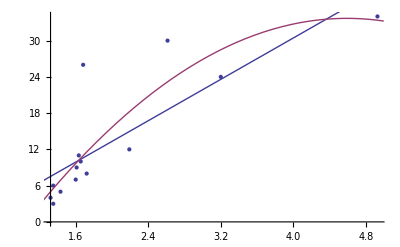

```mathematica
Show[ListPlot[tm],Plot[{lin,para},{x,0,5}]]
```

```mathematica
280*Binomial[20,1]
```

5600

```mathematica
Binomial[31,3]*Binomial[21,0]
```

4495

```mathematica
Do[Print[CacheLimParallelSubLoops[63,21,7,3,32,i]],{i,126}]
```

{1,1599,70,21266700}

{2,861,65,21266700}

{3,533,70,21266700}

{5,287,78,21266700}

{6,287,65,21266700}

{7,246,65,21266700}

{10,123,91,21266700}

{10,123,91,21266700}

{10,123,91,21266700}

{13,123,70,21266700}

{14,123,65,21266700}

{15,91,82,21266700}

{15,91,82,21266700}

{21,82,65,21266700}

{21,82,65,21266700}

{21,82,65,21266700}

«2 more identical outputs»

{26,41,105,21266700}

{26,41,105,21266700}

{26,41,105,21266700}

{30,41,91,21266700}

{30,41,91,21266700}

{30,41,91,21266700}

{35,41,78,21266700}

{35,41,78,21266700}

{35,41,78,21266700}

«1 more identical outputs»

{39,41,70,21266700}

{39,41,70,21266700}

{41,39,70,21266700}

{42,41,65,21266700}

{42,41,65,21266700}

{42,41,65,21266700}

«6 more identical outputs»

{65,21,82,21266700}

{65,21,82,21266700}

{65,21,82,21266700}

«8 more identical outputs»

{70,13,123,21266700}

{70,13,123,21266700}

{70,13,123,21266700}

«2 more identical outputs»

{78,7,205,21266700}

{78,7,205,21266700}

{78,7,205,21266700}

«1 more identical outputs»

{82,21,65,21266700}

{82,21,65,21266700}

{82,21,65,21266700}

«2 more identical outputs»

{91,15,82,21266700}

{91,15,82,21266700}

{91,15,82,21266700}

«6 more identical outputs»

{105,13,82,21266700}

{105,13,82,21266700}

{105,13,82,21266700}

«9 more identical outputs»

{123,13,70,21266700}

{123,13,70,21266700}

{123,13,70,21266700}

«7 more identical outputs»

{130,7,123,21266700}

{130,7,123,21266700}

{130,7,123,21266700}

«19 more identical outputs»

{182,5,123,21266700}

{182,5,123,21266700}

{182,5,123,21266700}

«5 more identical outputs»

```mathematica
Binomial[20,2]*130*861
```

21266700

```mathematica
21*41
```

861

```mathematica
Binomial[20,2]
```

190

```mathematica
42*3895
```

163590

```mathematica
Divisors[7790]
```

{1,2,5,10,19,38,41,82,95,190,205,410,779,1558,3895,7790}

```mathematica
CacheLimParallelSubLoops[63,21,6,1,28]
```

{7462,114,850668}

```mathematica
410*20
```

8200

```mathematica
Binomial[63,7]
```

553270671

```mathematica
Binomial[7,4]*Binomial[7-4,3]
```

35

```mathematica
(42-5+1)*(21-2+1)
```

760

```mathematica
nCores1=80;
nOmg1=4;
ttlF1=63;
ttlOriF1=21;
nOri1=3;
mem1=3000;
OriCases1=Binomial[ttlOriF1,nOri1];
OmgOriCases1=Binomial[(ttlF1-ttlOriF1-1),(nOmg1-nOri1-1)]*OriCases1;
initSubDiv1=Last@Nearest[Flatten@Union@Divisors[{OmgOriCases1/OriCases1(*,OriCases1*)}],IntegerPart[Ceiling[24/2]*nCores1/(nOmg1*(OriCases1)*74*10^(-4))]];
parDiv1=Last@Nearest[Flatten@Union@Divisors[{OmgOriCases1/initSubDiv1/OriCases1}],IntegerPart[Ceiling[1000*mem1/2]/(initSubDiv1*nOmg1*(OriCases1)*74*10^(-4))]]
{initSubDiv1,parDiv1,(*OmgOriCases1/initSubDiv1/OriCases1,*)OmgOriCases1/initSubDiv1/OriCases1/parDiv1,OmgOriCases1}
```

1

{1,1,1,1330}

```mathematica
410*28*Binomial[20,2]
```

229600

```mathematica
20.*7*Binomial[20,2]*74*10^(-4)/1024
```

0.192227

```mathematica
140*20*41
```

114800

```mathematica
205*20*14
```

57400

```mathematica
20*287*Binomial[20,2]*ByteCount[{{3},{1},{2},{3},{4},{5},{6}}]/1024./1024/1024
```

0.552541

```mathematica
2*OriCases1*21
```

47880

```mathematica
21*41.*OriCases1*74*10^(-4)
```

1210.57

```mathematica
21*41*OriCases1
```

163590

```mathematica
CacheLimParallelSubLoops[63,21,5,2]
```

{164,70,229600}

```mathematica
3116*273
```

850668

```mathematica
164*20*7*5
```

114800

```mathematica
FactorInteger[70]
```

{{2,1},{5,1},{7,1}}

```mathematica
Binomial[42,6]*Binomial[21,1]
```

110161506

```mathematica
{v1,v2}=CacheLimParallelSubLoops[63,21,7]
v1*v2
```

{7030,3198}

22481940

```mathematica
Binomial[42,6]
```

5245786

```mathematica
62244*2870/1976
```

90405

```mathematica
1-3./25
```

0.88

```mathematica
cache=25; (* system cache memory *)
cores=8; (* system cores *)
mbyt=74*10^(-6); (* bytes per entry *)
ttlFlds=63;
norflds=21;
nom=7;
nor=2;
orset=Binomial[norflds,nor];
OmgOri=Binomial[(ttlFlds-norflds),(nom-nor)]*orset
nsub=IntegerPart[Ceiling[cache/2]*cores/(nom*orset*mbyt)]
choices={#-3,#-2,#-1,#,#+1,#+2,#+3}&[nsub]
pfact=FactorInteger[choices]
pl=Max[Length[#]&/@pfact]
nfact=SortBy[Select[pfact,Length[#]==pl&],Last][[1]]
```

178640280

956

{953,954,955,956,957,958,959}

{{{953,1}},{{2,1},{3,2},{53,1}},{{5,1},{191,1}},{{2,2},{239,1}},{{3,1},{11,1},{29,1}},{{2,1},{479,1}},{{7,1},{137,1}}}

3

{{3,1},{11,1},{29,1}}

```mathematica
GCD[OmgOri,#]&/@choices
```

{1,18,5,4,3,2,7}

```mathematica
OmgOri=Binomial[(ttlFlds-norflds),(nom-nor)]*orset
sfact=FactorInteger[OmgOri]
```

178640280

{{2,3},{3,2},{5,1},{7,2},{13,1},{19,1},{41,1}}

```mathematica
divSub=Nearest[GCD[OmgOri,#]&/@choices,nsub][[1]]
rest=OmgOri/divSub
factRest=FactorInteger[rest]
```

18

9924460

{{2,2},{5,1},{7,2},{13,1},{19,1},{41,1}}

```mathematica
fDivSub=Nearest[Flatten@(Table[divSub*#[[1]]^i,{i,#[[2]]}]&/@factRest),nsub][[1]]
subl=OmgOri/fDivSub
factRest2=FactorInteger[subl]
```

882

202540

{{2,2},{5,1},{13,1},{19,1},{41,1}}

```mathematica
882*202540
```

178640280

```mathematica
8*13*3*41
```

12792

```mathematica
ByteCount[out1]/1024/1024./14
```

100.021

```mathematica
facts=(#[[1]]^#[[2]])&/@nfact
facts2=(#[[1]]^#[[2]])&/@sfact
```

{2,3,25}

{4,3,25,49,13,19,41}

```mathematica
res=(Nearest[(#[[1]]^#[[2]])&/@sfact,#]&/@facts)[[;;,1]]
rest=Complement[facts2,res]
res[[0]]=Times;
res
```

{{3},{3},{25}}

{3,4,13,19,25,41,49}

{225}

```mathematica
res
```

{4,9,13}